# Auto-grader for Open Ended Math Problems

### Determining Equivalent Responses and Classifying Problems for Proper Evaluation of student response

Silas Kurt Grossberndt
Robert Nachbar

#### Abstract

In order to automatically grade student problems one must identify the scope and level of the problem and then define equivalent answers appropriate to the context of the question and knowledge of the student. To this end, we first train a Neural Network Classifier on a data set of problems in Algebra 1, Algebra 2 and Calculus. Then, using a combination of rule based checks and the theorem prover, we define equivalent answers, then check that particular rules were not used in order to maintain equivalence at the level of the student to prevent cheating. All of this is then packaged in a GUI for understandability.

## Introduction

When providing questions to students online, the teacher is often left with a dilemma. Do  you give the student a multiple choice problem that fails to properly test their ability by allowing guessing, or do you give them a long answer that will only accept one correct answer, when there might be multiple equivalent answers? To add in all possible answers would be an onerous task, thus it would be preferable to have the system automatically identify all possible answers. However, this presents a challenge in its own right. How does one limit the possible answers to those that the student would have reached based on the level of their knowledge, and how does one deal with problems that may limit the scope of the equivalent answers? To this end, we define a two part problem: classification of the problem’s level and scope and cross checking for equivalent answers.

## Classifying and Identifying Problems

### Classifying Questions to determine the level of the problem

The problem of classification is often solved by machine learning techniques trained on large data sets. In this case, I retrained a series of models in the Wolfram language “Classify” function on a 1800 question data set in algebra 1, 2  and calculus, grouping all the problems and providing the problems and groupings to the network, i.e. training in a supervised manner. Then, the accuracy of each model was tested by comparing the probability of identification as the proper grouping to the highest probability of the other two groups, using:

```mathematica
Clear[questionClassifier]
questionClassifier=Classify[<|"algebra 1"->algebra1Questions, "algebra 2"->algebra2Qs|> , PerformanceGoal->"Quality", Method->"Markov"]


algebra1IsAlgebra1=questionClassifier[algebra1Questions, {"Probability", "algebra 1"}];
algebra1IsAlgebra2=questionClassifier[algebra1Questions, {"Probability", "algebra 2"}];

algebra2IsAlgebra1=questionClassifier[algebra2Qs, {"Probability", "algebra 1"}];
algebra2IsAlgebra2=questionClassifier[algebra2Qs, {"Probability", "algebra 2"}];

lp=ListLogPlot[#right/#wrong&@ <|"right"-> algebra1IsAlgebra1, "wrong"-> algebra1IsAlgebra2|>,AxesLabel->{"Data"},PlotLabel->"Algebra 1 ", GridLines->{{}, {1}}, GridLinesStyle->Red] ;
lp1=ListLogPlot[#right/#wrong&@ <|"right"-> algebra2IsAlgebra2, "wrong"-> algebra2IsAlgebra1|>,AxesLabel->{"Data"}, PlotLabel->"Algebra 2",GridLines->{{}, {1}}, GridLinesStyle->Red];
```

ClassifierFunction[…]

All models were given the “Quality” goal to improve accuracy at the cost of training time, as the training is taking place ahead of time, and the system is not retrained live. However, when this was performed on data generated by the Wolfram|Alpha Problem Generator, where the addition of calculus made “What is 1+1” evaluate as calculus independent of the number of inputs. Total training inputs are 1302, with 651 each of algebra 1 and 2.

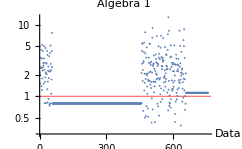
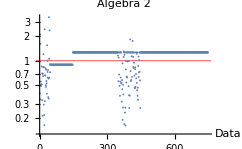
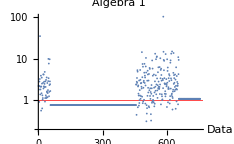
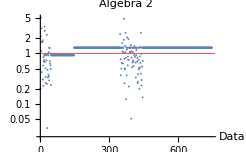
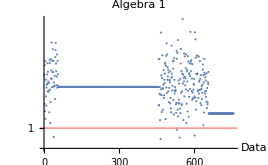
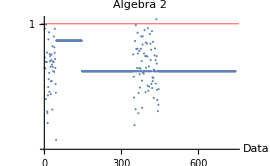
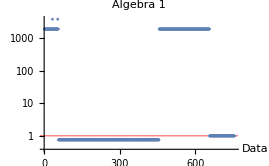
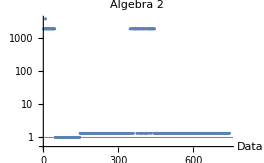
Method | Algebra1  | Algebra 2 | Accuracy
Automatic | -Graphics- | -Graphics- | 0.58
Neural Network | -Graphics- | -Graphics- | 0.59
Logistic Regression | -Graphics- | -Graphics- | 0.50
Naive Bayesian | -Graphics- | -Graphics- | 0.67
Nearest Neighbor | -Graphics- | -Graphics- | 0.57
Gradiant Boosted Trees | -Graphics- | -Graphics- | 0.59
Markov | -Graphics- | -Graphics- | 0.93
Support Vector Machine | -Graphics- | -Graphics- | 0.57
Random Forest | -Graphics- | -Graphics- | 0.63
Decision Tree | -Graphics- | -Graphics- | 0.50

It is thus obvious to select the Markov model for the classifier.

### Identifying the Context of the Problem

The context of the problem, however, does not get captured by the classifier above. The classifier simply finds the level, meanwhile the context, for example, would be “write your answer as a simplified fraction”. These contexts are identified via pattern matching. These rules are then used to assign a specific tag:

Value | Meaning
0 | No Context Restrictions
1 | Simplest Form Fraction
2 | Decimal Representation
3 | A set of Points
4 | Calculus
5 | A set of Points of Simplest Fractions
6 | A set of Points in Decimal
7 | Mixed Number
8 | Improper Fraction

The rules were given by :

```mathematica
turnOffEquivFrac[question_]:=StringMatchQ[question, {"*raction*implest form"}];
isMatrixQ[answer_]:=MatchQ[answer, MatrixForm];
allpoints[question_]:=StringMatchQ[question, {"*all points*"}];
eitherPointfirst[a_, b_,c_, d_]:= {{"(",a, b, ")"},{"("c, d ")"}}-> {{"("c, d ")"},{"(",a, b, ")"}}
isPoint[answer_]:=StringMatchQ[answer, {"(*,*)"}];
improperFraction[question_]:=StringMatchQ[question, "*mproper fraction*"];
decForm[question_]:=StringMatchQ[question, "*ecimal form*"];
isCalcQ[question_]:=StringMatchQ[question, {"*erivative*", "*ifferniate*", "*ntegra*", "*aylor*xpand*", "*acLa*xpand*", "*imit*"}];
mixedNumber[question_]:=StringMatchQ[question, "*ixed number*"];
```

Note that the calculus rule here will serve as the classifier for calculus, which is likely to leave a gap of problems given symbolically. One method to deal with this is discussed in the conclusion.

## Identifying Equivalent Responses

In order to provide a more robust and deployable version of the autograder, the identification of context and equivalent responses are handled in a new package, “Math Autograder”.

### Rule Based Identification

In order to perform checks on the context restricted identification, one performs the following for tags 1,2,7 and 8:

```mathematica
1|2|7|8, If[correctAnswer[answer, correct], True, False],
```

And for tags 5 and 6, one does the following to check if the data are equivalent except for ordering of the points:

```mathematica
5|6, If[Complement[StringSplit[answer, "),("], StringSplit[correct, "),("]]=={}, True, False
```

### Theorem Prover Based Identification

In the majority of cases, the first test is still rule based:

```mathematica
correctAnswer[answer_, correct_]:=MatchQ[Interpreter["MathExpression"][answer], Interpreter["MathExpression"][correct]]
```

In order to reject answers that would give false positive, or answers that would be beyond the level of the student, we also implement the theorem prover:

```mathematica
If[correctAnswer[answer, correct], True, If[Simplify[Interpreter["MathExpression"][answer]- Interpreter["MathExpression"][correct]]==0, 
					If[UnsameQ[Head[Interpreter["MathExpression"][answer]], Failure], 
						formattedanswer:=removeProperFormat[Interpreter["MathExpression"][answer]];
						formattedcorrectanswer=removeProperFormat[Interpreter["MathExpression"][correct]];
						proof=TimeConstrained[FindEquationalProof[formattedanswer==formattedcorrectanswer , theorems[level]],1];
							If[proof["Logic"]=="EquationalLogic", 
								If[Complement[Query[Key[{"SubstitutionLemma", All}proof["ProofDataset"]["Statement"]]], theorems[level]]=={}, True, False],
								False],
						False],
					False]],
```

Wherein the formatting replacement is necessary to allow for the use of the defined axioms:

```mathematica
algebratheorems={ForAll[{a,b,c}, g[a, g[b,c]]==g[g[a, b], c]], 
				 ForAll[{a,b}, g[a, b]==g[b,a]], 
				 ForAll[{a,b}, f[a,b]==f[b,a]],
				 ForAll[{a,b,c}, f[a,f[b,c]]==f[f[a,b],c]],
				 ForAll[{a,b,c}, f[a, g[c,b]]==g[f[a,c], f[a,b]]],
				 ForAll[a, g[a,e]==a],
				 ForAll[a, f[a, e]==e],
				 ForAll[a, f[a, n]==a],
				 ForAll[a, g[a, inv[a]]==e],
				 ForAll[a, f[a, inv1[a]]==n]} (*This defines an abelian ring w/ distributive property*)
```

```mathematica
algebraandtrigtheorems={ForAll[{a,b,c}, g[a, g[b,c]]==g[g[a, b], c]], 
				 ForAll[{a,b}, g[a, b]==g[b,a]], 
				 ForAll[{a,b}, f[a,b]==f[b,a]],
				 ForAll[{a,b,c}, f[a,f[b,c]]==f[f[a,b],c]],
				 ForAll[{a,b,c}, f[a, g[c,b]]==g[f[a,c], f[a,b]]],
				 ForAll[a, g[a,e]==a],
				 ForAll[a, f[a, e]==e],
				 ForAll[a, f[a, n]==a],
				 ForAll[a, g[a, inv[a]]==e],
				 ForAll[a, f[a, inv1[a]]==n], 
				 ForAll[{a,b}, sin[g[a,b]]==g[f[sin[a],cos[b]], f[sin[b], cos[a]]]],
				 ForAll[ {a,b}, cos[g[a,b]]==g[f[cos[a],cos[b]], f[sin[inv[b]], sin[a]]]],
				 ForAll[a, sin[inv[a]]==inv[sin[a]]],
				 ForAll[a, cos[inv[a]]==cos[a]],
				 ForAll[a, g[f[sin[a],sin[a]], f[cos[a], cos[a]]]==n]}
```

All higher power terms would be picked up by the correct answer rule prover. There is the possibility of edge cases causing failure involving logarithms, but that is beyond the scope of this work. The conversion from the Wolfram Language input to the format required for this is done by:

```mathematica
removeSinCos[given_]:=given/.{Sin->sin, Cos->cos} 
removeSinCos[Sin[5]+Cos[x]]
replacePlus[given_]:=given/.{Plus-> g, Times[-1, amin_]->inv[amin]}
replacePlus[a-b]
replaceMulti[given_]:=given/.{Times-> f, Power[adiv_, -1]-> inv1[adiv]}
replaceTanSecCscCot[given_]:=given/.{Tan[atan_]-> f[sin[atan],inv1[cos[atan]]], Sec[asec_]-> inv1[cos[asec]], Csc[acsc_]-> inv1[sin[acsc]], Cot[acot_]-> f[inv1[sin[acot]],cos[acot]]}
replaceTanSecCscCot[Tan[y]+ Csc[x]]
removeProperFormat[given_]:=replacePlus[replaceMulti[removeSinCos[replaceTanSecCscCot[given]]]]
```

## Future work and Conclusions

This project has developed a Classifier and a Package that may be implemented in a variety of applications. Ideally, one can consider two exemplars. One has the student submits an answer to a randomly selected question from a database that has been built using Wolfram|Alpha’s Problem Generator. The student may select one of the three levels, receive a question, submit an answer and check that it is correct. After the correct answer has been submitted, the system automatically pulls a new question from the list in the selected type. The second allows for the teacher to create a quiz and store it as a new database, which will then be fed to the first exemplar. Thus, we see this project as a quiet sever side application, and as a service that would be deliverable to a client. Further work could encompass the addition of further levels of question, the use of graphical data as a selected answer or the inclusion of a retraining function in the neural net to improve classification accuracy, as well as the integration of the data into the described GUIs.

## Exemplar Implementation

The following is an example of asking a defined question (to avoid adding extra data to this presentation by adding in the question set), and checking if the answer is correct:

```mathematica
level=questionClassifier["What is 1+1"]
checkforEquivlentanswers["What is 1+1", "2" ,"3", level]
```

algebra 1

False

```mathematica
level=questionClassifier["How else can we write c*(a+b)"]
checkforEquivlentanswers["How else can we write c*(a+b)", "a*c+b*c", "c*a+b*c",level]
```

algebra 1

True

## Initialization Cells

```mathematica
correctAnswer[answer_, correct_]:=MatchQ[Interpreter["MathExpression"][answer], Interpreter["MathExpression"][correct]]
turnOffEquivFrac[question_]:=StringMatchQ[question, {"*raction*implest form"}];
isMatrix[answer_]:=MatchQ[answer, MatrixForm];
allpoints[question_]:=StringMatchQ[question, {"*all points*"}];
eitherPointfirst[a_, b_,c_, d_]:= {{"(",a, b, ")"},{"("c, d ")"}}-> {{"("c, d ")"},{"(",a, b, ")"}}
isPoint[answer_]:=StringMatchQ[answer, {"(*,*)"}];
improperFraction[question_]:=StringMatchQ[question, "*mproper fraction*"];
decForm[question_]:=StringMatchQ[question, "*ecimal form*"];
isCalc[question_]:=StringMatchQ[question, {"*erivative*", "*ifferniate*", "*ntegra*", "*aylor*xpand*", "*acLa*xpand*", "*imit*"}];
mixedNumber[question_]:=StringMatchQ[question, "*ixed number*"];
(*This is the wrong way to do it, patern matching is better here*)
expandToSix[answer_, correct_, x_]:=If[Series[answer, {x, 0, 6}]==Series[correct, {x, 0, 6}], True, False]
algebratheorems={ForAll[{a,b,c}, g[a, g[b,c]]==g[g[a, b], c]], 
				 ForAll[{a,b}, g[a, b]==g[b,a]], 
				 ForAll[{a,b}, f[a,b]==f[b,a]],
				 ForAll[{a,b,c}, f[a,f[b,c]]==f[f[a,b],c]],
				 ForAll[{a,b,c}, f[a, g[c,b]]==g[f[a,c], f[a,b]]],
				 ForAll[a, g[a,e]==a],
				 ForAll[a, f[a, e]==e],
				 ForAll[a, f[a, n]==a],
				 ForAll[a, g[a, inv[a]]==e],
				 ForAll[a, f[a, inv1[a]]==n]} (*This defines an abelian ring w/ distributive property*)
				 
algebraandtrigtheorems={ForAll[{a,b,c}, g[a, g[b,c]]==g[g[a, b], c]], 
				 ForAll[{a,b}, g[a, b]==g[b,a]], 
				 ForAll[{a,b}, f[a,b]==f[b,a]],
				 ForAll[{a,b,c}, f[a,f[b,c]]==f[f[a,b],c]],
				 ForAll[{a,b,c}, f[a, g[c,b]]==g[f[a,c], f[a,b]]],
				 ForAll[a, g[a,e]==a],
				 ForAll[a, f[a, e]==e],
				 ForAll[a, f[a, n]==a],
				 ForAll[a, g[a, inv[a]]==e],
				 ForAll[a, f[a, inv1[a]]==n], 
				 ForAll[{a,b}, sin[g[a,b]]==g[f[sin[a],cos[b]], f[sin[b], cos[a]]]],
				 ForAll[ {a,b}, cos[g[a,b]]==g[f[cos[a],cos[b]], f[sin[inv[b]], sin[a]]]],
				 ForAll[a, sin[inv[a]]==inv[sin[a]]],
				 ForAll[a, cos[inv[a]]==cos[a]],
				 ForAll[a, g[f[sin[a],sin[a]], f[cos[a], cos[a]]]==n]}
theorems=<|"algebra 1"-> {algebratheorems}, "algebra 2"-> {algebraandtrigtheorems}, "calc"-> {algebraandtrigtheorems}|>;
removeSinCos[given_]:=given/.{Sin->sin, Cos->cos} 
removeSinCos[Sin[5]+Cos[x]]
replacePlus[given_]:=given/.{Plus-> g, Times[-1, amin_]->inv[amin]}
replacePlus[a-b]
replaceMulti[given_]:=given/.{Times-> f, Power[adiv_, -1]-> inv1[adiv]}
replaceTanSecCscCot[given_]:=given/.{Tan[atan_]-> f[sin[atan],inv1[cos[atan]]], Sec[asec_]-> inv1[cos[asec]], Csc[acsc_]-> inv1[sin[acsc]], Cot[acot_]-> f[inv1[sin[acot]],cos[acot]]}
replaceTanSecCscCot[Tan[y]+ Csc[x]]
removeProperFormat[given_]:=replacePlus[replaceMulti[removeSinCos[replaceTanSecCscCot[given]]]]
determinetags[question_]:=If[allpoints[question], 
									If[turnOffEquivFrac[question], 5, 
												If[decForm[question], 6, 3]],
									If[turnOffEquivFrac[question], 1, 
											If[decForm[question], 2, 
												If[isCalc[question], 4, 
													If[mixedNumber[question], 7, 
														If[improperFraction[question], 8, 0]
													   ]
													]
												]
											]
								]; 


equivalentAnswer[level_, tags_, answer_, correct_]:=
Module[{formattedanswer, formattedcorrectanswer, proof}, 
			
				If[tags==4, level="calc"];
				Switch[tags, 
				0| 3| 4, If[correctAnswer[answer, correct], True, If[Simplify[Interpreter["MathExpression"][answer]- Interpreter["MathExpression"][correct]]==0, 
					If[UnsameQ[Head[Interpreter["MathExpression"][answer]], Failure], 
						formattedanswer:=removeProperFormat[Interpreter["MathExpression"][answer]];
						formattedcorrectanswer=removeProperFormat[Interpreter["MathExpression"][correct]];
						proof=TimeConstrained[FindEquationalProof[formattedanswer==formattedcorrectanswer , theorems[level]],10];
							If[proof["Logic"]=="EquationalLogic", 
								If[Complement[Query[Key[{"SubstitutionLemma", All}proof["ProofDataset"]["Statement"]]], theorems[level]]=={}, True, False],
								False],
						False],
					False]],
				1, If[correctAnswer[answer, correct], True, False], 
				2, If[correctAnswer[answer, correct], True, False], 
				5, If[Complement[StringSplit[answer, "),("], StringSplit[correct, "),("]]=={}, True, False],  
				6, If[Complement[StringSplit[answer, "),("], StringSplit[correct, "),("]]=={}, True, False],
				_, MatchQ[answer, correct] (*exact match is default case*)
				
				]] 
				
checkforEquivlentanswers[question_, answer_, correct_, level_]:=
Module[{t},
			t=determinetags[question];
			equivalentAnswer[level, t, answer, correct]]	
equivalentAnswer["algebra 1", 7, "1 1/4", "5/4"]
```

{∀_{a,b,c}g[a,g[b,c]]==g[g[a,b],c],∀_{a,b}g[a,b]==g[b,a],∀_{a,b}f[a,b]==f[b,a],∀_{a,b,c}f[a,f[b,c]]==f[f[a,b],c],∀_{a,b,c}f[a,g[c,b]]==g[f[a,c],f[a,b]],∀_a g[a,e]==a,∀_a f[a,e]==e,∀_a f[a,n]==a,∀_a g[a,inv[a]]==e,∀_a f[a,inv1[a]]==n}

{∀_{a,b,c}g[a,g[b,c]]==g[g[a,b],c],∀_{a,b}g[a,b]==g[b,a],∀_{a,b}f[a,b]==f[b,a],∀_{a,b,c}f[a,f[b,c]]==f[f[a,b],c],∀_{a,b,c}f[a,g[c,b]]==g[f[a,c],f[a,b]],∀_a g[a,e]==a,∀_a f[a,e]==e,∀_a f[a,n]==a,∀_a g[a,inv[a]]==e,∀_a f[a,inv1[a]]==n,∀_{a,b}sin[g[a,b]]==g[f[sin[a],cos[b]],f[sin[b],cos[a]]],∀_{a,b}cos[g[a,b]]==g[f[cos[a],cos[b]],f[sin[inv[b]],sin[a]]],∀_a sin[inv[a]]==inv[sin[a]],∀_a cos[inv[a]]==cos[a],∀_a g[f[sin[a],sin[a]],f[cos[a],cos[a]]]==n}

cos[x]+sin[5]

g[a,inv[b]]

f[sin[y],inv1[cos[y]]]+inv1[sin[x]]

False

```mathematica
algebra1Questions=;
```

```mathematica
algebra2Qs={"What is the most specific subset of the real numbers that -7 is a part of?","Plot 1.25, 2/3 and 2 on a number line","Identify the property used in the equations below as distributive, inverse or associative","Evaluate 2\!\(\*SuperscriptBox[\(x\), \(2\)]\)-9 for x=-3","Expand (a+b\!\(\*SuperscriptBox[\()\), \(3\)]\)","What is (a+b\!\(\*SuperscriptBox[\()\), \(n\)]\) (Hint: What theorem is this?)","Solve 4x-9=11","Solve 3(x-5)+4=10","Solve 3(x-5)+4=10","Solve 9(x-3)+4=10","Solve (x-1/2)=(2x+3)","Solve 3|x-5|=12","Solve 8(x-5)+4=10","Solve (\!\(\*SuperscriptBox[\(x\), \(2\)]\)-5)=20","Use the law of sines to find the missing side of this triangle","What is the largest value for the missing side of this triangle","What is sin(60)","What is tan(30)","Write 30 degrees in radians","Write π/4 in degrees","Is x=-8 a solution to 1/2x+6>3?","Solve and graph the solution to 2x-3<7","Solve and graph the solution to |3x-1|≥10","How many miutes are in a day?","Wrie the standard form of y=3/2 x+2","Write slope intercept form for a slope of 2 and y-intercept of 12","Find a perpedicular line of y=3x+2 with y intercept of the origin","What are the domain and range of the trigonometric functions?","Graph the inequality y<3x+4","Find the equation of best fit for the below listed data","Graph the parabola give by \!\(\*SuperscriptBox[\(x\), \(2\)]\)+3x+2. Find the zeros, vertex and intercept","What is the sum from 1 to 5 of a=10n+3","What is the next term in the series ","what is the sum of the geometric series from 1 to infinity of 9(1/10\!\(\*SuperscriptBox[\()\), \(n\)]\)?","What are the discontiuities in the function y=(x+2)/(x+3x+2). Which are fundamental and which are removable?","What is ln(1)?","What are the domain and range of \!\(\*SuperscriptBox[\(e\), \(x\)]\) and ln(x)","sin(40)","cos(45)","tan(63)","sin(121)","sin(π/3)","sin(π/5)","cos(π/13)","sin(x)+cos(y)","sin^(2x)","Add "Times[8,Power[11,1/2]]" and "Times[18,Power[11,1/2]]".","Add "Times[4,Power[11,1/2]]" and "Times[25,Power[11,1/2]]".","Add "Times[5,Power[11,1/2]]" and "Times[19,Power[11,1/2]]".","Sum "Times[14,Power[7,1/2]]" and "Times[19,Power[7,1/2]]".","Add "Times[9,Power[7,1/2]]" and "Times[12,Power[7,1/2]]".","Add "Times[13,Power[3,1/2]]" and "Times[18,Power[3,1/2]]".","Sum "Times[24,Power[3,1/2]]" and "Times[19,Power[3,1/2]]".","Add "Times[18,Power[5,1/2]]" and "Times[25,Power[5,1/2]]".","Sum "Times[5,Power[3,1/2]]" and "Times[4,Power[3,1/2]]".","Add "Times[21,Power[7,1/2]]" and "Times[10,Power[7,1/2]]".","Add "Times[21,Power[7,1/2]]" and "Times[20,Power[7,1/2]]".","Add "Times[19,Power[11,1/2]]" and "Times[17,Power[11,1/2]]".","Sum "Times[12,Power[5,1/2]]" and "Times[22,Power[5,1/2]]".","Sum "Times[4,Power[7,1/2]]" and "Times[24,Power[7,1/2]]".","Add "Times[17,Power[5,1/2]]" and "Times[18,Power[5,1/2]]".","Add "Times[17,Power[7,1/2]]" and "Times[15,Power[7,1/2]]".","Sum "Times[11,Power[7,1/2]]" and "Times[9,Power[7,1/2]]".","Add "Times[9,Power[11,1/2]]" and "Times[24,Power[11,1/2]]".","Sum "Times[15,Power[3,1/2]]" and "Times[4,Power[3,1/2]]".","Add "Times[18,Power[3,1/2]]" and "Times[17,Power[3,1/2]]".","Add "Times[14,Power[5,1/2]]" and "Times[13,Power[5,1/2]]".","Add "Times[8,Power[7,1/2]]" and "Times[21,Power[7,1/2]]".","Sum "Times[15,Power[11,1/2]]" and "Times[22,Power[11,1/2]]".","Sum "Times[14,Power[11,1/2]]" and "Times[21,Power[11,1/2]]".","Sum "Times[6,Power[3,1/2]]" and "Times[24,Power[3,1/2]]".","Sum "Times[4,Power[7,1/2]]" and "Times[7,Power[7,1/2]]".","Sum "Times[19,Power[11,1/2]]" and "Times[24,Power[11,1/2]]".","Add "Times[8,Power[11,1/2]]" and "Times[17,Power[11,1/2]]".","Add "Times[10,Power[3,1/2]]" and "Times[6,Power[3,1/2]]".","Add "Times[3,Power[7,1/2]]" and "Times[23,Power[7,1/2]]".","Sum "Times[13,Power[3,1/2]]" and "Times[20,Power[3,1/2]]".","Add "Times[13,Power[11,1/2]]" and "Times[15,Power[11,1/2]]".","Add "Times[8,Power[3,1/2]]" and "Times[6,Power[3,1/2]]".","Add "Times[21,Power[5,1/2]]" and "Times[25,Power[5,1/2]]".","Sum "Times[5,Power[5,1/2]]" and "Times[11,Power[5,1/2]]".","Add "Times[10,Power[7,1/2]]" and "Times[17,Power[7,1/2]]".","Add "Times[21,Power[5,1/2]]" and "Times[15,Power[5,1/2]]".","Sum "Times[23,Power[3,1/2]]" and "Times[19,Power[3,1/2]]".","Sum "Times[22,Power[7,1/2]]" and "Times[12,Power[7,1/2]]".","Sum "Times[3,Power[11,1/2]]" and "Times[16,Power[11,1/2]]".","Sum "Times[18,Power[5,1/2]]" and "Times[19,Power[5,1/2]]".","Add "Times[21,Power[11,1/2]]" and "Times[10,Power[11,1/2]]".","Sum "Times[11,Power[7,1/2]]" and "Times[8,Power[7,1/2]]".","Add "Times[23,Power[5,1/2]]" and "Times[16,Power[5,1/2]]".","Add "Times[20,Power[7,1/2]]" and "Times[12,Power[7,1/2]]".","Sum "Times[23,Power[3,1/2]]" and "Times[22,Power[3,1/2]]".","Add "Times[23,Power[3,1/2]]" and "Times[18,Power[3,1/2]]".","Sum "Times[23,Power[3,1/2]]" and "Times[24,Power[3,1/2]]".","Sum "Times[5,Power[5,1/2]]" and "Times[18,Power[5,1/2]]".","Add "Times[16,Power[5,1/2]]" and "Times[17,Power[5,1/2]]".","Add "Times[24,Power[11,1/2]]" and "Times[7,Power[11,1/2]]".","Sum "Times[25,Power[7,1/2]]" and "Times[16,Power[7,1/2]]".","Add "Times[13,Power[7,1/2]]" and "Times[10,Power[7,1/2]]".","Sum "Times[18,Power[7,1/2]]" and "Times[12,Power[7,1/2]]".","Add "Times[7,Power[3,1/2]]" and "Times[10,Power[3,1/2]]".","Sum "Times[10,Power[5,1/2]]" and "Times[13,Power[5,1/2]]".","Sum "Times[12,Power[3,1/2]]" and "Times[21,Power[3,1/2]]".","Add "Times[10,Power[11,1/2]]" and "Times[16,Power[11,1/2]]".","Sum "Times[3,Power[7,1/2]]" and "Times[24,Power[7,1/2]]".","Sum "Times[20,Power[3,1/2]]" and "Times[22,Power[3,1/2]]".","Add "Times[24,Power[7,1/2]]" and "Times[13,Power[7,1/2]]".","Add "Times[17,Power[7,1/2]]" and "Times[25,Power[7,1/2]]".","Sum "Times[9,Power[5,1/2]]" and "Times[18,Power[5,1/2]]".","Add "Times[11,Power[3,1/2]]" and "Times[20,Power[3,1/2]]".","Add "Times[20,Power[3,1/2]]" and "Times[10,Power[3,1/2]]".","Add "Times[23,Power[7,1/2]]" and "Times[25,Power[7,1/2]]".","Sum "Times[9,Power[11,1/2]]" and "Times[23,Power[11,1/2]]".","Add "Times[10,Power[3,1/2]]" and "Times[7,Power[3,1/2]]".","Sum "Times[9,Power[3,1/2]]" and "Times[21,Power[3,1/2]]".","Add "Times[9,Power[5,1/2]]" and "Times[23,Power[5,1/2]]".","Sum "Times[7,Power[3,1/2]]" and "Times[9,Power[3,1/2]]".","Add "Times[16,Power[11,1/2]]" and "Times[7,Power[11,1/2]]".","Sum "Times[8,Power[5,1/2]]" and "Times[22,Power[5,1/2]]".","Sum "Times[6,Power[3,1/2]]" and "Times[4,Power[3,1/2]]".","Add "Times[21,Power[7,1/2]]" and "Times[9,Power[7,1/2]]".","Add "Times[13,Power[5,1/2]]" and "Times[21,Power[5,1/2]]".","Sum "Times[22,Power[5,1/2]]" and "Times[13,Power[5,1/2]]".","Sum "Times[23,Power[3,1/2]]" and "Times[25,Power[3,1/2]]".","Sum "Times[12,Power[7,1/2]]" and "Times[21,Power[7,1/2]]".","Sum "Times[8,Power[11,1/2]]" and "Times[24,Power[11,1/2]]".","Sum "Times[25,Power[5,1/2]]" and "Times[21,Power[5,1/2]]".","Add "Times[19,Power[3,1/2]]" and "Times[9,Power[3,1/2]]".","Add "Times[21,Power[7,1/2]]" and "Times[19,Power[7,1/2]]".","Add "Times[11,Power[7,1/2]]" and "Times[20,Power[7,1/2]]".","Sum "Times[13,Power[3,1/2]]" and "Times[17,Power[3,1/2]]".","Add "Times[12,Power[3,1/2]]" and "Times[7,Power[3,1/2]]".","Sum "Times[15,Power[3,1/2]]" and "Times[3,Power[3,1/2]]".","Sum "Times[8,Power[7,1/2]]" and "Times[7,Power[7,1/2]]".","Add "Times[11,Power[7,1/2]]" and "Times[22,Power[7,1/2]]".","Add "Times[17,Power[11,1/2]]" and "Times[9,Power[11,1/2]]".","Add "Times[8,Power[3,1/2]]" and "Times[15,Power[3,1/2]]".","Sum "Times[4,Power[7,1/2]]" and "Times[21,Power[7,1/2]]".","Add "Times[9,Power[7,1/2]]" and "Times[17,Power[7,1/2]]".","Add "Times[14,Power[3,1/2]]" and "Times[21,Power[3,1/2]]".","Sum "Times[13,Power[3,1/2]]" and "Times[17,Power[3,1/2]]".","Sum "Times[18,Power[3,1/2]]" and "Times[7,Power[3,1/2]]".","Add "Times[7,Power[5,1/2]]" and "Times[18,Power[5,1/2]]".","Sum "Times[18,Power[11,1/2]]" and "Times[3,Power[11,1/2]]".","Sum "Times[23,Power[5,1/2]]" and "Times[5,Power[5,1/2]]".","Add "Times[17,Power[5,1/2]]" and "Times[6,Power[5,1/2]]".","What is "Times[9,Power[11,1/2]]" multiplied by "Times[8,Power[7,1/2]]"?","Compute "Times[11,Power[7,1/2]]" × "Times[5,Power[3,1/2]]".","What is "Times[4,Power[3,1/2]]" multiplied by "Times[10,Power[7,1/2]]"?","What is "Times[19,Power[11,1/2]]" multiplied by "Times[4,Power[7,1/2]]"?","What is "Times[4,Power[5,1/2]]" multiplied by "Times[9,Power[3,1/2]]"?","Compute "Times[11,Power[11,1/2]]" × "Times[4,Power[3,1/2]]".","Compute "Times[7,Power[7,1/2]]" × "Times[11,Power[5,1/2]]".","What is "Times[4,Power[3,1/2]]" multiplied by "Times[6,Power[7,1/2]]"?","What is "Times[7,Power[11,1/2]]" multiplied by "Times[11,Power[5,1/2]]"?","Compute "Times[7,Power[7,1/2]]" × "Times[4,Power[11,1/2]]".","What is "Times[9,Power[11,1/2]]" multiplied by "Times[13,Power[5,1/2]]"?","What is "Times[16,Power[7,1/2]]" multiplied by "Times[5,Power[3,1/2]]"?","What is "Times[16,Power[5,1/2]]" multiplied by "Times[5,Power[3,1/2]]"?","What is "Times[9,Power[7,1/2]]" multiplied by "Times[6,Power[11,1/2]]"?","What is "Times[3,Power[5,1/2]]" multiplied by "Times[3,Power[7,1/2]]"?","What is "Times[13,Power[5,1/2]]" multiplied by "Times[7,Power[3,1/2]]"?","What is "Times[9,Power[3,1/2]]" multiplied by "Times[5,Power[11,1/2]]"?","What is "Times[8,Power[7,1/2]]" multiplied by "Times[4,Power[3,1/2]]"?","What is "Times[12,Power[3,1/2]]" multiplied by "Times[13,Power[11,1/2]]"?","Compute "Times[13,Power[11,1/2]]" × "Times[7,Power[7,1/2]]".","Compute "Times[8,Power[3,1/2]]" × "Times[5,Power[5,1/2]]".","Compute "Times[11,Power[5,1/2]]" × "Times[13,Power[3,1/2]]".","Compute "Times[7,Power[11,1/2]]" × "Times[9,Power[5,1/2]]".","Compute "Times[13,Power[3,1/2]]" × "Times[12,Power[7,1/2]]".","What is "Times[9,Power[7,1/2]]" multiplied by "Times[11,Power[5,1/2]]"?","Compute "Times[12,Power[11,1/2]]" × "Times[17,Power[3,1/2]]".","Compute "Times[13,Power[5,1/2]]" × "Times[6,Power[11,1/2]]".","Compute "Times[10,Power[5,1/2]]" × "Times[6,Power[11,1/2]]".","Compute "Times[12,Power[3,1/2]]" × "Times[4,Power[5,1/2]]".","What is "Times[4,Power[3,1/2]]" multiplied by "Times[5,Power[5,1/2]]"?","Compute "Times[3,Power[3,1/2]]" × "Times[9,Power[5,1/2]]".","What is "Times[10,Power[5,1/2]]" multiplied by "Times[4,Power[3,1/2]]"?","Compute "Times[9,Power[5,1/2]]" × "Times[9,Power[3,1/2]]".","Compute "Times[12,Power[5,1/2]]" × "Times[6,Power[3,1/2]]".","Compute "Times[11,Power[3,1/2]]" × "Times[4,Power[5,1/2]]".","Compute "Times[8,Power[5,1/2]]" × "Times[16,Power[3,1/2]]".","Compute "Times[9,Power[11,1/2]]" × "Times[16,Power[3,1/2]]".","What is "Times[11,Power[5,1/2]]" multiplied by "Times[15,Power[3,1/2]]"?","Compute "Times[12,Power[11,1/2]]" × "Times[6,Power[3,1/2]]".","What is "Times[3,Power[7,1/2]]" multiplied by "Times[14,Power[3,1/2]]"?","Compute "Times[9,Power[5,1/2]]" × "Times[9,Power[7,1/2]]".","Compute "Times[4,Power[5,1/2]]" × "Times[4,Power[3,1/2]]".","Compute "Times[6,Power[7,1/2]]" × "Times[4,Power[3,1/2]]".","Compute "Times[7,Power[5,1/2]]" × "Times[12,Power[3,1/2]]".","What is "Times[11,Power[3,1/2]]" multiplied by "Times[4,Power[11,1/2]]"?","What is "Times[15,Power[5,1/2]]" multiplied by "Times[3,Power[11,1/2]]"?","Compute "Times[13,Power[11,1/2]]" × "Times[6,Power[3,1/2]]".","What is "Times[4,Power[3,1/2]]" multiplied by "Times[4,Power[7,1/2]]"?","Compute "Times[8,Power[5,1/2]]" × "Times[7,Power[7,1/2]]".","Compute "Times[7,Power[11,1/2]]" × "Times[14,Power[7,1/2]]".","Compute "Times[10,Power[5,1/2]]" × "Times[13,Power[7,1/2]]".","Compute "Times[16,Power[5,1/2]]" × "Times[13,Power[3,1/2]]".","Compute "Times[6,Power[5,1/2]]" × "Times[18,Power[11,1/2]]".","Compute "Times[4,Power[11,1/2]]" × "Times[7,Power[3,1/2]]".","What is "Times[8,Power[3,1/2]]" multiplied by "Times[4,Power[7,1/2]]"?","Compute "Times[12,Power[11,1/2]]" × "Times[8,Power[7,1/2]]".","What is "Times[9,Power[3,1/2]]" multiplied by "Times[15,Power[7,1/2]]"?","What is "Times[13,Power[7,1/2]]" multiplied by "Times[10,Power[11,1/2]]"?","What is "Times[12,Power[5,1/2]]" multiplied by "Times[3,Power[7,1/2]]"?","What is "Times[15,Power[7,1/2]]" multiplied by "Times[7,Power[11,1/2]]"?","Compute "Times[16,Power[3,1/2]]" × "Times[7,Power[5,1/2]]".","What is "Times[15,Power[11,1/2]]" multiplied by "Times[5,Power[3,1/2]]"?","Compute "Times[8,Power[7,1/2]]" × "Times[8,Power[3,1/2]]".","What is "Times[12,Power[7,1/2]]" multiplied by "Times[17,Power[5,1/2]]"?","Compute "Times[9,Power[11,1/2]]" × "Times[13,Power[7,1/2]]".","Compute "Times[10,Power[3,1/2]]" × "Times[8,Power[5,1/2]]".","Compute "Times[19,Power[3,1/2]]" × "Times[7,Power[11,1/2]]".","What is "Times[8,Power[5,1/2]]" multiplied by "Times[9,Power[3,1/2]]"?","What is "Times[4,Power[11,1/2]]" multiplied by "Times[3,Power[3,1/2]]"?","What is "Times[10,Power[11,1/2]]" multiplied by "Times[11,Power[7,1/2]]"?","What is "Times[3,Power[7,1/2]]" multiplied by "Times[3,Power[11,1/2]]"?","Compute "Times[6,Power[5,1/2]]" × "Times[13,Power[11,1/2]]".","Compute "Times[14,Power[5,1/2]]" × "Times[12,Power[7,1/2]]".","Compute "Times[3,Power[7,1/2]]" × "Times[12,Power[11,1/2]]".","Compute "Times[11,Power[11,1/2]]" × "Times[11,Power[3,1/2]]".","Compute "Times[9,Power[7,1/2]]" × "Times[9,Power[3,1/2]]".","What is "Times[10,Power[7,1/2]]" multiplied by "Times[4,Power[5,1/2]]"?","What is "Times[7,Power[5,1/2]]" multiplied by "Times[6,Power[3,1/2]]"?","Compute "Times[12,Power[7,1/2]]" × "Times[9,Power[11,1/2]]".","Compute "Times[11,Power[3,1/2]]" × "Times[7,Power[5,1/2]]".","Compute "Times[4,Power[7,1/2]]" × "Times[3,Power[5,1/2]]".","Compute "Times[6,Power[5,1/2]]" × "Times[19,Power[11,1/2]]".","What is "Times[4,Power[7,1/2]]" multiplied by "Times[8,Power[11,1/2]]"?","What is "Times[19,Power[3,1/2]]" multiplied by "Times[7,Power[5,1/2]]"?","What is "Times[14,Power[7,1/2]]" multiplied by "Times[8,Power[5,1/2]]"?","Compute "Times[3,Power[7,1/2]]" × "Times[6,Power[11,1/2]]".","Compute "Times[17,Power[11,1/2]]" × "Times[8,Power[5,1/2]]".","Compute "Times[5,Power[11,1/2]]" × "Times[11,Power[7,1/2]]".","Compute "Times[6,Power[7,1/2]]" × "Times[13,Power[3,1/2]]".","What is "Times[8,Power[5,1/2]]" multiplied by "Times[7,Power[11,1/2]]"?","What is "Times[12,Power[3,1/2]]" multiplied by "Times[9,Power[7,1/2]]"?","Compute "Times[3,Power[5,1/2]]" × "Times[14,Power[7,1/2]]".","What is "Times[3,Power[3,1/2]]" multiplied by "Times[7,Power[7,1/2]]"?","What is "Times[18,Power[3,1/2]]" multiplied by "Times[8,Power[11,1/2]]"?","What is "Times[12,Power[3,1/2]]" multiplied by "Times[6,Power[5,1/2]]"?","Compute "Times[7,Power[7,1/2]]" × "Times[5,Power[3,1/2]]".","What is "Times[10,Power[5,1/2]]" multiplied by "Times[4,Power[3,1/2]]"?","Compute "Times[10,Power[11,1/2]]" × "Times[8,Power[3,1/2]]".","Compute "Times[12,Power[3,1/2]]" × "Times[19,Power[5,1/2]]".","What is "Times[6,Power[7,1/2]]" multiplied by "Times[11,Power[5,1/2]]"?","{Row[{\"What is \", 3 + 3*I, \" over \", 7/6 + I/2, \"?\"}]}","Reduce "Times[Plus[6,Times[3/2,ⅈ]],Power[Plus[6,Times[7/4,ⅈ]],-1]]".","{Row[{\"Divide \", 2/7 + 7*I, \" by \", 2 + (8*I)/3, \".\"}]}","{Row[{\"Divide \", 9/5 + 4*I, \" by \", 6 + I/2, \".\"}]}","Reduce "Times[Plus[5,Times[5/4,ⅈ]],Power[Plus[6,Times[8/3,ⅈ]],-1]]".","{Row[{\"Divide \", 3 + I, \" by \", 5/2 + (3*I)/7, \".\"}]}","Reduce "Times[Plus[3/7,Times[3,ⅈ]],Power[Plus[2,Times[5/7,ⅈ]],-1]]".","{Row[{\"What is \", 8/3 + 6*I, \" over \", 4/3 + 6*I, \"?\"}]}","Reduce "Times[Plus[6,Times[5/7,ⅈ]],Power[Plus[7/4,Times[5,ⅈ]],-1]]".","{Row[{\"What is \", 6 + 7*I, \" over \", 3/2 + (6*I)/7, \"?\"}]}","{Row[{\"What is \", 7 + (7*I)/5, \" over \", 3/2 + 2*I, \"?\"}]}","Reduce "Times[Plus[9/8,Times[1/2,ⅈ]],Power[Plus[1,Times[5,ⅈ]],-1]]".","{Row[{\"Divide \", 3/4 + 2*I, \" by \", 4 + (3*I)/2, \".\"}]}","Reduce "Times[Plus[7/9,Times[3,ⅈ]],Power[Plus[1,Times[9/8,ⅈ]],-1]]".","Reduce "Times[Plus[3/8,Times[4,ⅈ]],Power[Plus[3/2,Times[4,ⅈ]],-1]]".","{Row[{\"What is \", 9/4 + 7*I, \" over \", 2 + (2*I)/5, \"?\"}]}","{Row[{\"What is \", 3 + (9*I)/2, \" over \", 7 + (3*I)/4, \"?\"}]}","{Row[{\"Divide \", 7/9 + 5*I, \" by \", 3/2 + 7*I, \".\"}]}","{Row[{\"Divide \", 7 + I/3, \" by \", 6 + (3*I)/2, \".\"}]}","{Row[{\"Divide \", 5/3 + 2*I, \" by \", 2/9 + I, \".\"}]}","{Row[{\"Divide \", 5/8 + 2*I, \" by \", 3/2 + 6*I, \".\"}]}","{Row[{\"What is \", 6 + 7*I, \" over \", 7/9 + (7*I)/9, \"?\"}]}","{Row[{\"Divide \", 7 + (7*I)/8, \" by \", 3/8 + 5*I, \".\"}]}","{Row[{\"Divide \", 6 + (3*I)/2, \" by \", 7 + (5*I)/4, \".\"}]}","{Row[{\"What is \", 4/5 + (2*I)/7, \" over \", 3 + 5*I, \"?\"}]}","{Row[{\"What is \", 3/2 + 4*I, \" over \", 5 + (3*I)/4, \"?\"}]}","{Row[{\"What is \", 2/3 + 5*I, \" over \", 9/5 + 2*I, \"?\"}]}","Reduce "Times[Plus[8/5,Times[4,ⅈ]],Power[Plus[6/5,Times[7,ⅈ]],-1]]".","{Row[{\"Divide \", 4 + 7*I, \" by \", 5/6 + (4*I)/3, \".\"}]}","{Row[{\"Divide \", 4/3 + (7*I)/6, \" by \", 4 + 3*I, \".\"}]}","Reduce "Times[Plus[3/2,Times[7,ⅈ]],Power[Plus[9/8,Times[5,ⅈ]],-1]]".","{Row[{\"What is \", 6 + (3*I)/2, \" over \", 6 + (9*I)/4, \"?\"}]}","Reduce "Times[Plus[3,Times[9/4,ⅈ]],Power[Plus[3,Times[4/9,ⅈ]],-1]]".","{Row[{\"What is \", 4/5 + I/3, \" over \", 3 + 3*I, \"?\"}]}","{Row[{\"Divide \", 3/2 + 5*I, \" by \", 7 + (5*I)/9, \".\"}]}","{Row[{\"What is \", 5/9 + 3*I, \" over \", 3 + (9*I)/8, \"?\"}]}","{Row[{\"What is \", 6/5 + 7*I, \" over \", 4 + (4*I)/7, \"?\"}]}","{Row[{\"What is \", 1/2 + 6*I, \" over \", 2 + I/2, \"?\"}]}","{Row[{\"What is \", 2 + (7*I)/2, \" over \", 4/3 + 2*I, \"?\"}]}","Reduce "Times[Plus[3,Times[3/4,ⅈ]],Power[Plus[5/6,Times[6,ⅈ]],-1]]".","Reduce "Times[Plus[1/2,Times[4,ⅈ]],Power[Plus[4,Times[9/8,ⅈ]],-1]]".","{Row[{\"Divide \", 3 + (7*I)/6, \" by \", 4 + (4*I)/5, \".\"}]}","{Row[{\"What is \", 4/5 + 7*I, \" over \", 3 + (7*I)/2, \"?\"}]}","Reduce "Times[Plus[4,Times[4,ⅈ]],Power[Plus[6/7,Times[5/7,ⅈ]],-1]]".","{Row[{\"What is \", 4 + 2*I, \" over \", 3/4 + (3*I)/5, \"?\"}]}","Reduce "Times[Plus[5/4,Times[7/4,ⅈ]],Power[Plus[1,Times[2,ⅈ]],-1]]".","Reduce "Times[Plus[4,Times[5/6,ⅈ]],Power[Plus[5,Times[2/7,ⅈ]],-1]]".","{Row[{\"Divide \", 6 + 5*I, \" by \", 1/2 + (2*I)/5, \".\"}]}","{Row[{\"What is \", 3/2 + 5*I, \" over \", 5/2 + 2*I, \"?\"}]}","{Row[{\"Divide \", 5 + (2*I)/3, \" by \", 9/8 + 5*I, \".\"}]}","{Row[{\"Divide \", 5 + (5*I)/2, \" by \", 5 + (9*I)/7, \".\"}]}","Reduce "Times[Plus[7/8,Times[3,ⅈ]],Power[Plus[4,Times[8/3,ⅈ]],-1]]".","{Row[{\"What is \", 7 + 2*I, \" over \", 9/4 + (4*I)/3, \"?\"}]}","Reduce "Times[Plus[1/2,Times[5,ⅈ]],Power[Plus[8/7,Times[3,ⅈ]],-1]]".","{Row[{\"What is \", 5/6 + 4*I, \" over \", 3/2 + 3*I, \"?\"}]}","{Row[{\"What is \", 4 + (9*I)/5, \" over \", 3/5 + 4*I, \"?\"}]}","{Row[{\"What is \", 5/8 + 6*I, \" over \", 1 + (3*I)/2, \"?\"}]}","{Row[{\"What is \", 8/7 + 4*I, \" over \", 7/2 + 7*I, \"?\"}]}","Reduce "Times[Plus[1,Times[7/4,ⅈ]],Power[Plus[2/3,Times[6,ⅈ]],-1]]".","{Row[{\"Divide \", 7 + (3*I)/2, \" by \", 9/4 + 7*I, \".\"}]}","Reduce "Times[Plus[1/2,Times[2/3,ⅈ]],Power[Plus[2,Times[7,ⅈ]],-1]]".","{Row[{\"What is \", 2/3 + 5*I, \" over \", 2 + (3*I)/4, \"?\"}]}","{Row[{\"What is \", 6 + (5*I)/7, \" over \", 6 + (5*I)/4, \"?\"}]}","Reduce "Times[Plus[1,Times[6/7,ⅈ]],Power[Plus[3/4,Times[5,ⅈ]],-1]]".","Reduce "Times[Plus[7/4,Times[3,ⅈ]],Power[Plus[3/5,Times[2,ⅈ]],-1]]".","{Row[{\"What is \", 4 + (3*I)/2, \" over \", 7 + (3*I)/2, \"?\"}]}","Reduce "Times[Plus[6,Times[3/7,ⅈ]],Power[Plus[8/7,Times[3,ⅈ]],-1]]".","{Row[{\"Divide \", 7/3 + 4*I, \" by \", 7/6 + 3*I, \".\"}]}","{Row[{\"What is \", 5 + (9*I)/4, \" over \", 3/8 + 4*I, \"?\"}]}","Reduce "Times[Plus[6,Times[4/9,ⅈ]],Power[Plus[6/5,Times[1,ⅈ]],-1]]".","{Row[{\"Divide \", 2 + I/3, \" by \", 4 + (6*I)/5, \".\"}]}","{Row[{\"Divide \", 5 + 3*I, \" by \", 3/7 + (3*I)/2, \".\"}]}","Reduce "Times[Plus[4,Times[7,ⅈ]],Power[Plus[9/2,Times[2/9,ⅈ]],-1]]".","{Row[{\"What is \", 2/5 + I/3, \" over \", 7 + 5*I, \"?\"}]}","{Row[{\"Divide \", 4/7 + 2*I, \" by \", 3 + I/2, \".\"}]}","{Row[{\"What is \", 3 + (5*I)/2, \" over \", 5 + (3*I)/2, \"?\"}]}","{Row[{\"What is \", 7/9 + I/3, \" over \", 3 + 2*I, \"?\"}]}","{Row[{\"Divide \", 6/5 + 6*I, \" by \", 8/3 + 4*I, \".\"}]}","{Row[{\"What is \", 5 + (3*I)/2, \" over \", 2/7 + 3*I, \"?\"}]}","Reduce "Times[Plus[7,Times[5/9,ⅈ]],Power[Plus[3/2,Times[7,ⅈ]],-1]]".","{Row[{\"Divide \", 4 + 4*I, \" by \", 8/9 + I/4, \".\"}]}","{Row[{\"Divide \", 5 + (5*I)/6, \" by \", 4/5 + 4*I, \".\"}]}","Reduce "Times[Plus[5,Times[4,ⅈ]],Power[Plus[7/4,Times[2/9,ⅈ]],-1]]".","{Row[{\"What is \", 4/5 + I, \" over \", 4 + (7*I)/4, \"?\"}]}","{Row[{\"What is \", 4 + (8*I)/7, \" over \", 6 + (6*I)/7, \"?\"}]}","{Row[{\"Divide \", 3/2 + 3*I, \" by \", 6 + (4*I)/9, \".\"}]}","Reduce "Times[Plus[4/5,Times[1,ⅈ]],Power[Plus[9/2,Times[6,ⅈ]],-1]]".","{Row[{\"Divide \", 4/7 + 7*I, \" by \", 8/3 + I, \".\"}]}","{Row[{\"Divide \", 2/3 + I, \" by \", 4/5 + 2*I, \".\"}]}","{Row[{\"What is \", 5/3 + 4*I, \" over \", 7 + (3*I)/4, \"?\"}]}","{Row[{\"Divide \", 2/3 + (3*I)/2, \" by \", 4 + 5*I, \".\"}]}","{Row[{\"What is \", 2/3 + 3*I, \" over \", 4/3 + 4*I, \"?\"}]}","{Row[{\"What is \", 6 + (4*I)/3, \" over \", 3/4 + 2*I, \"?\"}]}","{Row[{\"Divide \", 7/6 + 2*I, \" by \", 4 + (5*I)/3, \".\"}]}","{Row[{\"Divide \", 3 + I, \" by \", 2/5 + (3*I)/5, \".\"}]}","Reduce "Times[Plus[6/5,Times[2,ⅈ]],Power[Plus[1,Times[8/7,ⅈ]],-1]]".","{Row[{\"Divide \", 1/2 + (6*I)/7, \" by \", 5 + 6*I, \".\"}]}","Reduce "Times[Plus[9/7,Times[4,ⅈ]],Power[Plus[2,Times[4/3,ⅈ]],-1]]".","{Row[{\"Divide \", 9/8 + 7*I, \" by \", 7 + (3*I)/2, \".\"}]}","{Row[{\"Divide \", 1/2 + (4*I)/3, \" by \", 2 + 6*I, \".\"}]}","Solve "Equal[Plus[Times[-2,Power[19,1/2]],Abs[Plus[-12,Times[2,v]]]],0]" for "v" and please simplify your answer"".","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[11,1/2]],Abs[Plus[-8,Times[2,x]]]],0]" and express your answer in the simplest form"".","What are the values of "y" such that "Equal[Plus[Times[-1,Power[21,1/2]],Abs[Plus[-15,Times[-7,y]]]],0]"?","Calculate the values of "s" such that "Equal[Plus[Times[-1,Power[106,1/2]],Abs[Plus[-6,Times[7,s]]]],0]" and write your answer in the simplest form"".","Solve "Equal[Plus[Times[-2,Power[2,1/2]],Abs[Plus[-12,Times[5,x]]]],0]" for "x" and simplify your answer"".","Calculate the values of "x" such that "Equal[Plus[Times[-2,Power[26,1/2]],Abs[Plus[-11,Times[-5,x]]]],0]" and write your answer in the simplest form"".","Solve "Equal[Plus[Times[-1,Power[43,1/2]],Abs[Plus[-16,Times[4,949.9999999999999]]]],0]" for "949.9999999999999" and please simplify your answer"".","Solve "Equal[Plus[Times[-1,Power[102,1/2]],Abs[Plus[-9,Times[-2,v]]]],0]" for "v" and return your answer in the simplest form"".","What are the values of "m" such that "Equal[Plus[Times[-3,Power[10,1/2]],Abs[Plus[-2,Times[-3,m]]]],0]"?","Solve "Equal[Plus[Times[-1,Power[30,1/2]],Abs[Plus[-11,Times[-7,y]]]],0]" for "y" and express your answer in the simplest form"".","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[43,1/2]],Abs[Plus[5,Times[-7,x]]]],0]" and please simplify your answer"".","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[93,1/2]],Abs[Plus[-3,Times[-5,x]]]],0]" and give your answer in the simplest form"".","Calculate the values of "s" such that "Equal[Plus[Times[-1,Power[106,1/2]],Abs[Plus[17,Times[-6,s]]]],0]" and express your answer in the simplest form"".","Solve "Equal[Plus[Times[-1,Power[101,1/2]],Abs[Plus[-15,Times[5,v]]]],0]" for "v" and express your answer in the simplest form"".","Solve "Equal[Plus[Times[-1,Power[138,1/2]],Abs[Plus[17,Times[5,x]]]],0]" for "x" and express your answer in the simplest form"".","What are the values of "x" such that "Equal[Plus[Times[-6,Power[2,1/2]],Abs[Plus[5,Times[-5,x]]]],0]"?","Solve "Equal[Plus[Times[-1,Power[55,1/2]],Abs[Plus[-12,Times[-3,x]]]],0]" for "x" and give your answer in the simplest form"".","What are the values of "{0,Log[2]/Log[10],Log[3]/Log[10],Log[4]/Log[10],Log[5]/Log[10],Log[6]/Log[10],Log[7]/Log[10],Log[8]/Log[10],Log[9]/Log[10],1,Log[11]/Log[10],Log[12]/Log[10],Log[13]/Log[10],Log[14]/Log[10],Log[15]/Log[10],Log[16]/Log[10],Log[17]/Log[10],Log[18]/Log[10],Log[19]/Log[10],Log[20]/Log[10],Log[21]/Log[10],Log[22]/Log[10],Log[23]/Log[10],Log[24]/Log[10],Log[25]/Log[10],Log[26]/Log[10],Log[27]/Log[10],Log[28]/Log[10],Log[29]/Log[10],Log[30]/Log[10],Log[31]/Log[10],Log[32]/Log[10],Log[33]/Log[10],Log[34]/Log[10],Log[35]/Log[10],Log[36]/Log[10],Log[37]/Log[10],Log[38]/Log[10],Log[39]/Log[10],Log[40]/Log[10],Log[41]/Log[10],Log[42]/Log[10],Log[43]/Log[10],Log[44]/Log[10],Log[45]/Log[10],Log[46]/Log[10],Log[47]/Log[10],Log[48]/Log[10],Log[49]/Log[10],Log[50]/Log[10],Log[51]/Log[10],Log[52]/Log[10],Log[53]/Log[10],Log[54]/Log[10],Log[55]/Log[10],Log[56]/Log[10],Log[57]/Log[10],Log[58]/Log[10],Log[59]/Log[10],Log[60]/Log[10],Log[61]/Log[10],Log[62]/Log[10],Log[63]/Log[10],Log[64]/Log[10],Log[65]/Log[10],Log[66]/Log[10],Log[67]/Log[10],Log[68]/Log[10],Log[69]/Log[10],Log[70]/Log[10],Log[71]/Log[10],Log[72]/Log[10],Log[73]/Log[10],Log[74]/Log[10],Log[75]/Log[10],Log[76]/Log[10],Log[77]/Log[10],Log[78]/Log[10],Log[79]/Log[10],Log[80]/Log[10],Log[81]/Log[10],Log[82]/Log[10],Log[83]/Log[10],Log[84]/Log[10],Log[85]/Log[10],Log[86]/Log[10],Log[87]/Log[10],Log[88]/Log[10],Log[89]/Log[10],Log[90]/Log[10],Log[91]/Log[10],Log[92]/Log[10],Log[93]/Log[10],Log[94]/Log[10],Log[95]/Log[10],Log[96]/Log[10],Log[97]/Log[10],Log[98]/Log[10],Log[99]/Log[10],2,Log[101]/Log[10],Log[102]/Log[10],Log[103]/Log[10],Log[104]/Log[10],Log[105]/Log[10],Log[106]/Log[10],Log[107]/Log[10],Log[108]/Log[10],Log[109]/Log[10],Log[110]/Log[10],Log[111]/Log[10],Log[112]/Log[10],Log[113]/Log[10],Log[114]/Log[10],Log[115]/Log[10],Log[116]/Log[10],Log[117]/Log[10],Log[118]/Log[10],Log[119]/Log[10],Log[120]/Log[10],Log[121]/Log[10],Log[122]/Log[10],Log[123]/Log[10],Log[124]/Log[10],Log[125]/Log[10],Log[126]/Log[10],Log[127]/Log[10],Log[128]/Log[10],Log[129]/Log[10],Log[130]/Log[10],Log[131]/Log[10],Log[132]/Log[10],Log[133]/Log[10],Log[134]/Log[10],Log[135]/Log[10],Log[136]/Log[10],Log[137]/Log[10],Log[138]/Log[10],Log[139]/Log[10],Log[140]/Log[10],Log[141]/Log[10],Log[142]/Log[10],Log[143]/Log[10],Log[144]/Log[10],Log[145]/Log[10],Log[146]/Log[10],Log[147]/Log[10],Log[148]/Log[10],Log[149]/Log[10],Log[150]/Log[10],Log[151]/Log[10],Log[152]/Log[10],Log[153]/Log[10],Log[154]/Log[10],Log[155]/Log[10],Log[156]/Log[10],Log[157]/Log[10],Log[158]/Log[10],Log[159]/Log[10],Log[160]/Log[10],Log[161]/Log[10],Log[162]/Log[10],Log[163]/Log[10],Log[164]/Log[10],Log[165]/Log[10],Log[166]/Log[10],Log[167]/Log[10],Log[168]/Log[10],Log[169]/Log[10],Log[170]/Log[10],Log[171]/Log[10],Log[172]/Log[10],Log[173]/Log[10],Log[174]/Log[10],Log[175]/Log[10],Log[176]/Log[10],Log[177]/Log[10],Log[178]/Log[10],Log[179]/Log[10],Log[180]/Log[10],Log[181]/Log[10],Log[182]/Log[10],Log[183]/Log[10],Log[184]/Log[10],Log[185]/Log[10],Log[186]/Log[10],Log[187]/Log[10],Log[188]/Log[10],Log[189]/Log[10],Log[190]/Log[10],Log[191]/Log[10],Log[192]/Log[10],Log[193]/Log[10],Log[194]/Log[10],Log[195]/Log[10],Log[196]/Log[10],Log[197]/Log[10],Log[198]/Log[10],Log[199]/Log[10],Log[200]/Log[10],Log[201]/Log[10],Log[202]/Log[10],Log[203]/Log[10],Log[204]/Log[10],Log[205]/Log[10],Log[206]/Log[10],Log[207]/Log[10],Log[208]/Log[10],Log[209]/Log[10],Log[210]/Log[10],Log[211]/Log[10],Log[212]/Log[10],Log[213]/Log[10],Log[214]/Log[10],Log[215]/Log[10],Log[216]/Log[10],Log[217]/Log[10],Log[218]/Log[10],Log[219]/Log[10],Log[220]/Log[10],Log[221]/Log[10],Log[222]/Log[10],Log[223]/Log[10],Log[224]/Log[10],Log[225]/Log[10],Log[226]/Log[10],Log[227]/Log[10],Log[228]/Log[10],Log[229]/Log[10],Log[230]/Log[10],Log[231]/Log[10],Log[232]/Log[10],Log[233]/Log[10],Log[234]/Log[10],Log[235]/Log[10],Log[236]/Log[10],Log[237]/Log[10],Log[238]/Log[10],Log[239]/Log[10],Log[240]/Log[10],Log[241]/Log[10],Log[242]/Log[10],Log[243]/Log[10],Log[244]/Log[10],Log[245]/Log[10],Log[246]/Log[10],Log[247]/Log[10],Log[248]/Log[10],Log[249]/Log[10],Log[250]/Log[10],Log[251]/Log[10],Log[252]/Log[10],Log[253]/Log[10],Log[254]/Log[10],Log[255]/Log[10],Log[256]/Log[10],Log[257]/Log[10],Log[258]/Log[10],Log[259]/Log[10],Log[260]/Log[10],Log[261]/Log[10],Log[262]/Log[10],Log[263]/Log[10],Log[264]/Log[10],Log[265]/Log[10],Log[266]/Log[10],Log[267]/Log[10],Log[268]/Log[10],Log[269]/Log[10],Log[270]/Log[10],Log[271]/Log[10],Log[272]/Log[10],Log[273]/Log[10],Log[274]/Log[10],Log[275]/Log[10],Log[276]/Log[10],Log[277]/Log[10],Log[278]/Log[10],Log[279]/Log[10],Log[280]/Log[10],Log[281]/Log[10],Log[282]/Log[10],Log[283]/Log[10],Log[284]/Log[10],Log[285]/Log[10],Log[286]/Log[10],Log[287]/Log[10],Log[288]/Log[10],Log[289]/Log[10],Log[290]/Log[10],Log[291]/Log[10],Log[292]/Log[10],Log[293]/Log[10],Log[294]/Log[10],Log[295]/Log[10],Log[296]/Log[10],Log[297]/Log[10],Log[298]/Log[10],Log[299]/Log[10],Log[300]/Log[10],Log[301]/Log[10],Log[302]/Log[10],Log[303]/Log[10],Log[304]/Log[10],Log[305]/Log[10],Log[306]/Log[10],Log[307]/Log[10],Log[308]/Log[10],Log[309]/Log[10],Log[310]/Log[10],Log[311]/Log[10],Log[312]/Log[10],Log[313]/Log[10],Log[314]/Log[10],Log[315]/Log[10],Log[316]/Log[10],Log[317]/Log[10],Log[318]/Log[10],Log[319]/Log[10],Log[320]/Log[10],Log[321]/Log[10],Log[322]/Log[10],Log[323]/Log[10],Log[324]/Log[10],Log[325]/Log[10],Log[326]/Log[10],Log[327]/Log[10],Log[328]/Log[10],Log[329]/Log[10],Log[330]/Log[10],Log[331]/Log[10],Log[332]/Log[10],Log[333]/Log[10],Log[334]/Log[10],Log[335]/Log[10],Log[336]/Log[10],Log[337]/Log[10],Log[338]/Log[10],Log[339]/Log[10],Log[340]/Log[10],Log[341]/Log[10],Log[342]/Log[10],Log[343]/Log[10],Log[344]/Log[10],Log[345]/Log[10],Log[346]/Log[10],Log[347]/Log[10],Log[348]/Log[10],Log[349]/Log[10],Log[350]/Log[10],Log[351]/Log[10],Log[352]/Log[10],Log[353]/Log[10],Log[354]/Log[10],Log[355]/Log[10],Log[356]/Log[10],Log[357]/Log[10],Log[358]/Log[10],Log[359]/Log[10],Log[360]/Log[10],Log[361]/Log[10],Log[362]/Log[10],Log[363]/Log[10],Log[364]/Log[10],Log[365]/Log[10],Log[366]/Log[10],Log[367]/Log[10],Log[368]/Log[10],Log[369]/Log[10],Log[370]/Log[10],Log[371]/Log[10],Log[372]/Log[10],Log[373]/Log[10],Log[374]/Log[10],Log[375]/Log[10],Log[376]/Log[10],Log[377]/Log[10],Log[378]/Log[10],Log[379]/Log[10],Log[380]/Log[10],Log[381]/Log[10],Log[382]/Log[10],Log[383]/Log[10],Log[384]/Log[10],Log[385]/Log[10],Log[386]/Log[10],Log[387]/Log[10],Log[388]/Log[10],Log[389]/Log[10],Log[390]/Log[10],Log[391]/Log[10],Log[392]/Log[10],Log[393]/Log[10],Log[394]/Log[10],Log[395]/Log[10],Log[396]/Log[10],Log[397]/Log[10],Log[398]/Log[10],Log[399]/Log[10],Log[400]/Log[10],Log[401]/Log[10],Log[402]/Log[10],Log[403]/Log[10],Log[404]/Log[10],Log[405]/Log[10],Log[406]/Log[10],Log[407]/Log[10],Log[408]/Log[10],Log[409]/Log[10],Log[410]/Log[10],Log[411]/Log[10],Log[412]/Log[10],Log[413]/Log[10],Log[414]/Log[10],Log[415]/Log[10],Log[416]/Log[10],Log[417]/Log[10],Log[418]/Log[10],Log[419]/Log[10],Log[420]/Log[10],Log[421]/Log[10],Log[422]/Log[10],Log[423]/Log[10],Log[424]/Log[10],Log[425]/Log[10],Log[426]/Log[10],Log[427]/Log[10],Log[428]/Log[10],Log[429]/Log[10],Log[430]/Log[10],Log[431]/Log[10],Log[432]/Log[10],Log[433]/Log[10],Log[434]/Log[10],Log[435]/Log[10],Log[436]/Log[10],Log[437]/Log[10],Log[438]/Log[10],Log[439]/Log[10],Log[440]/Log[10],Log[441]/Log[10],Log[442]/Log[10],Log[443]/Log[10],Log[444]/Log[10],Log[445]/Log[10],Log[446]/Log[10],Log[447]/Log[10],Log[448]/Log[10],Log[449]/Log[10],Log[450]/Log[10],Log[451]/Log[10],Log[452]/Log[10],Log[453]/Log[10],Log[454]/Log[10],Log[455]/Log[10],Log[456]/Log[10],Log[457]/Log[10],Log[458]/Log[10],Log[459]/Log[10],Log[460]/Log[10],Log[461]/Log[10],Log[462]/Log[10],Log[463]/Log[10],Log[464]/Log[10],Log[465]/Log[10],Log[466]/Log[10],Log[467]/Log[10],Log[468]/Log[10],Log[469]/Log[10],Log[470]/Log[10],Log[471]/Log[10],Log[472]/Log[10],Log[473]/Log[10],Log[474]/Log[10],Log[475]/Log[10],Log[476]/Log[10],Log[477]/Log[10],Log[478]/Log[10],Log[479]/Log[10],Log[480]/Log[10],Log[481]/Log[10],Log[482]/Log[10],Log[483]/Log[10],Log[484]/Log[10],Log[485]/Log[10],Log[486]/Log[10],Log[487]/Log[10],Log[488]/Log[10],Log[489]/Log[10],Log[490]/Log[10],Log[491]/Log[10],Log[492]/Log[10],Log[493]/Log[10],Log[494]/Log[10],Log[495]/Log[10],Log[496]/Log[10],Log[497]/Log[10],Log[498]/Log[10],Log[499]/Log[10],Log[500]/Log[10],Log[501]/Log[10],Log[502]/Log[10],Log[503]/Log[10],Log[504]/Log[10],Log[505]/Log[10],Log[506]/Log[10],Log[507]/Log[10],Log[508]/Log[10],Log[509]/Log[10],Log[510]/Log[10],Log[511]/Log[10],Log[512]/Log[10],Log[513]/Log[10],Log[514]/Log[10],Log[515]/Log[10],Log[516]/Log[10],Log[517]/Log[10],Log[518]/Log[10],Log[519]/Log[10],Log[520]/Log[10],Log[521]/Log[10],Log[522]/Log[10],Log[523]/Log[10],Log[524]/Log[10],Log[525]/Log[10],Log[526]/Log[10],Log[527]/Log[10],Log[528]/Log[10],Log[529]/Log[10],Log[530]/Log[10],Log[531]/Log[10],Log[532]/Log[10],Log[533]/Log[10],Log[534]/Log[10],Log[535]/Log[10],Log[536]/Log[10],Log[537]/Log[10],Log[538]/Log[10],Log[539]/Log[10],Log[540]/Log[10],Log[541]/Log[10],Log[542]/Log[10],Log[543]/Log[10],Log[544]/Log[10],Log[545]/Log[10],Log[546]/Log[10],Log[547]/Log[10],Log[548]/Log[10],Log[549]/Log[10],Log[550]/Log[10],Log[551]/Log[10],Log[552]/Log[10],Log[553]/Log[10],Log[554]/Log[10],Log[555]/Log[10],Log[556]/Log[10],Log[557]/Log[10],Log[558]/Log[10],Log[559]/Log[10],Log[560]/Log[10],Log[561]/Log[10],Log[562]/Log[10],Log[563]/Log[10],Log[564]/Log[10],Log[565]/Log[10],Log[566]/Log[10],Log[567]/Log[10],Log[568]/Log[10],Log[569]/Log[10],Log[570]/Log[10],Log[571]/Log[10],Log[572]/Log[10],Log[573]/Log[10],Log[574]/Log[10],Log[575]/Log[10],Log[576]/Log[10],Log[577]/Log[10],Log[578]/Log[10],Log[579]/Log[10],Log[580]/Log[10],Log[581]/Log[10],Log[582]/Log[10],Log[583]/Log[10],Log[584]/Log[10],Log[585]/Log[10],Log[586]/Log[10],Log[587]/Log[10],Log[588]/Log[10],Log[589]/Log[10],Log[590]/Log[10],Log[591]/Log[10],Log[592]/Log[10],Log[593]/Log[10],Log[594]/Log[10],Log[595]/Log[10],Log[596]/Log[10],Log[597]/Log[10],Log[598]/Log[10],Log[599]/Log[10],Log[600]/Log[10],Log[601]/Log[10],Log[602]/Log[10],Log[603]/Log[10],Log[604]/Log[10],Log[605]/Log[10],Log[606]/Log[10],Log[607]/Log[10],Log[608]/Log[10],Log[609]/Log[10],Log[610]/Log[10],Log[611]/Log[10],Log[612]/Log[10],Log[613]/Log[10],Log[614]/Log[10],Log[615]/Log[10],Log[616]/Log[10],Log[617]/Log[10],Log[618]/Log[10],Log[619]/Log[10],Log[620]/Log[10],Log[621]/Log[10],Log[622]/Log[10],Log[623]/Log[10],Log[624]/Log[10],Log[625]/Log[10],Log[626]/Log[10],Log[627]/Log[10],Log[628]/Log[10],Log[629]/Log[10],Log[630]/Log[10],Log[631]/Log[10],Log[632]/Log[10],Log[633]/Log[10],Log[634]/Log[10],Log[635]/Log[10],Log[636]/Log[10],Log[637]/Log[10],Log[638]/Log[10],Log[639]/Log[10],Log[640]/Log[10],Log[641]/Log[10],Log[642]/Log[10],Log[643]/Log[10],Log[644]/Log[10],Log[645]/Log[10],Log[646]/Log[10],Log[647]/Log[10],Log[648]/Log[10],Log[649]/Log[10],Log[650]/Log[10],Log[651]/Log[10],Log[652]/Log[10],Log[653]/Log[10],Log[654]/Log[10],Log[655]/Log[10],Log[656]/Log[10],Log[657]/Log[10],Log[658]/Log[10],Log[659]/Log[10],Log[660]/Log[10],Log[661]/Log[10],Log[662]/Log[10],Log[663]/Log[10],Log[664]/Log[10],Log[665]/Log[10],Log[666]/Log[10],Log[667]/Log[10],Log[668]/Log[10],Log[669]/Log[10],Log[670]/Log[10],Log[671]/Log[10],Log[672]/Log[10],Log[673]/Log[10],Log[674]/Log[10],Log[675]/Log[10],Log[676]/Log[10],Log[677]/Log[10],Log[678]/Log[10],Log[679]/Log[10],Log[680]/Log[10],Log[681]/Log[10],Log[682]/Log[10],Log[683]/Log[10],Log[684]/Log[10],Log[685]/Log[10],Log[686]/Log[10],Log[687]/Log[10],Log[688]/Log[10],Log[689]/Log[10],Log[690]/Log[10],Log[691]/Log[10],Log[692]/Log[10],Log[693]/Log[10],Log[694]/Log[10],Log[695]/Log[10],Log[696]/Log[10],Log[697]/Log[10],Log[698]/Log[10],Log[699]/Log[10],Log[700]/Log[10],Log[701]/Log[10],Log[702]/Log[10],Log[703]/Log[10],Log[704]/Log[10],Log[705]/Log[10],Log[706]/Log[10],Log[707]/Log[10],Log[708]/Log[10],Log[709]/Log[10],Log[710]/Log[10],Log[711]/Log[10],Log[712]/Log[10],Log[713]/Log[10],Log[714]/Log[10],Log[715]/Log[10],Log[716]/Log[10],Log[717]/Log[10],Log[718]/Log[10],Log[719]/Log[10],Log[720]/Log[10],Log[721]/Log[10],Log[722]/Log[10],Log[723]/Log[10],Log[724]/Log[10],Log[725]/Log[10],Log[726]/Log[10],Log[727]/Log[10],Log[728]/Log[10],Log[729]/Log[10],Log[730]/Log[10],Log[731]/Log[10],Log[732]/Log[10],Log[733]/Log[10],Log[734]/Log[10],Log[735]/Log[10],Log[736]/Log[10],Log[737]/Log[10],Log[738]/Log[10],Log[739]/Log[10],Log[740]/Log[10],Log[741]/Log[10],Log[742]/Log[10],Log[743]/Log[10],Log[744]/Log[10],Log[745]/Log[10],Log[746]/Log[10],Log[747]/Log[10],Log[748]/Log[10],Log[749]/Log[10],Log[750]/Log[10],Log[751]/Log[10],Log[752]/Log[10],Log[753]/Log[10],Log[754]/Log[10],Log[755]/Log[10],Log[756]/Log[10],Log[757]/Log[10],Log[758]/Log[10],Log[759]/Log[10],Log[760]/Log[10],Log[761]/Log[10],Log[762]/Log[10],Log[763]/Log[10],Log[764]/Log[10],Log[765]/Log[10],Log[766]/Log[10],Log[767]/Log[10],Log[768]/Log[10],Log[769]/Log[10],Log[770]/Log[10],Log[771]/Log[10],Log[772]/Log[10],Log[773]/Log[10],Log[774]/Log[10],Log[775]/Log[10],Log[776]/Log[10],Log[777]/Log[10],Log[778]/Log[10],Log[779]/Log[10],Log[780]/Log[10],Log[781]/Log[10],Log[782]/Log[10],Log[783]/Log[10],Log[784]/Log[10],Log[785]/Log[10],Log[786]/Log[10],Log[787]/Log[10],Log[788]/Log[10],Log[789]/Log[10],Log[790]/Log[10],Log[791]/Log[10],Log[792]/Log[10],Log[793]/Log[10],Log[794]/Log[10],Log[795]/Log[10],Log[796]/Log[10],Log[797]/Log[10],Log[798]/Log[10],Log[799]/Log[10],Log[800]/Log[10],Log[801]/Log[10],Log[802]/Log[10],Log[803]/Log[10],Log[804]/Log[10],Log[805]/Log[10],Log[806]/Log[10],Log[807]/Log[10],Log[808]/Log[10],Log[809]/Log[10],Log[810]/Log[10],Log[811]/Log[10],Log[812]/Log[10],Log[813]/Log[10],Log[814]/Log[10],Log[815]/Log[10],Log[816]/Log[10],Log[817]/Log[10],Log[818]/Log[10],Log[819]/Log[10],Log[820]/Log[10],Log[821]/Log[10],Log[822]/Log[10],Log[823]/Log[10],Log[824]/Log[10],Log[825]/Log[10],Log[826]/Log[10],Log[827]/Log[10],Log[828]/Log[10],Log[829]/Log[10],Log[830]/Log[10],Log[831]/Log[10],Log[832]/Log[10],Log[833]/Log[10],Log[834]/Log[10],Log[835]/Log[10],Log[836]/Log[10],Log[837]/Log[10],Log[838]/Log[10],Log[839]/Log[10],Log[840]/Log[10],Log[841]/Log[10],Log[842]/Log[10],Log[843]/Log[10],Log[844]/Log[10],Log[845]/Log[10],Log[846]/Log[10],Log[847]/Log[10],Log[848]/Log[10],Log[849]/Log[10],Log[850]/Log[10],Log[851]/Log[10],Log[852]/Log[10],Log[853]/Log[10],Log[854]/Log[10],Log[855]/Log[10],Log[856]/Log[10],Log[857]/Log[10],Log[858]/Log[10],Log[859]/Log[10],Log[860]/Log[10],Log[861]/Log[10],Log[862]/Log[10],Log[863]/Log[10],Log[864]/Log[10],Log[865]/Log[10],Log[866]/Log[10],Log[867]/Log[10],Log[868]/Log[10],Log[869]/Log[10],Log[870]/Log[10],Log[871]/Log[10],Log[872]/Log[10],Log[873]/Log[10],Log[874]/Log[10],Log[875]/Log[10],Log[876]/Log[10],Log[877]/Log[10],Log[878]/Log[10],Log[879]/Log[10],Log[880]/Log[10],Log[881]/Log[10],Log[882]/Log[10],Log[883]/Log[10],Log[884]/Log[10],Log[885]/Log[10],Log[886]/Log[10],Log[887]/Log[10],Log[888]/Log[10],Log[889]/Log[10],Log[890]/Log[10],Log[891]/Log[10],Log[892]/Log[10],Log[893]/Log[10],Log[894]/Log[10],Log[895]/Log[10],Log[896]/Log[10],Log[897]/Log[10],Log[898]/Log[10],Log[899]/Log[10],Log[900]/Log[10],Log[901]/Log[10],Log[902]/Log[10],Log[903]/Log[10],Log[904]/Log[10],Log[905]/Log[10],Log[906]/Log[10],Log[907]/Log[10],Log[908]/Log[10],Log[909]/Log[10],Log[910]/Log[10],Log[911]/Log[10],Log[912]/Log[10],Log[913]/Log[10],Log[914]/Log[10],Log[915]/Log[10],Log[916]/Log[10],Log[917]/Log[10],Log[918]/Log[10],Log[919]/Log[10],Log[920]/Log[10],Log[921]/Log[10],Log[922]/Log[10],Log[923]/Log[10],Log[924]/Log[10],Log[925]/Log[10],Log[926]/Log[10],Log[927]/Log[10],Log[928]/Log[10],Log[929]/Log[10],Log[930]/Log[10],Log[931]/Log[10],Log[932]/Log[10],Log[933]/Log[10],Log[934]/Log[10],Log[935]/Log[10],Log[936]/Log[10],Log[937]/Log[10],Log[938]/Log[10],Log[939]/Log[10],Log[940]/Log[10],Log[941]/Log[10],Log[942]/Log[10],Log[943]/Log[10],Log[944]/Log[10],Log[945]/Log[10],Log[946]/Log[10],Log[947]/Log[10],Log[948]/Log[10],Log[949]/Log[10],Log[950]/Log[10],Log[951]/Log[10],Log[952]/Log[10],Log[953]/Log[10],Log[954]/Log[10],Log[955]/Log[10],Log[956]/Log[10],Log[957]/Log[10],Log[958]/Log[10],Log[959]/Log[10],Log[960]/Log[10],Log[961]/Log[10],Log[962]/Log[10],Log[963]/Log[10],Log[964]/Log[10],Log[965]/Log[10],Log[966]/Log[10],Log[967]/Log[10],Log[968]/Log[10],Log[969]/Log[10],Log[970]/Log[10],Log[971]/Log[10],Log[972]/Log[10],Log[973]/Log[10],Log[974]/Log[10],Log[975]/Log[10],Log[976]/Log[10],Log[977]/Log[10],Log[978]/Log[10],Log[979]/Log[10],Log[980]/Log[10],Log[981]/Log[10],Log[982]/Log[10],Log[983]/Log[10],Log[984]/Log[10],Log[985]/Log[10],Log[986]/Log[10],Log[987]/Log[10],Log[988]/Log[10],Log[989]/Log[10],Log[990]/Log[10],Log[991]/Log[10],Log[992]/Log[10],Log[993]/Log[10],Log[994]/Log[10],Log[995]/Log[10],Log[996]/Log[10],Log[997]/Log[10],Log[998]/Log[10],Log[999]/Log[10],3}" such that "Equal[Plus[Times[-2,Power[33,1/2]],Abs[Plus[-2,Times[5,{0,Log[2]/Log[10],Log[3]/Log[10],Log[4]/Log[10],Log[5]/Log[10],Log[6]/Log[10],Log[7]/Log[10],Log[8]/Log[10],Log[9]/Log[10],1,Log[11]/Log[10],Log[12]/Log[10],Log[13]/Log[10],Log[14]/Log[10],Log[15]/Log[10],Log[16]/Log[10],Log[17]/Log[10],Log[18]/Log[10],Log[19]/Log[10],Log[20]/Log[10],Log[21]/Log[10],Log[22]/Log[10],Log[23]/Log[10],Log[24]/Log[10],Log[25]/Log[10],Log[26]/Log[10],Log[27]/Log[10],Log[28]/Log[10],Log[29]/Log[10],Log[30]/Log[10],Log[31]/Log[10],Log[32]/Log[10],Log[33]/Log[10],Log[34]/Log[10],Log[35]/Log[10],Log[36]/Log[10],Log[37]/Log[10],Log[38]/Log[10],Log[39]/Log[10],Log[40]/Log[10],Log[41]/Log[10],Log[42]/Log[10],Log[43]/Log[10],Log[44]/Log[10],Log[45]/Log[10],Log[46]/Log[10],Log[47]/Log[10],Log[48]/Log[10],Log[49]/Log[10],Log[50]/Log[10],Log[51]/Log[10],Log[52]/Log[10],Log[53]/Log[10],Log[54]/Log[10],Log[55]/Log[10],Log[56]/Log[10],Log[57]/Log[10],Log[58]/Log[10],Log[59]/Log[10],Log[60]/Log[10],Log[61]/Log[10],Log[62]/Log[10],Log[63]/Log[10],Log[64]/Log[10],Log[65]/Log[10],Log[66]/Log[10],Log[67]/Log[10],Log[68]/Log[10],Log[69]/Log[10],Log[70]/Log[10],Log[71]/Log[10],Log[72]/Log[10],Log[73]/Log[10],Log[74]/Log[10],Log[75]/Log[10],Log[76]/Log[10],Log[77]/Log[10],Log[78]/Log[10],Log[79]/Log[10],Log[80]/Log[10],Log[81]/Log[10],Log[82]/Log[10],Log[83]/Log[10],Log[84]/Log[10],Log[85]/Log[10],Log[86]/Log[10],Log[87]/Log[10],Log[88]/Log[10],Log[89]/Log[10],Log[90]/Log[10],Log[91]/Log[10],Log[92]/Log[10],Log[93]/Log[10],Log[94]/Log[10],Log[95]/Log[10],Log[96]/Log[10],Log[97]/Log[10],Log[98]/Log[10],Log[99]/Log[10],2,Log[101]/Log[10],Log[102]/Log[10],Log[103]/Log[10],Log[104]/Log[10],Log[105]/Log[10],Log[106]/Log[10],Log[107]/Log[10],Log[108]/Log[10],Log[109]/Log[10],Log[110]/Log[10],Log[111]/Log[10],Log[112]/Log[10],Log[113]/Log[10],Log[114]/Log[10],Log[115]/Log[10],Log[116]/Log[10],Log[117]/Log[10],Log[118]/Log[10],Log[119]/Log[10],Log[120]/Log[10],Log[121]/Log[10],Log[122]/Log[10],Log[123]/Log[10],Log[124]/Log[10],Log[125]/Log[10],Log[126]/Log[10],Log[127]/Log[10],Log[128]/Log[10],Log[129]/Log[10],Log[130]/Log[10],Log[131]/Log[10],Log[132]/Log[10],Log[133]/Log[10],Log[134]/Log[10],Log[135]/Log[10],Log[136]/Log[10],Log[137]/Log[10],Log[138]/Log[10],Log[139]/Log[10],Log[140]/Log[10],Log[141]/Log[10],Log[142]/Log[10],Log[143]/Log[10],Log[144]/Log[10],Log[145]/Log[10],Log[146]/Log[10],Log[147]/Log[10],Log[148]/Log[10],Log[149]/Log[10],Log[150]/Log[10],Log[151]/Log[10],Log[152]/Log[10],Log[153]/Log[10],Log[154]/Log[10],Log[155]/Log[10],Log[156]/Log[10],Log[157]/Log[10],Log[158]/Log[10],Log[159]/Log[10],Log[160]/Log[10],Log[161]/Log[10],Log[162]/Log[10],Log[163]/Log[10],Log[164]/Log[10],Log[165]/Log[10],Log[166]/Log[10],Log[167]/Log[10],Log[168]/Log[10],Log[169]/Log[10],Log[170]/Log[10],Log[171]/Log[10],Log[172]/Log[10],Log[173]/Log[10],Log[174]/Log[10],Log[175]/Log[10],Log[176]/Log[10],Log[177]/Log[10],Log[178]/Log[10],Log[179]/Log[10],Log[180]/Log[10],Log[181]/Log[10],Log[182]/Log[10],Log[183]/Log[10],Log[184]/Log[10],Log[185]/Log[10],Log[186]/Log[10],Log[187]/Log[10],Log[188]/Log[10],Log[189]/Log[10],Log[190]/Log[10],Log[191]/Log[10],Log[192]/Log[10],Log[193]/Log[10],Log[194]/Log[10],Log[195]/Log[10],Log[196]/Log[10],Log[197]/Log[10],Log[198]/Log[10],Log[199]/Log[10],Log[200]/Log[10],Log[201]/Log[10],Log[202]/Log[10],Log[203]/Log[10],Log[204]/Log[10],Log[205]/Log[10],Log[206]/Log[10],Log[207]/Log[10],Log[208]/Log[10],Log[209]/Log[10],Log[210]/Log[10],Log[211]/Log[10],Log[212]/Log[10],Log[213]/Log[10],Log[214]/Log[10],Log[215]/Log[10],Log[216]/Log[10],Log[217]/Log[10],Log[218]/Log[10],Log[219]/Log[10],Log[220]/Log[10],Log[221]/Log[10],Log[222]/Log[10],Log[223]/Log[10],Log[224]/Log[10],Log[225]/Log[10],Log[226]/Log[10],Log[227]/Log[10],Log[228]/Log[10],Log[229]/Log[10],Log[230]/Log[10],Log[231]/Log[10],Log[232]/Log[10],Log[233]/Log[10],Log[234]/Log[10],Log[235]/Log[10],Log[236]/Log[10],Log[237]/Log[10],Log[238]/Log[10],Log[239]/Log[10],Log[240]/Log[10],Log[241]/Log[10],Log[242]/Log[10],Log[243]/Log[10],Log[244]/Log[10],Log[245]/Log[10],Log[246]/Log[10],Log[247]/Log[10],Log[248]/Log[10],Log[249]/Log[10],Log[250]/Log[10],Log[251]/Log[10],Log[252]/Log[10],Log[253]/Log[10],Log[254]/Log[10],Log[255]/Log[10],Log[256]/Log[10],Log[257]/Log[10],Log[258]/Log[10],Log[259]/Log[10],Log[260]/Log[10],Log[261]/Log[10],Log[262]/Log[10],Log[263]/Log[10],Log[264]/Log[10],Log[265]/Log[10],Log[266]/Log[10],Log[267]/Log[10],Log[268]/Log[10],Log[269]/Log[10],Log[270]/Log[10],Log[271]/Log[10],Log[272]/Log[10],Log[273]/Log[10],Log[274]/Log[10],Log[275]/Log[10],Log[276]/Log[10],Log[277]/Log[10],Log[278]/Log[10],Log[279]/Log[10],Log[280]/Log[10],Log[281]/Log[10],Log[282]/Log[10],Log[283]/Log[10],Log[284]/Log[10],Log[285]/Log[10],Log[286]/Log[10],Log[287]/Log[10],Log[288]/Log[10],Log[289]/Log[10],Log[290]/Log[10],Log[291]/Log[10],Log[292]/Log[10],Log[293]/Log[10],Log[294]/Log[10],Log[295]/Log[10],Log[296]/Log[10],Log[297]/Log[10],Log[298]/Log[10],Log[299]/Log[10],Log[300]/Log[10],Log[301]/Log[10],Log[302]/Log[10],Log[303]/Log[10],Log[304]/Log[10],Log[305]/Log[10],Log[306]/Log[10],Log[307]/Log[10],Log[308]/Log[10],Log[309]/Log[10],Log[310]/Log[10],Log[311]/Log[10],Log[312]/Log[10],Log[313]/Log[10],Log[314]/Log[10],Log[315]/Log[10],Log[316]/Log[10],Log[317]/Log[10],Log[318]/Log[10],Log[319]/Log[10],Log[320]/Log[10],Log[321]/Log[10],Log[322]/Log[10],Log[323]/Log[10],Log[324]/Log[10],Log[325]/Log[10],Log[326]/Log[10],Log[327]/Log[10],Log[328]/Log[10],Log[329]/Log[10],Log[330]/Log[10],Log[331]/Log[10],Log[332]/Log[10],Log[333]/Log[10],Log[334]/Log[10],Log[335]/Log[10],Log[336]/Log[10],Log[337]/Log[10],Log[338]/Log[10],Log[339]/Log[10],Log[340]/Log[10],Log[341]/Log[10],Log[342]/Log[10],Log[343]/Log[10],Log[344]/Log[10],Log[345]/Log[10],Log[346]/Log[10],Log[347]/Log[10],Log[348]/Log[10],Log[349]/Log[10],Log[350]/Log[10],Log[351]/Log[10],Log[352]/Log[10],Log[353]/Log[10],Log[354]/Log[10],Log[355]/Log[10],Log[356]/Log[10],Log[357]/Log[10],Log[358]/Log[10],Log[359]/Log[10],Log[360]/Log[10],Log[361]/Log[10],Log[362]/Log[10],Log[363]/Log[10],Log[364]/Log[10],Log[365]/Log[10],Log[366]/Log[10],Log[367]/Log[10],Log[368]/Log[10],Log[369]/Log[10],Log[370]/Log[10],Log[371]/Log[10],Log[372]/Log[10],Log[373]/Log[10],Log[374]/Log[10],Log[375]/Log[10],Log[376]/Log[10],Log[377]/Log[10],Log[378]/Log[10],Log[379]/Log[10],Log[380]/Log[10],Log[381]/Log[10],Log[382]/Log[10],Log[383]/Log[10],Log[384]/Log[10],Log[385]/Log[10],Log[386]/Log[10],Log[387]/Log[10],Log[388]/Log[10],Log[389]/Log[10],Log[390]/Log[10],Log[391]/Log[10],Log[392]/Log[10],Log[393]/Log[10],Log[394]/Log[10],Log[395]/Log[10],Log[396]/Log[10],Log[397]/Log[10],Log[398]/Log[10],Log[399]/Log[10],Log[400]/Log[10],Log[401]/Log[10],Log[402]/Log[10],Log[403]/Log[10],Log[404]/Log[10],Log[405]/Log[10],Log[406]/Log[10],Log[407]/Log[10],Log[408]/Log[10],Log[409]/Log[10],Log[410]/Log[10],Log[411]/Log[10],Log[412]/Log[10],Log[413]/Log[10],Log[414]/Log[10],Log[415]/Log[10],Log[416]/Log[10],Log[417]/Log[10],Log[418]/Log[10],Log[419]/Log[10],Log[420]/Log[10],Log[421]/Log[10],Log[422]/Log[10],Log[423]/Log[10],Log[424]/Log[10],Log[425]/Log[10],Log[426]/Log[10],Log[427]/Log[10],Log[428]/Log[10],Log[429]/Log[10],Log[430]/Log[10],Log[431]/Log[10],Log[432]/Log[10],Log[433]/Log[10],Log[434]/Log[10],Log[435]/Log[10],Log[436]/Log[10],Log[437]/Log[10],Log[438]/Log[10],Log[439]/Log[10],Log[440]/Log[10],Log[441]/Log[10],Log[442]/Log[10],Log[443]/Log[10],Log[444]/Log[10],Log[445]/Log[10],Log[446]/Log[10],Log[447]/Log[10],Log[448]/Log[10],Log[449]/Log[10],Log[450]/Log[10],Log[451]/Log[10],Log[452]/Log[10],Log[453]/Log[10],Log[454]/Log[10],Log[455]/Log[10],Log[456]/Log[10],Log[457]/Log[10],Log[458]/Log[10],Log[459]/Log[10],Log[460]/Log[10],Log[461]/Log[10],Log[462]/Log[10],Log[463]/Log[10],Log[464]/Log[10],Log[465]/Log[10],Log[466]/Log[10],Log[467]/Log[10],Log[468]/Log[10],Log[469]/Log[10],Log[470]/Log[10],Log[471]/Log[10],Log[472]/Log[10],Log[473]/Log[10],Log[474]/Log[10],Log[475]/Log[10],Log[476]/Log[10],Log[477]/Log[10],Log[478]/Log[10],Log[479]/Log[10],Log[480]/Log[10],Log[481]/Log[10],Log[482]/Log[10],Log[483]/Log[10],Log[484]/Log[10],Log[485]/Log[10],Log[486]/Log[10],Log[487]/Log[10],Log[488]/Log[10],Log[489]/Log[10],Log[490]/Log[10],Log[491]/Log[10],Log[492]/Log[10],Log[493]/Log[10],Log[494]/Log[10],Log[495]/Log[10],Log[496]/Log[10],Log[497]/Log[10],Log[498]/Log[10],Log[499]/Log[10],Log[500]/Log[10],Log[501]/Log[10],Log[502]/Log[10],Log[503]/Log[10],Log[504]/Log[10],Log[505]/Log[10],Log[506]/Log[10],Log[507]/Log[10],Log[508]/Log[10],Log[509]/Log[10],Log[510]/Log[10],Log[511]/Log[10],Log[512]/Log[10],Log[513]/Log[10],Log[514]/Log[10],Log[515]/Log[10],Log[516]/Log[10],Log[517]/Log[10],Log[518]/Log[10],Log[519]/Log[10],Log[520]/Log[10],Log[521]/Log[10],Log[522]/Log[10],Log[523]/Log[10],Log[524]/Log[10],Log[525]/Log[10],Log[526]/Log[10],Log[527]/Log[10],Log[528]/Log[10],Log[529]/Log[10],Log[530]/Log[10],Log[531]/Log[10],Log[532]/Log[10],Log[533]/Log[10],Log[534]/Log[10],Log[535]/Log[10],Log[536]/Log[10],Log[537]/Log[10],Log[538]/Log[10],Log[539]/Log[10],Log[540]/Log[10],Log[541]/Log[10],Log[542]/Log[10],Log[543]/Log[10],Log[544]/Log[10],Log[545]/Log[10],Log[546]/Log[10],Log[547]/Log[10],Log[548]/Log[10],Log[549]/Log[10],Log[550]/Log[10],Log[551]/Log[10],Log[552]/Log[10],Log[553]/Log[10],Log[554]/Log[10],Log[555]/Log[10],Log[556]/Log[10],Log[557]/Log[10],Log[558]/Log[10],Log[559]/Log[10],Log[560]/Log[10],Log[561]/Log[10],Log[562]/Log[10],Log[563]/Log[10],Log[564]/Log[10],Log[565]/Log[10],Log[566]/Log[10],Log[567]/Log[10],Log[568]/Log[10],Log[569]/Log[10],Log[570]/Log[10],Log[571]/Log[10],Log[572]/Log[10],Log[573]/Log[10],Log[574]/Log[10],Log[575]/Log[10],Log[576]/Log[10],Log[577]/Log[10],Log[578]/Log[10],Log[579]/Log[10],Log[580]/Log[10],Log[581]/Log[10],Log[582]/Log[10],Log[583]/Log[10],Log[584]/Log[10],Log[585]/Log[10],Log[586]/Log[10],Log[587]/Log[10],Log[588]/Log[10],Log[589]/Log[10],Log[590]/Log[10],Log[591]/Log[10],Log[592]/Log[10],Log[593]/Log[10],Log[594]/Log[10],Log[595]/Log[10],Log[596]/Log[10],Log[597]/Log[10],Log[598]/Log[10],Log[599]/Log[10],Log[600]/Log[10],Log[601]/Log[10],Log[602]/Log[10],Log[603]/Log[10],Log[604]/Log[10],Log[605]/Log[10],Log[606]/Log[10],Log[607]/Log[10],Log[608]/Log[10],Log[609]/Log[10],Log[610]/Log[10],Log[611]/Log[10],Log[612]/Log[10],Log[613]/Log[10],Log[614]/Log[10],Log[615]/Log[10],Log[616]/Log[10],Log[617]/Log[10],Log[618]/Log[10],Log[619]/Log[10],Log[620]/Log[10],Log[621]/Log[10],Log[622]/Log[10],Log[623]/Log[10],Log[624]/Log[10],Log[625]/Log[10],Log[626]/Log[10],Log[627]/Log[10],Log[628]/Log[10],Log[629]/Log[10],Log[630]/Log[10],Log[631]/Log[10],Log[632]/Log[10],Log[633]/Log[10],Log[634]/Log[10],Log[635]/Log[10],Log[636]/Log[10],Log[637]/Log[10],Log[638]/Log[10],Log[639]/Log[10],Log[640]/Log[10],Log[641]/Log[10],Log[642]/Log[10],Log[643]/Log[10],Log[644]/Log[10],Log[645]/Log[10],Log[646]/Log[10],Log[647]/Log[10],Log[648]/Log[10],Log[649]/Log[10],Log[650]/Log[10],Log[651]/Log[10],Log[652]/Log[10],Log[653]/Log[10],Log[654]/Log[10],Log[655]/Log[10],Log[656]/Log[10],Log[657]/Log[10],Log[658]/Log[10],Log[659]/Log[10],Log[660]/Log[10],Log[661]/Log[10],Log[662]/Log[10],Log[663]/Log[10],Log[664]/Log[10],Log[665]/Log[10],Log[666]/Log[10],Log[667]/Log[10],Log[668]/Log[10],Log[669]/Log[10],Log[670]/Log[10],Log[671]/Log[10],Log[672]/Log[10],Log[673]/Log[10],Log[674]/Log[10],Log[675]/Log[10],Log[676]/Log[10],Log[677]/Log[10],Log[678]/Log[10],Log[679]/Log[10],Log[680]/Log[10],Log[681]/Log[10],Log[682]/Log[10],Log[683]/Log[10],Log[684]/Log[10],Log[685]/Log[10],Log[686]/Log[10],Log[687]/Log[10],Log[688]/Log[10],Log[689]/Log[10],Log[690]/Log[10],Log[691]/Log[10],Log[692]/Log[10],Log[693]/Log[10],Log[694]/Log[10],Log[695]/Log[10],Log[696]/Log[10],Log[697]/Log[10],Log[698]/Log[10],Log[699]/Log[10],Log[700]/Log[10],Log[701]/Log[10],Log[702]/Log[10],Log[703]/Log[10],Log[704]/Log[10],Log[705]/Log[10],Log[706]/Log[10],Log[707]/Log[10],Log[708]/Log[10],Log[709]/Log[10],Log[710]/Log[10],Log[711]/Log[10],Log[712]/Log[10],Log[713]/Log[10],Log[714]/Log[10],Log[715]/Log[10],Log[716]/Log[10],Log[717]/Log[10],Log[718]/Log[10],Log[719]/Log[10],Log[720]/Log[10],Log[721]/Log[10],Log[722]/Log[10],Log[723]/Log[10],Log[724]/Log[10],Log[725]/Log[10],Log[726]/Log[10],Log[727]/Log[10],Log[728]/Log[10],Log[729]/Log[10],Log[730]/Log[10],Log[731]/Log[10],Log[732]/Log[10],Log[733]/Log[10],Log[734]/Log[10],Log[735]/Log[10],Log[736]/Log[10],Log[737]/Log[10],Log[738]/Log[10],Log[739]/Log[10],Log[740]/Log[10],Log[741]/Log[10],Log[742]/Log[10],Log[743]/Log[10],Log[744]/Log[10],Log[745]/Log[10],Log[746]/Log[10],Log[747]/Log[10],Log[748]/Log[10],Log[749]/Log[10],Log[750]/Log[10],Log[751]/Log[10],Log[752]/Log[10],Log[753]/Log[10],Log[754]/Log[10],Log[755]/Log[10],Log[756]/Log[10],Log[757]/Log[10],Log[758]/Log[10],Log[759]/Log[10],Log[760]/Log[10],Log[761]/Log[10],Log[762]/Log[10],Log[763]/Log[10],Log[764]/Log[10],Log[765]/Log[10],Log[766]/Log[10],Log[767]/Log[10],Log[768]/Log[10],Log[769]/Log[10],Log[770]/Log[10],Log[771]/Log[10],Log[772]/Log[10],Log[773]/Log[10],Log[774]/Log[10],Log[775]/Log[10],Log[776]/Log[10],Log[777]/Log[10],Log[778]/Log[10],Log[779]/Log[10],Log[780]/Log[10],Log[781]/Log[10],Log[782]/Log[10],Log[783]/Log[10],Log[784]/Log[10],Log[785]/Log[10],Log[786]/Log[10],Log[787]/Log[10],Log[788]/Log[10],Log[789]/Log[10],Log[790]/Log[10],Log[791]/Log[10],Log[792]/Log[10],Log[793]/Log[10],Log[794]/Log[10],Log[795]/Log[10],Log[796]/Log[10],Log[797]/Log[10],Log[798]/Log[10],Log[799]/Log[10],Log[800]/Log[10],Log[801]/Log[10],Log[802]/Log[10],Log[803]/Log[10],Log[804]/Log[10],Log[805]/Log[10],Log[806]/Log[10],Log[807]/Log[10],Log[808]/Log[10],Log[809]/Log[10],Log[810]/Log[10],Log[811]/Log[10],Log[812]/Log[10],Log[813]/Log[10],Log[814]/Log[10],Log[815]/Log[10],Log[816]/Log[10],Log[817]/Log[10],Log[818]/Log[10],Log[819]/Log[10],Log[820]/Log[10],Log[821]/Log[10],Log[822]/Log[10],Log[823]/Log[10],Log[824]/Log[10],Log[825]/Log[10],Log[826]/Log[10],Log[827]/Log[10],Log[828]/Log[10],Log[829]/Log[10],Log[830]/Log[10],Log[831]/Log[10],Log[832]/Log[10],Log[833]/Log[10],Log[834]/Log[10],Log[835]/Log[10],Log[836]/Log[10],Log[837]/Log[10],Log[838]/Log[10],Log[839]/Log[10],Log[840]/Log[10],Log[841]/Log[10],Log[842]/Log[10],Log[843]/Log[10],Log[844]/Log[10],Log[845]/Log[10],Log[846]/Log[10],Log[847]/Log[10],Log[848]/Log[10],Log[849]/Log[10],Log[850]/Log[10],Log[851]/Log[10],Log[852]/Log[10],Log[853]/Log[10],Log[854]/Log[10],Log[855]/Log[10],Log[856]/Log[10],Log[857]/Log[10],Log[858]/Log[10],Log[859]/Log[10],Log[860]/Log[10],Log[861]/Log[10],Log[862]/Log[10],Log[863]/Log[10],Log[864]/Log[10],Log[865]/Log[10],Log[866]/Log[10],Log[867]/Log[10],Log[868]/Log[10],Log[869]/Log[10],Log[870]/Log[10],Log[871]/Log[10],Log[872]/Log[10],Log[873]/Log[10],Log[874]/Log[10],Log[875]/Log[10],Log[876]/Log[10],Log[877]/Log[10],Log[878]/Log[10],Log[879]/Log[10],Log[880]/Log[10],Log[881]/Log[10],Log[882]/Log[10],Log[883]/Log[10],Log[884]/Log[10],Log[885]/Log[10],Log[886]/Log[10],Log[887]/Log[10],Log[888]/Log[10],Log[889]/Log[10],Log[890]/Log[10],Log[891]/Log[10],Log[892]/Log[10],Log[893]/Log[10],Log[894]/Log[10],Log[895]/Log[10],Log[896]/Log[10],Log[897]/Log[10],Log[898]/Log[10],Log[899]/Log[10],Log[900]/Log[10],Log[901]/Log[10],Log[902]/Log[10],Log[903]/Log[10],Log[904]/Log[10],Log[905]/Log[10],Log[906]/Log[10],Log[907]/Log[10],Log[908]/Log[10],Log[909]/Log[10],Log[910]/Log[10],Log[911]/Log[10],Log[912]/Log[10],Log[913]/Log[10],Log[914]/Log[10],Log[915]/Log[10],Log[916]/Log[10],Log[917]/Log[10],Log[918]/Log[10],Log[919]/Log[10],Log[920]/Log[10],Log[921]/Log[10],Log[922]/Log[10],Log[923]/Log[10],Log[924]/Log[10],Log[925]/Log[10],Log[926]/Log[10],Log[927]/Log[10],Log[928]/Log[10],Log[929]/Log[10],Log[930]/Log[10],Log[931]/Log[10],Log[932]/Log[10],Log[933]/Log[10],Log[934]/Log[10],Log[935]/Log[10],Log[936]/Log[10],Log[937]/Log[10],Log[938]/Log[10],Log[939]/Log[10],Log[940]/Log[10],Log[941]/Log[10],Log[942]/Log[10],Log[943]/Log[10],Log[944]/Log[10],Log[945]/Log[10],Log[946]/Log[10],Log[947]/Log[10],Log[948]/Log[10],Log[949]/Log[10],Log[950]/Log[10],Log[951]/Log[10],Log[952]/Log[10],Log[953]/Log[10],Log[954]/Log[10],Log[955]/Log[10],Log[956]/Log[10],Log[957]/Log[10],Log[958]/Log[10],Log[959]/Log[10],Log[960]/Log[10],Log[961]/Log[10],Log[962]/Log[10],Log[963]/Log[10],Log[964]/Log[10],Log[965]/Log[10],Log[966]/Log[10],Log[967]/Log[10],Log[968]/Log[10],Log[969]/Log[10],Log[970]/Log[10],Log[971]/Log[10],Log[972]/Log[10],Log[973]/Log[10],Log[974]/Log[10],Log[975]/Log[10],Log[976]/Log[10],Log[977]/Log[10],Log[978]/Log[10],Log[979]/Log[10],Log[980]/Log[10],Log[981]/Log[10],Log[982]/Log[10],Log[983]/Log[10],Log[984]/Log[10],Log[985]/Log[10],Log[986]/Log[10],Log[987]/Log[10],Log[988]/Log[10],Log[989]/Log[10],Log[990]/Log[10],Log[991]/Log[10],Log[992]/Log[10],Log[993]/Log[10],Log[994]/Log[10],Log[995]/Log[10],Log[996]/Log[10],Log[997]/Log[10],Log[998]/Log[10],Log[999]/Log[10],3}]]]],0]"?","What are the values of "x" such that "Equal[Plus[Times[-2,Power[5,1/2]],Abs[Plus[6,Times[3,x]]]],0]"?","What are the values of "y" such that "Equal[Plus[Times[-4,Power[6,1/2]],Abs[Plus[-16,Times[-2,y]]]],0]"?","Calculate the values of "x" such that "Equal[Plus[Times[-2,Power[33,1/2]],Abs[Plus[6,Times[-6,x]]]],0]" and give your answer in the simplest form"".","Solve "Equal[Plus[Times[-1,Power[34,1/2]],Abs[Plus[14,Times[7,x]]]],0]" for "x" and simplify your answer"".","Solve "Equal[Plus[Times[-1,Power[7,1/2]],Abs[Plus[-14,Times[4,x]]]],0]" for "x" and return your answer in the simplest form"".","What are the values of "a" such that "Equal[Plus[Times[-6,Power[2,1/2]],Abs[Plus[-10,Times[3,a]]]],0]"?","Solve "Equal[Plus[Times[-1,Power[42,1/2]],Abs[Plus[7,Times[-7,a]]]],0]" for "a" and please simplify your answer"".","Solve "Equal[Plus[Times[-1,Power[102,1/2]],Abs[Plus[-7,Times[4,y]]]],0]" for "y" and simplify your answer"".","Solve "Equal[Plus[Times[-1,Power[66,1/2]],Abs[Plus[14,Times[-7,x]]]],0]" for "x" and write your answer in the simplest form"".","Solve "Equal[Plus[Times[-1,Power[103,1/2]],Abs[Plus[-13,Times[2,x]]]],0]" for "x" and simplify your answer"".","Calculate the values of "v" such that "Equal[Plus[Times[-2,Power[23,1/2]],Abs[Plus[15,Times[4,v]]]],0]" and return your answer in the simplest form"".","Solve "Equal[Plus[Times[-2,Power[6,1/2]],Abs[Plus[6,Times[4,m]]]],0]" for "m" and please simplify your answer"".","Solve "Equal[Plus[Times[-2,Power[14,1/2]],Abs[Plus[6,Times[-2,m]]]],0]" for "m" and express your answer in the simplest form"".","What are the values of "x" such that "Equal[Plus[Times[-2,Power[23,1/2]],Abs[Plus[6,Times[-3,x]]]],0]"?","Calculate the values of "v" such that "Equal[Plus[Times[-1,Power[101,1/2]],Abs[Plus[16,Times[3,v]]]],0]" and simplify your answer"".","Solve "Equal[Plus[Times[-1,Power[85,1/2]],Abs[Plus[-7,Times[4,x]]]],0]" for "x" and express your answer in the simplest form"".","Calculate the values of "w" such that "Equal[Plus[Times[-3,Power[7,1/2]],Abs[Plus[-2,Times[6,w]]]],0]" and simplify your answer"".","Calculate the values of "q" such that "Equal[Plus[Times[-1,Power[53,1/2]],Abs[Plus[16,Times[6,q]]]],0]" and express your answer in the simplest form"".","What are the values of "m" such that "Equal[Plus[Times[-1,Power[102,1/2]],Abs[Plus[12,Times[5,m]]]],0]"?","Calculate the values of "y" such that "Equal[Plus[Times[-1,Power[33,1/2]],Abs[Plus[-4,Times[2,y]]]],0]" and simplify your answer"".","What are the values of "x" such that "Equal[Plus[Times[-1,Power[143,1/2]],Abs[Plus[-13,Times[2,x]]]],0]"?","Solve "Equal[Plus[Times[-3,Power[2,1/2]],Abs[Plus[-4,Times[6,x]]]],0]" for "x" and give your answer in the simplest form"".","Solve "Equal[Plus[Times[-1,Power[43,1/2]],Abs[Plus[8,Times[6,m]]]],0]" for "m" and return your answer in the simplest form"".","Calculate the values of "w" such that "Equal[Plus[Times[-1,Power[30,1/2]],Abs[Plus[9,Times[-7,w]]]],0]" and write your answer in the simplest form"".","Solve "Equal[Plus[Times[-1,Power[65,1/2]],Abs[Plus[12,Times[-4,{0,Log[2]/Log[10],Log[3]/Log[10],Log[4]/Log[10],Log[5]/Log[10],Log[6]/Log[10],Log[7]/Log[10],Log[8]/Log[10],Log[9]/Log[10],1,Log[11]/Log[10],Log[12]/Log[10],Log[13]/Log[10],Log[14]/Log[10],Log[15]/Log[10],Log[16]/Log[10],Log[17]/Log[10],Log[18]/Log[10],Log[19]/Log[10],Log[20]/Log[10],Log[21]/Log[10],Log[22]/Log[10],Log[23]/Log[10],Log[24]/Log[10],Log[25]/Log[10],Log[26]/Log[10],Log[27]/Log[10],Log[28]/Log[10],Log[29]/Log[10],Log[30]/Log[10],Log[31]/Log[10],Log[32]/Log[10],Log[33]/Log[10],Log[34]/Log[10],Log[35]/Log[10],Log[36]/Log[10],Log[37]/Log[10],Log[38]/Log[10],Log[39]/Log[10],Log[40]/Log[10],Log[41]/Log[10],Log[42]/Log[10],Log[43]/Log[10],Log[44]/Log[10],Log[45]/Log[10],Log[46]/Log[10],Log[47]/Log[10],Log[48]/Log[10],Log[49]/Log[10],Log[50]/Log[10],Log[51]/Log[10],Log[52]/Log[10],Log[53]/Log[10],Log[54]/Log[10],Log[55]/Log[10],Log[56]/Log[10],Log[57]/Log[10],Log[58]/Log[10],Log[59]/Log[10],Log[60]/Log[10],Log[61]/Log[10],Log[62]/Log[10],Log[63]/Log[10],Log[64]/Log[10],Log[65]/Log[10],Log[66]/Log[10],Log[67]/Log[10],Log[68]/Log[10],Log[69]/Log[10],Log[70]/Log[10],Log[71]/Log[10],Log[72]/Log[10],Log[73]/Log[10],Log[74]/Log[10],Log[75]/Log[10],Log[76]/Log[10],Log[77]/Log[10],Log[78]/Log[10],Log[79]/Log[10],Log[80]/Log[10],Log[81]/Log[10],Log[82]/Log[10],Log[83]/Log[10],Log[84]/Log[10],Log[85]/Log[10],Log[86]/Log[10],Log[87]/Log[10],Log[88]/Log[10],Log[89]/Log[10],Log[90]/Log[10],Log[91]/Log[10],Log[92]/Log[10],Log[93]/Log[10],Log[94]/Log[10],Log[95]/Log[10],Log[96]/Log[10],Log[97]/Log[10],Log[98]/Log[10],Log[99]/Log[10],2,Log[101]/Log[10],Log[102]/Log[10],Log[103]/Log[10],Log[104]/Log[10],Log[105]/Log[10],Log[106]/Log[10],Log[107]/Log[10],Log[108]/Log[10],Log[109]/Log[10],Log[110]/Log[10],Log[111]/Log[10],Log[112]/Log[10],Log[113]/Log[10],Log[114]/Log[10],Log[115]/Log[10],Log[116]/Log[10],Log[117]/Log[10],Log[118]/Log[10],Log[119]/Log[10],Log[120]/Log[10],Log[121]/Log[10],Log[122]/Log[10],Log[123]/Log[10],Log[124]/Log[10],Log[125]/Log[10],Log[126]/Log[10],Log[127]/Log[10],Log[128]/Log[10],Log[129]/Log[10],Log[130]/Log[10],Log[131]/Log[10],Log[132]/Log[10],Log[133]/Log[10],Log[134]/Log[10],Log[135]/Log[10],Log[136]/Log[10],Log[137]/Log[10],Log[138]/Log[10],Log[139]/Log[10],Log[140]/Log[10],Log[141]/Log[10],Log[142]/Log[10],Log[143]/Log[10],Log[144]/Log[10],Log[145]/Log[10],Log[146]/Log[10],Log[147]/Log[10],Log[148]/Log[10],Log[149]/Log[10],Log[150]/Log[10],Log[151]/Log[10],Log[152]/Log[10],Log[153]/Log[10],Log[154]/Log[10],Log[155]/Log[10],Log[156]/Log[10],Log[157]/Log[10],Log[158]/Log[10],Log[159]/Log[10],Log[160]/Log[10],Log[161]/Log[10],Log[162]/Log[10],Log[163]/Log[10],Log[164]/Log[10],Log[165]/Log[10],Log[166]/Log[10],Log[167]/Log[10],Log[168]/Log[10],Log[169]/Log[10],Log[170]/Log[10],Log[171]/Log[10],Log[172]/Log[10],Log[173]/Log[10],Log[174]/Log[10],Log[175]/Log[10],Log[176]/Log[10],Log[177]/Log[10],Log[178]/Log[10],Log[179]/Log[10],Log[180]/Log[10],Log[181]/Log[10],Log[182]/Log[10],Log[183]/Log[10],Log[184]/Log[10],Log[185]/Log[10],Log[186]/Log[10],Log[187]/Log[10],Log[188]/Log[10],Log[189]/Log[10],Log[190]/Log[10],Log[191]/Log[10],Log[192]/Log[10],Log[193]/Log[10],Log[194]/Log[10],Log[195]/Log[10],Log[196]/Log[10],Log[197]/Log[10],Log[198]/Log[10],Log[199]/Log[10],Log[200]/Log[10],Log[201]/Log[10],Log[202]/Log[10],Log[203]/Log[10],Log[204]/Log[10],Log[205]/Log[10],Log[206]/Log[10],Log[207]/Log[10],Log[208]/Log[10],Log[209]/Log[10],Log[210]/Log[10],Log[211]/Log[10],Log[212]/Log[10],Log[213]/Log[10],Log[214]/Log[10],Log[215]/Log[10],Log[216]/Log[10],Log[217]/Log[10],Log[218]/Log[10],Log[219]/Log[10],Log[220]/Log[10],Log[221]/Log[10],Log[222]/Log[10],Log[223]/Log[10],Log[224]/Log[10],Log[225]/Log[10],Log[226]/Log[10],Log[227]/Log[10],Log[228]/Log[10],Log[229]/Log[10],Log[230]/Log[10],Log[231]/Log[10],Log[232]/Log[10],Log[233]/Log[10],Log[234]/Log[10],Log[235]/Log[10],Log[236]/Log[10],Log[237]/Log[10],Log[238]/Log[10],Log[239]/Log[10],Log[240]/Log[10],Log[241]/Log[10],Log[242]/Log[10],Log[243]/Log[10],Log[244]/Log[10],Log[245]/Log[10],Log[246]/Log[10],Log[247]/Log[10],Log[248]/Log[10],Log[249]/Log[10],Log[250]/Log[10],Log[251]/Log[10],Log[252]/Log[10],Log[253]/Log[10],Log[254]/Log[10],Log[255]/Log[10],Log[256]/Log[10],Log[257]/Log[10],Log[258]/Log[10],Log[259]/Log[10],Log[260]/Log[10],Log[261]/Log[10],Log[262]/Log[10],Log[263]/Log[10],Log[264]/Log[10],Log[265]/Log[10],Log[266]/Log[10],Log[267]/Log[10],Log[268]/Log[10],Log[269]/Log[10],Log[270]/Log[10],Log[271]/Log[10],Log[272]/Log[10],Log[273]/Log[10],Log[274]/Log[10],Log[275]/Log[10],Log[276]/Log[10],Log[277]/Log[10],Log[278]/Log[10],Log[279]/Log[10],Log[280]/Log[10],Log[281]/Log[10],Log[282]/Log[10],Log[283]/Log[10],Log[284]/Log[10],Log[285]/Log[10],Log[286]/Log[10],Log[287]/Log[10],Log[288]/Log[10],Log[289]/Log[10],Log[290]/Log[10],Log[291]/Log[10],Log[292]/Log[10],Log[293]/Log[10],Log[294]/Log[10],Log[295]/Log[10],Log[296]/Log[10],Log[297]/Log[10],Log[298]/Log[10],Log[299]/Log[10],Log[300]/Log[10],Log[301]/Log[10],Log[302]/Log[10],Log[303]/Log[10],Log[304]/Log[10],Log[305]/Log[10],Log[306]/Log[10],Log[307]/Log[10],Log[308]/Log[10],Log[309]/Log[10],Log[310]/Log[10],Log[311]/Log[10],Log[312]/Log[10],Log[313]/Log[10],Log[314]/Log[10],Log[315]/Log[10],Log[316]/Log[10],Log[317]/Log[10],Log[318]/Log[10],Log[319]/Log[10],Log[320]/Log[10],Log[321]/Log[10],Log[322]/Log[10],Log[323]/Log[10],Log[324]/Log[10],Log[325]/Log[10],Log[326]/Log[10],Log[327]/Log[10],Log[328]/Log[10],Log[329]/Log[10],Log[330]/Log[10],Log[331]/Log[10],Log[332]/Log[10],Log[333]/Log[10],Log[334]/Log[10],Log[335]/Log[10],Log[336]/Log[10],Log[337]/Log[10],Log[338]/Log[10],Log[339]/Log[10],Log[340]/Log[10],Log[341]/Log[10],Log[342]/Log[10],Log[343]/Log[10],Log[344]/Log[10],Log[345]/Log[10],Log[346]/Log[10],Log[347]/Log[10],Log[348]/Log[10],Log[349]/Log[10],Log[350]/Log[10],Log[351]/Log[10],Log[352]/Log[10],Log[353]/Log[10],Log[354]/Log[10],Log[355]/Log[10],Log[356]/Log[10],Log[357]/Log[10],Log[358]/Log[10],Log[359]/Log[10],Log[360]/Log[10],Log[361]/Log[10],Log[362]/Log[10],Log[363]/Log[10],Log[364]/Log[10],Log[365]/Log[10],Log[366]/Log[10],Log[367]/Log[10],Log[368]/Log[10],Log[369]/Log[10],Log[370]/Log[10],Log[371]/Log[10],Log[372]/Log[10],Log[373]/Log[10],Log[374]/Log[10],Log[375]/Log[10],Log[376]/Log[10],Log[377]/Log[10],Log[378]/Log[10],Log[379]/Log[10],Log[380]/Log[10],Log[381]/Log[10],Log[382]/Log[10],Log[383]/Log[10],Log[384]/Log[10],Log[385]/Log[10],Log[386]/Log[10],Log[387]/Log[10],Log[388]/Log[10],Log[389]/Log[10],Log[390]/Log[10],Log[391]/Log[10],Log[392]/Log[10],Log[393]/Log[10],Log[394]/Log[10],Log[395]/Log[10],Log[396]/Log[10],Log[397]/Log[10],Log[398]/Log[10],Log[399]/Log[10],Log[400]/Log[10],Log[401]/Log[10],Log[402]/Log[10],Log[403]/Log[10],Log[404]/Log[10],Log[405]/Log[10],Log[406]/Log[10],Log[407]/Log[10],Log[408]/Log[10],Log[409]/Log[10],Log[410]/Log[10],Log[411]/Log[10],Log[412]/Log[10],Log[413]/Log[10],Log[414]/Log[10],Log[415]/Log[10],Log[416]/Log[10],Log[417]/Log[10],Log[418]/Log[10],Log[419]/Log[10],Log[420]/Log[10],Log[421]/Log[10],Log[422]/Log[10],Log[423]/Log[10],Log[424]/Log[10],Log[425]/Log[10],Log[426]/Log[10],Log[427]/Log[10],Log[428]/Log[10],Log[429]/Log[10],Log[430]/Log[10],Log[431]/Log[10],Log[432]/Log[10],Log[433]/Log[10],Log[434]/Log[10],Log[435]/Log[10],Log[436]/Log[10],Log[437]/Log[10],Log[438]/Log[10],Log[439]/Log[10],Log[440]/Log[10],Log[441]/Log[10],Log[442]/Log[10],Log[443]/Log[10],Log[444]/Log[10],Log[445]/Log[10],Log[446]/Log[10],Log[447]/Log[10],Log[448]/Log[10],Log[449]/Log[10],Log[450]/Log[10],Log[451]/Log[10],Log[452]/Log[10],Log[453]/Log[10],Log[454]/Log[10],Log[455]/Log[10],Log[456]/Log[10],Log[457]/Log[10],Log[458]/Log[10],Log[459]/Log[10],Log[460]/Log[10],Log[461]/Log[10],Log[462]/Log[10],Log[463]/Log[10],Log[464]/Log[10],Log[465]/Log[10],Log[466]/Log[10],Log[467]/Log[10],Log[468]/Log[10],Log[469]/Log[10],Log[470]/Log[10],Log[471]/Log[10],Log[472]/Log[10],Log[473]/Log[10],Log[474]/Log[10],Log[475]/Log[10],Log[476]/Log[10],Log[477]/Log[10],Log[478]/Log[10],Log[479]/Log[10],Log[480]/Log[10],Log[481]/Log[10],Log[482]/Log[10],Log[483]/Log[10],Log[484]/Log[10],Log[485]/Log[10],Log[486]/Log[10],Log[487]/Log[10],Log[488]/Log[10],Log[489]/Log[10],Log[490]/Log[10],Log[491]/Log[10],Log[492]/Log[10],Log[493]/Log[10],Log[494]/Log[10],Log[495]/Log[10],Log[496]/Log[10],Log[497]/Log[10],Log[498]/Log[10],Log[499]/Log[10],Log[500]/Log[10],Log[501]/Log[10],Log[502]/Log[10],Log[503]/Log[10],Log[504]/Log[10],Log[505]/Log[10],Log[506]/Log[10],Log[507]/Log[10],Log[508]/Log[10],Log[509]/Log[10],Log[510]/Log[10],Log[511]/Log[10],Log[512]/Log[10],Log[513]/Log[10],Log[514]/Log[10],Log[515]/Log[10],Log[516]/Log[10],Log[517]/Log[10],Log[518]/Log[10],Log[519]/Log[10],Log[520]/Log[10],Log[521]/Log[10],Log[522]/Log[10],Log[523]/Log[10],Log[524]/Log[10],Log[525]/Log[10],Log[526]/Log[10],Log[527]/Log[10],Log[528]/Log[10],Log[529]/Log[10],Log[530]/Log[10],Log[531]/Log[10],Log[532]/Log[10],Log[533]/Log[10],Log[534]/Log[10],Log[535]/Log[10],Log[536]/Log[10],Log[537]/Log[10],Log[538]/Log[10],Log[539]/Log[10],Log[540]/Log[10],Log[541]/Log[10],Log[542]/Log[10],Log[543]/Log[10],Log[544]/Log[10],Log[545]/Log[10],Log[546]/Log[10],Log[547]/Log[10],Log[548]/Log[10],Log[549]/Log[10],Log[550]/Log[10],Log[551]/Log[10],Log[552]/Log[10],Log[553]/Log[10],Log[554]/Log[10],Log[555]/Log[10],Log[556]/Log[10],Log[557]/Log[10],Log[558]/Log[10],Log[559]/Log[10],Log[560]/Log[10],Log[561]/Log[10],Log[562]/Log[10],Log[563]/Log[10],Log[564]/Log[10],Log[565]/Log[10],Log[566]/Log[10],Log[567]/Log[10],Log[568]/Log[10],Log[569]/Log[10],Log[570]/Log[10],Log[571]/Log[10],Log[572]/Log[10],Log[573]/Log[10],Log[574]/Log[10],Log[575]/Log[10],Log[576]/Log[10],Log[577]/Log[10],Log[578]/Log[10],Log[579]/Log[10],Log[580]/Log[10],Log[581]/Log[10],Log[582]/Log[10],Log[583]/Log[10],Log[584]/Log[10],Log[585]/Log[10],Log[586]/Log[10],Log[587]/Log[10],Log[588]/Log[10],Log[589]/Log[10],Log[590]/Log[10],Log[591]/Log[10],Log[592]/Log[10],Log[593]/Log[10],Log[594]/Log[10],Log[595]/Log[10],Log[596]/Log[10],Log[597]/Log[10],Log[598]/Log[10],Log[599]/Log[10],Log[600]/Log[10],Log[601]/Log[10],Log[602]/Log[10],Log[603]/Log[10],Log[604]/Log[10],Log[605]/Log[10],Log[606]/Log[10],Log[607]/Log[10],Log[608]/Log[10],Log[609]/Log[10],Log[610]/Log[10],Log[611]/Log[10],Log[612]/Log[10],Log[613]/Log[10],Log[614]/Log[10],Log[615]/Log[10],Log[616]/Log[10],Log[617]/Log[10],Log[618]/Log[10],Log[619]/Log[10],Log[620]/Log[10],Log[621]/Log[10],Log[622]/Log[10],Log[623]/Log[10],Log[624]/Log[10],Log[625]/Log[10],Log[626]/Log[10],Log[627]/Log[10],Log[628]/Log[10],Log[629]/Log[10],Log[630]/Log[10],Log[631]/Log[10],Log[632]/Log[10],Log[633]/Log[10],Log[634]/Log[10],Log[635]/Log[10],Log[636]/Log[10],Log[637]/Log[10],Log[638]/Log[10],Log[639]/Log[10],Log[640]/Log[10],Log[641]/Log[10],Log[642]/Log[10],Log[643]/Log[10],Log[644]/Log[10],Log[645]/Log[10],Log[646]/Log[10],Log[647]/Log[10],Log[648]/Log[10],Log[649]/Log[10],Log[650]/Log[10],Log[651]/Log[10],Log[652]/Log[10],Log[653]/Log[10],Log[654]/Log[10],Log[655]/Log[10],Log[656]/Log[10],Log[657]/Log[10],Log[658]/Log[10],Log[659]/Log[10],Log[660]/Log[10],Log[661]/Log[10],Log[662]/Log[10],Log[663]/Log[10],Log[664]/Log[10],Log[665]/Log[10],Log[666]/Log[10],Log[667]/Log[10],Log[668]/Log[10],Log[669]/Log[10],Log[670]/Log[10],Log[671]/Log[10],Log[672]/Log[10],Log[673]/Log[10],Log[674]/Log[10],Log[675]/Log[10],Log[676]/Log[10],Log[677]/Log[10],Log[678]/Log[10],Log[679]/Log[10],Log[680]/Log[10],Log[681]/Log[10],Log[682]/Log[10],Log[683]/Log[10],Log[684]/Log[10],Log[685]/Log[10],Log[686]/Log[10],Log[687]/Log[10],Log[688]/Log[10],Log[689]/Log[10],Log[690]/Log[10],Log[691]/Log[10],Log[692]/Log[10],Log[693]/Log[10],Log[694]/Log[10],Log[695]/Log[10],Log[696]/Log[10],Log[697]/Log[10],Log[698]/Log[10],Log[699]/Log[10],Log[700]/Log[10],Log[701]/Log[10],Log[702]/Log[10],Log[703]/Log[10],Log[704]/Log[10],Log[705]/Log[10],Log[706]/Log[10],Log[707]/Log[10],Log[708]/Log[10],Log[709]/Log[10],Log[710]/Log[10],Log[711]/Log[10],Log[712]/Log[10],Log[713]/Log[10],Log[714]/Log[10],Log[715]/Log[10],Log[716]/Log[10],Log[717]/Log[10],Log[718]/Log[10],Log[719]/Log[10],Log[720]/Log[10],Log[721]/Log[10],Log[722]/Log[10],Log[723]/Log[10],Log[724]/Log[10],Log[725]/Log[10],Log[726]/Log[10],Log[727]/Log[10],Log[728]/Log[10],Log[729]/Log[10],Log[730]/Log[10],Log[731]/Log[10],Log[732]/Log[10],Log[733]/Log[10],Log[734]/Log[10],Log[735]/Log[10],Log[736]/Log[10],Log[737]/Log[10],Log[738]/Log[10],Log[739]/Log[10],Log[740]/Log[10],Log[741]/Log[10],Log[742]/Log[10],Log[743]/Log[10],Log[744]/Log[10],Log[745]/Log[10],Log[746]/Log[10],Log[747]/Log[10],Log[748]/Log[10],Log[749]/Log[10],Log[750]/Log[10],Log[751]/Log[10],Log[752]/Log[10],Log[753]/Log[10],Log[754]/Log[10],Log[755]/Log[10],Log[756]/Log[10],Log[757]/Log[10],Log[758]/Log[10],Log[759]/Log[10],Log[760]/Log[10],Log[761]/Log[10],Log[762]/Log[10],Log[763]/Log[10],Log[764]/Log[10],Log[765]/Log[10],Log[766]/Log[10],Log[767]/Log[10],Log[768]/Log[10],Log[769]/Log[10],Log[770]/Log[10],Log[771]/Log[10],Log[772]/Log[10],Log[773]/Log[10],Log[774]/Log[10],Log[775]/Log[10],Log[776]/Log[10],Log[777]/Log[10],Log[778]/Log[10],Log[779]/Log[10],Log[780]/Log[10],Log[781]/Log[10],Log[782]/Log[10],Log[783]/Log[10],Log[784]/Log[10],Log[785]/Log[10],Log[786]/Log[10],Log[787]/Log[10],Log[788]/Log[10],Log[789]/Log[10],Log[790]/Log[10],Log[791]/Log[10],Log[792]/Log[10],Log[793]/Log[10],Log[794]/Log[10],Log[795]/Log[10],Log[796]/Log[10],Log[797]/Log[10],Log[798]/Log[10],Log[799]/Log[10],Log[800]/Log[10],Log[801]/Log[10],Log[802]/Log[10],Log[803]/Log[10],Log[804]/Log[10],Log[805]/Log[10],Log[806]/Log[10],Log[807]/Log[10],Log[808]/Log[10],Log[809]/Log[10],Log[810]/Log[10],Log[811]/Log[10],Log[812]/Log[10],Log[813]/Log[10],Log[814]/Log[10],Log[815]/Log[10],Log[816]/Log[10],Log[817]/Log[10],Log[818]/Log[10],Log[819]/Log[10],Log[820]/Log[10],Log[821]/Log[10],Log[822]/Log[10],Log[823]/Log[10],Log[824]/Log[10],Log[825]/Log[10],Log[826]/Log[10],Log[827]/Log[10],Log[828]/Log[10],Log[829]/Log[10],Log[830]/Log[10],Log[831]/Log[10],Log[832]/Log[10],Log[833]/Log[10],Log[834]/Log[10],Log[835]/Log[10],Log[836]/Log[10],Log[837]/Log[10],Log[838]/Log[10],Log[839]/Log[10],Log[840]/Log[10],Log[841]/Log[10],Log[842]/Log[10],Log[843]/Log[10],Log[844]/Log[10],Log[845]/Log[10],Log[846]/Log[10],Log[847]/Log[10],Log[848]/Log[10],Log[849]/Log[10],Log[850]/Log[10],Log[851]/Log[10],Log[852]/Log[10],Log[853]/Log[10],Log[854]/Log[10],Log[855]/Log[10],Log[856]/Log[10],Log[857]/Log[10],Log[858]/Log[10],Log[859]/Log[10],Log[860]/Log[10],Log[861]/Log[10],Log[862]/Log[10],Log[863]/Log[10],Log[864]/Log[10],Log[865]/Log[10],Log[866]/Log[10],Log[867]/Log[10],Log[868]/Log[10],Log[869]/Log[10],Log[870]/Log[10],Log[871]/Log[10],Log[872]/Log[10],Log[873]/Log[10],Log[874]/Log[10],Log[875]/Log[10],Log[876]/Log[10],Log[877]/Log[10],Log[878]/Log[10],Log[879]/Log[10],Log[880]/Log[10],Log[881]/Log[10],Log[882]/Log[10],Log[883]/Log[10],Log[884]/Log[10],Log[885]/Log[10],Log[886]/Log[10],Log[887]/Log[10],Log[888]/Log[10],Log[889]/Log[10],Log[890]/Log[10],Log[891]/Log[10],Log[892]/Log[10],Log[893]/Log[10],Log[894]/Log[10],Log[895]/Log[10],Log[896]/Log[10],Log[897]/Log[10],Log[898]/Log[10],Log[899]/Log[10],Log[900]/Log[10],Log[901]/Log[10],Log[902]/Log[10],Log[903]/Log[10],Log[904]/Log[10],Log[905]/Log[10],Log[906]/Log[10],Log[907]/Log[10],Log[908]/Log[10],Log[909]/Log[10],Log[910]/Log[10],Log[911]/Log[10],Log[912]/Log[10],Log[913]/Log[10],Log[914]/Log[10],Log[915]/Log[10],Log[916]/Log[10],Log[917]/Log[10],Log[918]/Log[10],Log[919]/Log[10],Log[920]/Log[10],Log[921]/Log[10],Log[922]/Log[10],Log[923]/Log[10],Log[924]/Log[10],Log[925]/Log[10],Log[926]/Log[10],Log[927]/Log[10],Log[928]/Log[10],Log[929]/Log[10],Log[930]/Log[10],Log[931]/Log[10],Log[932]/Log[10],Log[933]/Log[10],Log[934]/Log[10],Log[935]/Log[10],Log[936]/Log[10],Log[937]/Log[10],Log[938]/Log[10],Log[939]/Log[10],Log[940]/Log[10],Log[941]/Log[10],Log[942]/Log[10],Log[943]/Log[10],Log[944]/Log[10],Log[945]/Log[10],Log[946]/Log[10],Log[947]/Log[10],Log[948]/Log[10],Log[949]/Log[10],Log[950]/Log[10],Log[951]/Log[10],Log[952]/Log[10],Log[953]/Log[10],Log[954]/Log[10],Log[955]/Log[10],Log[956]/Log[10],Log[957]/Log[10],Log[958]/Log[10],Log[959]/Log[10],Log[960]/Log[10],Log[961]/Log[10],Log[962]/Log[10],Log[963]/Log[10],Log[964]/Log[10],Log[965]/Log[10],Log[966]/Log[10],Log[967]/Log[10],Log[968]/Log[10],Log[969]/Log[10],Log[970]/Log[10],Log[971]/Log[10],Log[972]/Log[10],Log[973]/Log[10],Log[974]/Log[10],Log[975]/Log[10],Log[976]/Log[10],Log[977]/Log[10],Log[978]/Log[10],Log[979]/Log[10],Log[980]/Log[10],Log[981]/Log[10],Log[982]/Log[10],Log[983]/Log[10],Log[984]/Log[10],Log[985]/Log[10],Log[986]/Log[10],Log[987]/Log[10],Log[988]/Log[10],Log[989]/Log[10],Log[990]/Log[10],Log[991]/Log[10],Log[992]/Log[10],Log[993]/Log[10],Log[994]/Log[10],Log[995]/Log[10],Log[996]/Log[10],Log[997]/Log[10],Log[998]/Log[10],Log[999]/Log[10],3}]]]],0]" for "{0,Log[2]/Log[10],Log[3]/Log[10],Log[4]/Log[10],Log[5]/Log[10],Log[6]/Log[10],Log[7]/Log[10],Log[8]/Log[10],Log[9]/Log[10],1,Log[11]/Log[10],Log[12]/Log[10],Log[13]/Log[10],Log[14]/Log[10],Log[15]/Log[10],Log[16]/Log[10],Log[17]/Log[10],Log[18]/Log[10],Log[19]/Log[10],Log[20]/Log[10],Log[21]/Log[10],Log[22]/Log[10],Log[23]/Log[10],Log[24]/Log[10],Log[25]/Log[10],Log[26]/Log[10],Log[27]/Log[10],Log[28]/Log[10],Log[29]/Log[10],Log[30]/Log[10],Log[31]/Log[10],Log[32]/Log[10],Log[33]/Log[10],Log[34]/Log[10],Log[35]/Log[10],Log[36]/Log[10],Log[37]/Log[10],Log[38]/Log[10],Log[39]/Log[10],Log[40]/Log[10],Log[41]/Log[10],Log[42]/Log[10],Log[43]/Log[10],Log[44]/Log[10],Log[45]/Log[10],Log[46]/Log[10],Log[47]/Log[10],Log[48]/Log[10],Log[49]/Log[10],Log[50]/Log[10],Log[51]/Log[10],Log[52]/Log[10],Log[53]/Log[10],Log[54]/Log[10],Log[55]/Log[10],Log[56]/Log[10],Log[57]/Log[10],Log[58]/Log[10],Log[59]/Log[10],Log[60]/Log[10],Log[61]/Log[10],Log[62]/Log[10],Log[63]/Log[10],Log[64]/Log[10],Log[65]/Log[10],Log[66]/Log[10],Log[67]/Log[10],Log[68]/Log[10],Log[69]/Log[10],Log[70]/Log[10],Log[71]/Log[10],Log[72]/Log[10],Log[73]/Log[10],Log[74]/Log[10],Log[75]/Log[10],Log[76]/Log[10],Log[77]/Log[10],Log[78]/Log[10],Log[79]/Log[10],Log[80]/Log[10],Log[81]/Log[10],Log[82]/Log[10],Log[83]/Log[10],Log[84]/Log[10],Log[85]/Log[10],Log[86]/Log[10],Log[87]/Log[10],Log[88]/Log[10],Log[89]/Log[10],Log[90]/Log[10],Log[91]/Log[10],Log[92]/Log[10],Log[93]/Log[10],Log[94]/Log[10],Log[95]/Log[10],Log[96]/Log[10],Log[97]/Log[10],Log[98]/Log[10],Log[99]/Log[10],2,Log[101]/Log[10],Log[102]/Log[10],Log[103]/Log[10],Log[104]/Log[10],Log[105]/Log[10],Log[106]/Log[10],Log[107]/Log[10],Log[108]/Log[10],Log[109]/Log[10],Log[110]/Log[10],Log[111]/Log[10],Log[112]/Log[10],Log[113]/Log[10],Log[114]/Log[10],Log[115]/Log[10],Log[116]/Log[10],Log[117]/Log[10],Log[118]/Log[10],Log[119]/Log[10],Log[120]/Log[10],Log[121]/Log[10],Log[122]/Log[10],Log[123]/Log[10],Log[124]/Log[10],Log[125]/Log[10],Log[126]/Log[10],Log[127]/Log[10],Log[128]/Log[10],Log[129]/Log[10],Log[130]/Log[10],Log[131]/Log[10],Log[132]/Log[10],Log[133]/Log[10],Log[134]/Log[10],Log[135]/Log[10],Log[136]/Log[10],Log[137]/Log[10],Log[138]/Log[10],Log[139]/Log[10],Log[140]/Log[10],Log[141]/Log[10],Log[142]/Log[10],Log[143]/Log[10],Log[144]/Log[10],Log[145]/Log[10],Log[146]/Log[10],Log[147]/Log[10],Log[148]/Log[10],Log[149]/Log[10],Log[150]/Log[10],Log[151]/Log[10],Log[152]/Log[10],Log[153]/Log[10],Log[154]/Log[10],Log[155]/Log[10],Log[156]/Log[10],Log[157]/Log[10],Log[158]/Log[10],Log[159]/Log[10],Log[160]/Log[10],Log[161]/Log[10],Log[162]/Log[10],Log[163]/Log[10],Log[164]/Log[10],Log[165]/Log[10],Log[166]/Log[10],Log[167]/Log[10],Log[168]/Log[10],Log[169]/Log[10],Log[170]/Log[10],Log[171]/Log[10],Log[172]/Log[10],Log[173]/Log[10],Log[174]/Log[10],Log[175]/Log[10],Log[176]/Log[10],Log[177]/Log[10],Log[178]/Log[10],Log[179]/Log[10],Log[180]/Log[10],Log[181]/Log[10],Log[182]/Log[10],Log[183]/Log[10],Log[184]/Log[10],Log[185]/Log[10],Log[186]/Log[10],Log[187]/Log[10],Log[188]/Log[10],Log[189]/Log[10],Log[190]/Log[10],Log[191]/Log[10],Log[192]/Log[10],Log[193]/Log[10],Log[194]/Log[10],Log[195]/Log[10],Log[196]/Log[10],Log[197]/Log[10],Log[198]/Log[10],Log[199]/Log[10],Log[200]/Log[10],Log[201]/Log[10],Log[202]/Log[10],Log[203]/Log[10],Log[204]/Log[10],Log[205]/Log[10],Log[206]/Log[10],Log[207]/Log[10],Log[208]/Log[10],Log[209]/Log[10],Log[210]/Log[10],Log[211]/Log[10],Log[212]/Log[10],Log[213]/Log[10],Log[214]/Log[10],Log[215]/Log[10],Log[216]/Log[10],Log[217]/Log[10],Log[218]/Log[10],Log[219]/Log[10],Log[220]/Log[10],Log[221]/Log[10],Log[222]/Log[10],Log[223]/Log[10],Log[224]/Log[10],Log[225]/Log[10],Log[226]/Log[10],Log[227]/Log[10],Log[228]/Log[10],Log[229]/Log[10],Log[230]/Log[10],Log[231]/Log[10],Log[232]/Log[10],Log[233]/Log[10],Log[234]/Log[10],Log[235]/Log[10],Log[236]/Log[10],Log[237]/Log[10],Log[238]/Log[10],Log[239]/Log[10],Log[240]/Log[10],Log[241]/Log[10],Log[242]/Log[10],Log[243]/Log[10],Log[244]/Log[10],Log[245]/Log[10],Log[246]/Log[10],Log[247]/Log[10],Log[248]/Log[10],Log[249]/Log[10],Log[250]/Log[10],Log[251]/Log[10],Log[252]/Log[10],Log[253]/Log[10],Log[254]/Log[10],Log[255]/Log[10],Log[256]/Log[10],Log[257]/Log[10],Log[258]/Log[10],Log[259]/Log[10],Log[260]/Log[10],Log[261]/Log[10],Log[262]/Log[10],Log[263]/Log[10],Log[264]/Log[10],Log[265]/Log[10],Log[266]/Log[10],Log[267]/Log[10],Log[268]/Log[10],Log[269]/Log[10],Log[270]/Log[10],Log[271]/Log[10],Log[272]/Log[10],Log[273]/Log[10],Log[274]/Log[10],Log[275]/Log[10],Log[276]/Log[10],Log[277]/Log[10],Log[278]/Log[10],Log[279]/Log[10],Log[280]/Log[10],Log[281]/Log[10],Log[282]/Log[10],Log[283]/Log[10],Log[284]/Log[10],Log[285]/Log[10],Log[286]/Log[10],Log[287]/Log[10],Log[288]/Log[10],Log[289]/Log[10],Log[290]/Log[10],Log[291]/Log[10],Log[292]/Log[10],Log[293]/Log[10],Log[294]/Log[10],Log[295]/Log[10],Log[296]/Log[10],Log[297]/Log[10],Log[298]/Log[10],Log[299]/Log[10],Log[300]/Log[10],Log[301]/Log[10],Log[302]/Log[10],Log[303]/Log[10],Log[304]/Log[10],Log[305]/Log[10],Log[306]/Log[10],Log[307]/Log[10],Log[308]/Log[10],Log[309]/Log[10],Log[310]/Log[10],Log[311]/Log[10],Log[312]/Log[10],Log[313]/Log[10],Log[314]/Log[10],Log[315]/Log[10],Log[316]/Log[10],Log[317]/Log[10],Log[318]/Log[10],Log[319]/Log[10],Log[320]/Log[10],Log[321]/Log[10],Log[322]/Log[10],Log[323]/Log[10],Log[324]/Log[10],Log[325]/Log[10],Log[326]/Log[10],Log[327]/Log[10],Log[328]/Log[10],Log[329]/Log[10],Log[330]/Log[10],Log[331]/Log[10],Log[332]/Log[10],Log[333]/Log[10],Log[334]/Log[10],Log[335]/Log[10],Log[336]/Log[10],Log[337]/Log[10],Log[338]/Log[10],Log[339]/Log[10],Log[340]/Log[10],Log[341]/Log[10],Log[342]/Log[10],Log[343]/Log[10],Log[344]/Log[10],Log[345]/Log[10],Log[346]/Log[10],Log[347]/Log[10],Log[348]/Log[10],Log[349]/Log[10],Log[350]/Log[10],Log[351]/Log[10],Log[352]/Log[10],Log[353]/Log[10],Log[354]/Log[10],Log[355]/Log[10],Log[356]/Log[10],Log[357]/Log[10],Log[358]/Log[10],Log[359]/Log[10],Log[360]/Log[10],Log[361]/Log[10],Log[362]/Log[10],Log[363]/Log[10],Log[364]/Log[10],Log[365]/Log[10],Log[366]/Log[10],Log[367]/Log[10],Log[368]/Log[10],Log[369]/Log[10],Log[370]/Log[10],Log[371]/Log[10],Log[372]/Log[10],Log[373]/Log[10],Log[374]/Log[10],Log[375]/Log[10],Log[376]/Log[10],Log[377]/Log[10],Log[378]/Log[10],Log[379]/Log[10],Log[380]/Log[10],Log[381]/Log[10],Log[382]/Log[10],Log[383]/Log[10],Log[384]/Log[10],Log[385]/Log[10],Log[386]/Log[10],Log[387]/Log[10],Log[388]/Log[10],Log[389]/Log[10],Log[390]/Log[10],Log[391]/Log[10],Log[392]/Log[10],Log[393]/Log[10],Log[394]/Log[10],Log[395]/Log[10],Log[396]/Log[10],Log[397]/Log[10],Log[398]/Log[10],Log[399]/Log[10],Log[400]/Log[10],Log[401]/Log[10],Log[402]/Log[10],Log[403]/Log[10],Log[404]/Log[10],Log[405]/Log[10],Log[406]/Log[10],Log[407]/Log[10],Log[408]/Log[10],Log[409]/Log[10],Log[410]/Log[10],Log[411]/Log[10],Log[412]/Log[10],Log[413]/Log[10],Log[414]/Log[10],Log[415]/Log[10],Log[416]/Log[10],Log[417]/Log[10],Log[418]/Log[10],Log[419]/Log[10],Log[420]/Log[10],Log[421]/Log[10],Log[422]/Log[10],Log[423]/Log[10],Log[424]/Log[10],Log[425]/Log[10],Log[426]/Log[10],Log[427]/Log[10],Log[428]/Log[10],Log[429]/Log[10],Log[430]/Log[10],Log[431]/Log[10],Log[432]/Log[10],Log[433]/Log[10],Log[434]/Log[10],Log[435]/Log[10],Log[436]/Log[10],Log[437]/Log[10],Log[438]/Log[10],Log[439]/Log[10],Log[440]/Log[10],Log[441]/Log[10],Log[442]/Log[10],Log[443]/Log[10],Log[444]/Log[10],Log[445]/Log[10],Log[446]/Log[10],Log[447]/Log[10],Log[448]/Log[10],Log[449]/Log[10],Log[450]/Log[10],Log[451]/Log[10],Log[452]/Log[10],Log[453]/Log[10],Log[454]/Log[10],Log[455]/Log[10],Log[456]/Log[10],Log[457]/Log[10],Log[458]/Log[10],Log[459]/Log[10],Log[460]/Log[10],Log[461]/Log[10],Log[462]/Log[10],Log[463]/Log[10],Log[464]/Log[10],Log[465]/Log[10],Log[466]/Log[10],Log[467]/Log[10],Log[468]/Log[10],Log[469]/Log[10],Log[470]/Log[10],Log[471]/Log[10],Log[472]/Log[10],Log[473]/Log[10],Log[474]/Log[10],Log[475]/Log[10],Log[476]/Log[10],Log[477]/Log[10],Log[478]/Log[10],Log[479]/Log[10],Log[480]/Log[10],Log[481]/Log[10],Log[482]/Log[10],Log[483]/Log[10],Log[484]/Log[10],Log[485]/Log[10],Log[486]/Log[10],Log[487]/Log[10],Log[488]/Log[10],Log[489]/Log[10],Log[490]/Log[10],Log[491]/Log[10],Log[492]/Log[10],Log[493]/Log[10],Log[494]/Log[10],Log[495]/Log[10],Log[496]/Log[10],Log[497]/Log[10],Log[498]/Log[10],Log[499]/Log[10],Log[500]/Log[10],Log[501]/Log[10],Log[502]/Log[10],Log[503]/Log[10],Log[504]/Log[10],Log[505]/Log[10],Log[506]/Log[10],Log[507]/Log[10],Log[508]/Log[10],Log[509]/Log[10],Log[510]/Log[10],Log[511]/Log[10],Log[512]/Log[10],Log[513]/Log[10],Log[514]/Log[10],Log[515]/Log[10],Log[516]/Log[10],Log[517]/Log[10],Log[518]/Log[10],Log[519]/Log[10],Log[520]/Log[10],Log[521]/Log[10],Log[522]/Log[10],Log[523]/Log[10],Log[524]/Log[10],Log[525]/Log[10],Log[526]/Log[10],Log[527]/Log[10],Log[528]/Log[10],Log[529]/Log[10],Log[530]/Log[10],Log[531]/Log[10],Log[532]/Log[10],Log[533]/Log[10],Log[534]/Log[10],Log[535]/Log[10],Log[536]/Log[10],Log[537]/Log[10],Log[538]/Log[10],Log[539]/Log[10],Log[540]/Log[10],Log[541]/Log[10],Log[542]/Log[10],Log[543]/Log[10],Log[544]/Log[10],Log[545]/Log[10],Log[546]/Log[10],Log[547]/Log[10],Log[548]/Log[10],Log[549]/Log[10],Log[550]/Log[10],Log[551]/Log[10],Log[552]/Log[10],Log[553]/Log[10],Log[554]/Log[10],Log[555]/Log[10],Log[556]/Log[10],Log[557]/Log[10],Log[558]/Log[10],Log[559]/Log[10],Log[560]/Log[10],Log[561]/Log[10],Log[562]/Log[10],Log[563]/Log[10],Log[564]/Log[10],Log[565]/Log[10],Log[566]/Log[10],Log[567]/Log[10],Log[568]/Log[10],Log[569]/Log[10],Log[570]/Log[10],Log[571]/Log[10],Log[572]/Log[10],Log[573]/Log[10],Log[574]/Log[10],Log[575]/Log[10],Log[576]/Log[10],Log[577]/Log[10],Log[578]/Log[10],Log[579]/Log[10],Log[580]/Log[10],Log[581]/Log[10],Log[582]/Log[10],Log[583]/Log[10],Log[584]/Log[10],Log[585]/Log[10],Log[586]/Log[10],Log[587]/Log[10],Log[588]/Log[10],Log[589]/Log[10],Log[590]/Log[10],Log[591]/Log[10],Log[592]/Log[10],Log[593]/Log[10],Log[594]/Log[10],Log[595]/Log[10],Log[596]/Log[10],Log[597]/Log[10],Log[598]/Log[10],Log[599]/Log[10],Log[600]/Log[10],Log[601]/Log[10],Log[602]/Log[10],Log[603]/Log[10],Log[604]/Log[10],Log[605]/Log[10],Log[606]/Log[10],Log[607]/Log[10],Log[608]/Log[10],Log[609]/Log[10],Log[610]/Log[10],Log[611]/Log[10],Log[612]/Log[10],Log[613]/Log[10],Log[614]/Log[10],Log[615]/Log[10],Log[616]/Log[10],Log[617]/Log[10],Log[618]/Log[10],Log[619]/Log[10],Log[620]/Log[10],Log[621]/Log[10],Log[622]/Log[10],Log[623]/Log[10],Log[624]/Log[10],Log[625]/Log[10],Log[626]/Log[10],Log[627]/Log[10],Log[628]/Log[10],Log[629]/Log[10],Log[630]/Log[10],Log[631]/Log[10],Log[632]/Log[10],Log[633]/Log[10],Log[634]/Log[10],Log[635]/Log[10],Log[636]/Log[10],Log[637]/Log[10],Log[638]/Log[10],Log[639]/Log[10],Log[640]/Log[10],Log[641]/Log[10],Log[642]/Log[10],Log[643]/Log[10],Log[644]/Log[10],Log[645]/Log[10],Log[646]/Log[10],Log[647]/Log[10],Log[648]/Log[10],Log[649]/Log[10],Log[650]/Log[10],Log[651]/Log[10],Log[652]/Log[10],Log[653]/Log[10],Log[654]/Log[10],Log[655]/Log[10],Log[656]/Log[10],Log[657]/Log[10],Log[658]/Log[10],Log[659]/Log[10],Log[660]/Log[10],Log[661]/Log[10],Log[662]/Log[10],Log[663]/Log[10],Log[664]/Log[10],Log[665]/Log[10],Log[666]/Log[10],Log[667]/Log[10],Log[668]/Log[10],Log[669]/Log[10],Log[670]/Log[10],Log[671]/Log[10],Log[672]/Log[10],Log[673]/Log[10],Log[674]/Log[10],Log[675]/Log[10],Log[676]/Log[10],Log[677]/Log[10],Log[678]/Log[10],Log[679]/Log[10],Log[680]/Log[10],Log[681]/Log[10],Log[682]/Log[10],Log[683]/Log[10],Log[684]/Log[10],Log[685]/Log[10],Log[686]/Log[10],Log[687]/Log[10],Log[688]/Log[10],Log[689]/Log[10],Log[690]/Log[10],Log[691]/Log[10],Log[692]/Log[10],Log[693]/Log[10],Log[694]/Log[10],Log[695]/Log[10],Log[696]/Log[10],Log[697]/Log[10],Log[698]/Log[10],Log[699]/Log[10],Log[700]/Log[10],Log[701]/Log[10],Log[702]/Log[10],Log[703]/Log[10],Log[704]/Log[10],Log[705]/Log[10],Log[706]/Log[10],Log[707]/Log[10],Log[708]/Log[10],Log[709]/Log[10],Log[710]/Log[10],Log[711]/Log[10],Log[712]/Log[10],Log[713]/Log[10],Log[714]/Log[10],Log[715]/Log[10],Log[716]/Log[10],Log[717]/Log[10],Log[718]/Log[10],Log[719]/Log[10],Log[720]/Log[10],Log[721]/Log[10],Log[722]/Log[10],Log[723]/Log[10],Log[724]/Log[10],Log[725]/Log[10],Log[726]/Log[10],Log[727]/Log[10],Log[728]/Log[10],Log[729]/Log[10],Log[730]/Log[10],Log[731]/Log[10],Log[732]/Log[10],Log[733]/Log[10],Log[734]/Log[10],Log[735]/Log[10],Log[736]/Log[10],Log[737]/Log[10],Log[738]/Log[10],Log[739]/Log[10],Log[740]/Log[10],Log[741]/Log[10],Log[742]/Log[10],Log[743]/Log[10],Log[744]/Log[10],Log[745]/Log[10],Log[746]/Log[10],Log[747]/Log[10],Log[748]/Log[10],Log[749]/Log[10],Log[750]/Log[10],Log[751]/Log[10],Log[752]/Log[10],Log[753]/Log[10],Log[754]/Log[10],Log[755]/Log[10],Log[756]/Log[10],Log[757]/Log[10],Log[758]/Log[10],Log[759]/Log[10],Log[760]/Log[10],Log[761]/Log[10],Log[762]/Log[10],Log[763]/Log[10],Log[764]/Log[10],Log[765]/Log[10],Log[766]/Log[10],Log[767]/Log[10],Log[768]/Log[10],Log[769]/Log[10],Log[770]/Log[10],Log[771]/Log[10],Log[772]/Log[10],Log[773]/Log[10],Log[774]/Log[10],Log[775]/Log[10],Log[776]/Log[10],Log[777]/Log[10],Log[778]/Log[10],Log[779]/Log[10],Log[780]/Log[10],Log[781]/Log[10],Log[782]/Log[10],Log[783]/Log[10],Log[784]/Log[10],Log[785]/Log[10],Log[786]/Log[10],Log[787]/Log[10],Log[788]/Log[10],Log[789]/Log[10],Log[790]/Log[10],Log[791]/Log[10],Log[792]/Log[10],Log[793]/Log[10],Log[794]/Log[10],Log[795]/Log[10],Log[796]/Log[10],Log[797]/Log[10],Log[798]/Log[10],Log[799]/Log[10],Log[800]/Log[10],Log[801]/Log[10],Log[802]/Log[10],Log[803]/Log[10],Log[804]/Log[10],Log[805]/Log[10],Log[806]/Log[10],Log[807]/Log[10],Log[808]/Log[10],Log[809]/Log[10],Log[810]/Log[10],Log[811]/Log[10],Log[812]/Log[10],Log[813]/Log[10],Log[814]/Log[10],Log[815]/Log[10],Log[816]/Log[10],Log[817]/Log[10],Log[818]/Log[10],Log[819]/Log[10],Log[820]/Log[10],Log[821]/Log[10],Log[822]/Log[10],Log[823]/Log[10],Log[824]/Log[10],Log[825]/Log[10],Log[826]/Log[10],Log[827]/Log[10],Log[828]/Log[10],Log[829]/Log[10],Log[830]/Log[10],Log[831]/Log[10],Log[832]/Log[10],Log[833]/Log[10],Log[834]/Log[10],Log[835]/Log[10],Log[836]/Log[10],Log[837]/Log[10],Log[838]/Log[10],Log[839]/Log[10],Log[840]/Log[10],Log[841]/Log[10],Log[842]/Log[10],Log[843]/Log[10],Log[844]/Log[10],Log[845]/Log[10],Log[846]/Log[10],Log[847]/Log[10],Log[848]/Log[10],Log[849]/Log[10],Log[850]/Log[10],Log[851]/Log[10],Log[852]/Log[10],Log[853]/Log[10],Log[854]/Log[10],Log[855]/Log[10],Log[856]/Log[10],Log[857]/Log[10],Log[858]/Log[10],Log[859]/Log[10],Log[860]/Log[10],Log[861]/Log[10],Log[862]/Log[10],Log[863]/Log[10],Log[864]/Log[10],Log[865]/Log[10],Log[866]/Log[10],Log[867]/Log[10],Log[868]/Log[10],Log[869]/Log[10],Log[870]/Log[10],Log[871]/Log[10],Log[872]/Log[10],Log[873]/Log[10],Log[874]/Log[10],Log[875]/Log[10],Log[876]/Log[10],Log[877]/Log[10],Log[878]/Log[10],Log[879]/Log[10],Log[880]/Log[10],Log[881]/Log[10],Log[882]/Log[10],Log[883]/Log[10],Log[884]/Log[10],Log[885]/Log[10],Log[886]/Log[10],Log[887]/Log[10],Log[888]/Log[10],Log[889]/Log[10],Log[890]/Log[10],Log[891]/Log[10],Log[892]/Log[10],Log[893]/Log[10],Log[894]/Log[10],Log[895]/Log[10],Log[896]/Log[10],Log[897]/Log[10],Log[898]/Log[10],Log[899]/Log[10],Log[900]/Log[10],Log[901]/Log[10],Log[902]/Log[10],Log[903]/Log[10],Log[904]/Log[10],Log[905]/Log[10],Log[906]/Log[10],Log[907]/Log[10],Log[908]/Log[10],Log[909]/Log[10],Log[910]/Log[10],Log[911]/Log[10],Log[912]/Log[10],Log[913]/Log[10],Log[914]/Log[10],Log[915]/Log[10],Log[916]/Log[10],Log[917]/Log[10],Log[918]/Log[10],Log[919]/Log[10],Log[920]/Log[10],Log[921]/Log[10],Log[922]/Log[10],Log[923]/Log[10],Log[924]/Log[10],Log[925]/Log[10],Log[926]/Log[10],Log[927]/Log[10],Log[928]/Log[10],Log[929]/Log[10],Log[930]/Log[10],Log[931]/Log[10],Log[932]/Log[10],Log[933]/Log[10],Log[934]/Log[10],Log[935]/Log[10],Log[936]/Log[10],Log[937]/Log[10],Log[938]/Log[10],Log[939]/Log[10],Log[940]/Log[10],Log[941]/Log[10],Log[942]/Log[10],Log[943]/Log[10],Log[944]/Log[10],Log[945]/Log[10],Log[946]/Log[10],Log[947]/Log[10],Log[948]/Log[10],Log[949]/Log[10],Log[950]/Log[10],Log[951]/Log[10],Log[952]/Log[10],Log[953]/Log[10],Log[954]/Log[10],Log[955]/Log[10],Log[956]/Log[10],Log[957]/Log[10],Log[958]/Log[10],Log[959]/Log[10],Log[960]/Log[10],Log[961]/Log[10],Log[962]/Log[10],Log[963]/Log[10],Log[964]/Log[10],Log[965]/Log[10],Log[966]/Log[10],Log[967]/Log[10],Log[968]/Log[10],Log[969]/Log[10],Log[970]/Log[10],Log[971]/Log[10],Log[972]/Log[10],Log[973]/Log[10],Log[974]/Log[10],Log[975]/Log[10],Log[976]/Log[10],Log[977]/Log[10],Log[978]/Log[10],Log[979]/Log[10],Log[980]/Log[10],Log[981]/Log[10],Log[982]/Log[10],Log[983]/Log[10],Log[984]/Log[10],Log[985]/Log[10],Log[986]/Log[10],Log[987]/Log[10],Log[988]/Log[10],Log[989]/Log[10],Log[990]/Log[10],Log[991]/Log[10],Log[992]/Log[10],Log[993]/Log[10],Log[994]/Log[10],Log[995]/Log[10],Log[996]/Log[10],Log[997]/Log[10],Log[998]/Log[10],Log[999]/Log[10],3}" and give your answer in the simplest form"".","Solve "Equal[Plus[Times[-3,Power[11,1/2]],Abs[Plus[2,Times[-3,x]]]],0]" for "x" and please simplify your answer"".","What are the values of "x" such that "Equal[Plus[Times[-3,Power[11,1/2]],Abs[Plus[-1,Times[-4,x]]]],0]"?","Calculate the values of "q" such that "Equal[Plus[Times[-3,Power[6,1/2]],Abs[Plus[16,Times[-4,q]]]],0]" and give your answer in the simplest form"".","What are the values of "u" such that "Equal[Plus[Times[-1,Power[7,1/2]],Abs[Plus[4,Times[-3,u]]]],0]"?","What are the values of "s" such that "Equal[Plus[Times[-5,Power[2,1/2]],Abs[Plus[17,Times[-5,s]]]],0]"?","What are the values of "u" such that "Equal[Plus[Times[-3,Power[10,1/2]],Abs[Plus[2,Times[7,u]]]],0]"?","Solve "Equal[Plus[Times[-1,Power[118,1/2]],Abs[Plus[5,Times[-2,x]]]],0]" for "x" and simplify your answer"".","What are the values of "y" such that "Equal[Plus[Times[-2,Power[13,1/2]],Abs[Plus[-6,Times[5,y]]]],0]"?","What are the values of "u" such that "Equal[Plus[Times[-1,Power[22,1/2]],Abs[Plus[-13,Times[7,u]]]],0]"?","Solve "Equal[Plus[Times[-3,Power[6,1/2]],Abs[Plus[-16,Times[4,{0,Log[2]/Log[10],Log[3]/Log[10],Log[4]/Log[10],Log[5]/Log[10],Log[6]/Log[10],Log[7]/Log[10],Log[8]/Log[10],Log[9]/Log[10],1,Log[11]/Log[10],Log[12]/Log[10],Log[13]/Log[10],Log[14]/Log[10],Log[15]/Log[10],Log[16]/Log[10],Log[17]/Log[10],Log[18]/Log[10],Log[19]/Log[10],Log[20]/Log[10],Log[21]/Log[10],Log[22]/Log[10],Log[23]/Log[10],Log[24]/Log[10],Log[25]/Log[10],Log[26]/Log[10],Log[27]/Log[10],Log[28]/Log[10],Log[29]/Log[10],Log[30]/Log[10],Log[31]/Log[10],Log[32]/Log[10],Log[33]/Log[10],Log[34]/Log[10],Log[35]/Log[10],Log[36]/Log[10],Log[37]/Log[10],Log[38]/Log[10],Log[39]/Log[10],Log[40]/Log[10],Log[41]/Log[10],Log[42]/Log[10],Log[43]/Log[10],Log[44]/Log[10],Log[45]/Log[10],Log[46]/Log[10],Log[47]/Log[10],Log[48]/Log[10],Log[49]/Log[10],Log[50]/Log[10],Log[51]/Log[10],Log[52]/Log[10],Log[53]/Log[10],Log[54]/Log[10],Log[55]/Log[10],Log[56]/Log[10],Log[57]/Log[10],Log[58]/Log[10],Log[59]/Log[10],Log[60]/Log[10],Log[61]/Log[10],Log[62]/Log[10],Log[63]/Log[10],Log[64]/Log[10],Log[65]/Log[10],Log[66]/Log[10],Log[67]/Log[10],Log[68]/Log[10],Log[69]/Log[10],Log[70]/Log[10],Log[71]/Log[10],Log[72]/Log[10],Log[73]/Log[10],Log[74]/Log[10],Log[75]/Log[10],Log[76]/Log[10],Log[77]/Log[10],Log[78]/Log[10],Log[79]/Log[10],Log[80]/Log[10],Log[81]/Log[10],Log[82]/Log[10],Log[83]/Log[10],Log[84]/Log[10],Log[85]/Log[10],Log[86]/Log[10],Log[87]/Log[10],Log[88]/Log[10],Log[89]/Log[10],Log[90]/Log[10],Log[91]/Log[10],Log[92]/Log[10],Log[93]/Log[10],Log[94]/Log[10],Log[95]/Log[10],Log[96]/Log[10],Log[97]/Log[10],Log[98]/Log[10],Log[99]/Log[10],2,Log[101]/Log[10],Log[102]/Log[10],Log[103]/Log[10],Log[104]/Log[10],Log[105]/Log[10],Log[106]/Log[10],Log[107]/Log[10],Log[108]/Log[10],Log[109]/Log[10],Log[110]/Log[10],Log[111]/Log[10],Log[112]/Log[10],Log[113]/Log[10],Log[114]/Log[10],Log[115]/Log[10],Log[116]/Log[10],Log[117]/Log[10],Log[118]/Log[10],Log[119]/Log[10],Log[120]/Log[10],Log[121]/Log[10],Log[122]/Log[10],Log[123]/Log[10],Log[124]/Log[10],Log[125]/Log[10],Log[126]/Log[10],Log[127]/Log[10],Log[128]/Log[10],Log[129]/Log[10],Log[130]/Log[10],Log[131]/Log[10],Log[132]/Log[10],Log[133]/Log[10],Log[134]/Log[10],Log[135]/Log[10],Log[136]/Log[10],Log[137]/Log[10],Log[138]/Log[10],Log[139]/Log[10],Log[140]/Log[10],Log[141]/Log[10],Log[142]/Log[10],Log[143]/Log[10],Log[144]/Log[10],Log[145]/Log[10],Log[146]/Log[10],Log[147]/Log[10],Log[148]/Log[10],Log[149]/Log[10],Log[150]/Log[10],Log[151]/Log[10],Log[152]/Log[10],Log[153]/Log[10],Log[154]/Log[10],Log[155]/Log[10],Log[156]/Log[10],Log[157]/Log[10],Log[158]/Log[10],Log[159]/Log[10],Log[160]/Log[10],Log[161]/Log[10],Log[162]/Log[10],Log[163]/Log[10],Log[164]/Log[10],Log[165]/Log[10],Log[166]/Log[10],Log[167]/Log[10],Log[168]/Log[10],Log[169]/Log[10],Log[170]/Log[10],Log[171]/Log[10],Log[172]/Log[10],Log[173]/Log[10],Log[174]/Log[10],Log[175]/Log[10],Log[176]/Log[10],Log[177]/Log[10],Log[178]/Log[10],Log[179]/Log[10],Log[180]/Log[10],Log[181]/Log[10],Log[182]/Log[10],Log[183]/Log[10],Log[184]/Log[10],Log[185]/Log[10],Log[186]/Log[10],Log[187]/Log[10],Log[188]/Log[10],Log[189]/Log[10],Log[190]/Log[10],Log[191]/Log[10],Log[192]/Log[10],Log[193]/Log[10],Log[194]/Log[10],Log[195]/Log[10],Log[196]/Log[10],Log[197]/Log[10],Log[198]/Log[10],Log[199]/Log[10],Log[200]/Log[10],Log[201]/Log[10],Log[202]/Log[10],Log[203]/Log[10],Log[204]/Log[10],Log[205]/Log[10],Log[206]/Log[10],Log[207]/Log[10],Log[208]/Log[10],Log[209]/Log[10],Log[210]/Log[10],Log[211]/Log[10],Log[212]/Log[10],Log[213]/Log[10],Log[214]/Log[10],Log[215]/Log[10],Log[216]/Log[10],Log[217]/Log[10],Log[218]/Log[10],Log[219]/Log[10],Log[220]/Log[10],Log[221]/Log[10],Log[222]/Log[10],Log[223]/Log[10],Log[224]/Log[10],Log[225]/Log[10],Log[226]/Log[10],Log[227]/Log[10],Log[228]/Log[10],Log[229]/Log[10],Log[230]/Log[10],Log[231]/Log[10],Log[232]/Log[10],Log[233]/Log[10],Log[234]/Log[10],Log[235]/Log[10],Log[236]/Log[10],Log[237]/Log[10],Log[238]/Log[10],Log[239]/Log[10],Log[240]/Log[10],Log[241]/Log[10],Log[242]/Log[10],Log[243]/Log[10],Log[244]/Log[10],Log[245]/Log[10],Log[246]/Log[10],Log[247]/Log[10],Log[248]/Log[10],Log[249]/Log[10],Log[250]/Log[10],Log[251]/Log[10],Log[252]/Log[10],Log[253]/Log[10],Log[254]/Log[10],Log[255]/Log[10],Log[256]/Log[10],Log[257]/Log[10],Log[258]/Log[10],Log[259]/Log[10],Log[260]/Log[10],Log[261]/Log[10],Log[262]/Log[10],Log[263]/Log[10],Log[264]/Log[10],Log[265]/Log[10],Log[266]/Log[10],Log[267]/Log[10],Log[268]/Log[10],Log[269]/Log[10],Log[270]/Log[10],Log[271]/Log[10],Log[272]/Log[10],Log[273]/Log[10],Log[274]/Log[10],Log[275]/Log[10],Log[276]/Log[10],Log[277]/Log[10],Log[278]/Log[10],Log[279]/Log[10],Log[280]/Log[10],Log[281]/Log[10],Log[282]/Log[10],Log[283]/Log[10],Log[284]/Log[10],Log[285]/Log[10],Log[286]/Log[10],Log[287]/Log[10],Log[288]/Log[10],Log[289]/Log[10],Log[290]/Log[10],Log[291]/Log[10],Log[292]/Log[10],Log[293]/Log[10],Log[294]/Log[10],Log[295]/Log[10],Log[296]/Log[10],Log[297]/Log[10],Log[298]/Log[10],Log[299]/Log[10],Log[300]/Log[10],Log[301]/Log[10],Log[302]/Log[10],Log[303]/Log[10],Log[304]/Log[10],Log[305]/Log[10],Log[306]/Log[10],Log[307]/Log[10],Log[308]/Log[10],Log[309]/Log[10],Log[310]/Log[10],Log[311]/Log[10],Log[312]/Log[10],Log[313]/Log[10],Log[314]/Log[10],Log[315]/Log[10],Log[316]/Log[10],Log[317]/Log[10],Log[318]/Log[10],Log[319]/Log[10],Log[320]/Log[10],Log[321]/Log[10],Log[322]/Log[10],Log[323]/Log[10],Log[324]/Log[10],Log[325]/Log[10],Log[326]/Log[10],Log[327]/Log[10],Log[328]/Log[10],Log[329]/Log[10],Log[330]/Log[10],Log[331]/Log[10],Log[332]/Log[10],Log[333]/Log[10],Log[334]/Log[10],Log[335]/Log[10],Log[336]/Log[10],Log[337]/Log[10],Log[338]/Log[10],Log[339]/Log[10],Log[340]/Log[10],Log[341]/Log[10],Log[342]/Log[10],Log[343]/Log[10],Log[344]/Log[10],Log[345]/Log[10],Log[346]/Log[10],Log[347]/Log[10],Log[348]/Log[10],Log[349]/Log[10],Log[350]/Log[10],Log[351]/Log[10],Log[352]/Log[10],Log[353]/Log[10],Log[354]/Log[10],Log[355]/Log[10],Log[356]/Log[10],Log[357]/Log[10],Log[358]/Log[10],Log[359]/Log[10],Log[360]/Log[10],Log[361]/Log[10],Log[362]/Log[10],Log[363]/Log[10],Log[364]/Log[10],Log[365]/Log[10],Log[366]/Log[10],Log[367]/Log[10],Log[368]/Log[10],Log[369]/Log[10],Log[370]/Log[10],Log[371]/Log[10],Log[372]/Log[10],Log[373]/Log[10],Log[374]/Log[10],Log[375]/Log[10],Log[376]/Log[10],Log[377]/Log[10],Log[378]/Log[10],Log[379]/Log[10],Log[380]/Log[10],Log[381]/Log[10],Log[382]/Log[10],Log[383]/Log[10],Log[384]/Log[10],Log[385]/Log[10],Log[386]/Log[10],Log[387]/Log[10],Log[388]/Log[10],Log[389]/Log[10],Log[390]/Log[10],Log[391]/Log[10],Log[392]/Log[10],Log[393]/Log[10],Log[394]/Log[10],Log[395]/Log[10],Log[396]/Log[10],Log[397]/Log[10],Log[398]/Log[10],Log[399]/Log[10],Log[400]/Log[10],Log[401]/Log[10],Log[402]/Log[10],Log[403]/Log[10],Log[404]/Log[10],Log[405]/Log[10],Log[406]/Log[10],Log[407]/Log[10],Log[408]/Log[10],Log[409]/Log[10],Log[410]/Log[10],Log[411]/Log[10],Log[412]/Log[10],Log[413]/Log[10],Log[414]/Log[10],Log[415]/Log[10],Log[416]/Log[10],Log[417]/Log[10],Log[418]/Log[10],Log[419]/Log[10],Log[420]/Log[10],Log[421]/Log[10],Log[422]/Log[10],Log[423]/Log[10],Log[424]/Log[10],Log[425]/Log[10],Log[426]/Log[10],Log[427]/Log[10],Log[428]/Log[10],Log[429]/Log[10],Log[430]/Log[10],Log[431]/Log[10],Log[432]/Log[10],Log[433]/Log[10],Log[434]/Log[10],Log[435]/Log[10],Log[436]/Log[10],Log[437]/Log[10],Log[438]/Log[10],Log[439]/Log[10],Log[440]/Log[10],Log[441]/Log[10],Log[442]/Log[10],Log[443]/Log[10],Log[444]/Log[10],Log[445]/Log[10],Log[446]/Log[10],Log[447]/Log[10],Log[448]/Log[10],Log[449]/Log[10],Log[450]/Log[10],Log[451]/Log[10],Log[452]/Log[10],Log[453]/Log[10],Log[454]/Log[10],Log[455]/Log[10],Log[456]/Log[10],Log[457]/Log[10],Log[458]/Log[10],Log[459]/Log[10],Log[460]/Log[10],Log[461]/Log[10],Log[462]/Log[10],Log[463]/Log[10],Log[464]/Log[10],Log[465]/Log[10],Log[466]/Log[10],Log[467]/Log[10],Log[468]/Log[10],Log[469]/Log[10],Log[470]/Log[10],Log[471]/Log[10],Log[472]/Log[10],Log[473]/Log[10],Log[474]/Log[10],Log[475]/Log[10],Log[476]/Log[10],Log[477]/Log[10],Log[478]/Log[10],Log[479]/Log[10],Log[480]/Log[10],Log[481]/Log[10],Log[482]/Log[10],Log[483]/Log[10],Log[484]/Log[10],Log[485]/Log[10],Log[486]/Log[10],Log[487]/Log[10],Log[488]/Log[10],Log[489]/Log[10],Log[490]/Log[10],Log[491]/Log[10],Log[492]/Log[10],Log[493]/Log[10],Log[494]/Log[10],Log[495]/Log[10],Log[496]/Log[10],Log[497]/Log[10],Log[498]/Log[10],Log[499]/Log[10],Log[500]/Log[10],Log[501]/Log[10],Log[502]/Log[10],Log[503]/Log[10],Log[504]/Log[10],Log[505]/Log[10],Log[506]/Log[10],Log[507]/Log[10],Log[508]/Log[10],Log[509]/Log[10],Log[510]/Log[10],Log[511]/Log[10],Log[512]/Log[10],Log[513]/Log[10],Log[514]/Log[10],Log[515]/Log[10],Log[516]/Log[10],Log[517]/Log[10],Log[518]/Log[10],Log[519]/Log[10],Log[520]/Log[10],Log[521]/Log[10],Log[522]/Log[10],Log[523]/Log[10],Log[524]/Log[10],Log[525]/Log[10],Log[526]/Log[10],Log[527]/Log[10],Log[528]/Log[10],Log[529]/Log[10],Log[530]/Log[10],Log[531]/Log[10],Log[532]/Log[10],Log[533]/Log[10],Log[534]/Log[10],Log[535]/Log[10],Log[536]/Log[10],Log[537]/Log[10],Log[538]/Log[10],Log[539]/Log[10],Log[540]/Log[10],Log[541]/Log[10],Log[542]/Log[10],Log[543]/Log[10],Log[544]/Log[10],Log[545]/Log[10],Log[546]/Log[10],Log[547]/Log[10],Log[548]/Log[10],Log[549]/Log[10],Log[550]/Log[10],Log[551]/Log[10],Log[552]/Log[10],Log[553]/Log[10],Log[554]/Log[10],Log[555]/Log[10],Log[556]/Log[10],Log[557]/Log[10],Log[558]/Log[10],Log[559]/Log[10],Log[560]/Log[10],Log[561]/Log[10],Log[562]/Log[10],Log[563]/Log[10],Log[564]/Log[10],Log[565]/Log[10],Log[566]/Log[10],Log[567]/Log[10],Log[568]/Log[10],Log[569]/Log[10],Log[570]/Log[10],Log[571]/Log[10],Log[572]/Log[10],Log[573]/Log[10],Log[574]/Log[10],Log[575]/Log[10],Log[576]/Log[10],Log[577]/Log[10],Log[578]/Log[10],Log[579]/Log[10],Log[580]/Log[10],Log[581]/Log[10],Log[582]/Log[10],Log[583]/Log[10],Log[584]/Log[10],Log[585]/Log[10],Log[586]/Log[10],Log[587]/Log[10],Log[588]/Log[10],Log[589]/Log[10],Log[590]/Log[10],Log[591]/Log[10],Log[592]/Log[10],Log[593]/Log[10],Log[594]/Log[10],Log[595]/Log[10],Log[596]/Log[10],Log[597]/Log[10],Log[598]/Log[10],Log[599]/Log[10],Log[600]/Log[10],Log[601]/Log[10],Log[602]/Log[10],Log[603]/Log[10],Log[604]/Log[10],Log[605]/Log[10],Log[606]/Log[10],Log[607]/Log[10],Log[608]/Log[10],Log[609]/Log[10],Log[610]/Log[10],Log[611]/Log[10],Log[612]/Log[10],Log[613]/Log[10],Log[614]/Log[10],Log[615]/Log[10],Log[616]/Log[10],Log[617]/Log[10],Log[618]/Log[10],Log[619]/Log[10],Log[620]/Log[10],Log[621]/Log[10],Log[622]/Log[10],Log[623]/Log[10],Log[624]/Log[10],Log[625]/Log[10],Log[626]/Log[10],Log[627]/Log[10],Log[628]/Log[10],Log[629]/Log[10],Log[630]/Log[10],Log[631]/Log[10],Log[632]/Log[10],Log[633]/Log[10],Log[634]/Log[10],Log[635]/Log[10],Log[636]/Log[10],Log[637]/Log[10],Log[638]/Log[10],Log[639]/Log[10],Log[640]/Log[10],Log[641]/Log[10],Log[642]/Log[10],Log[643]/Log[10],Log[644]/Log[10],Log[645]/Log[10],Log[646]/Log[10],Log[647]/Log[10],Log[648]/Log[10],Log[649]/Log[10],Log[650]/Log[10],Log[651]/Log[10],Log[652]/Log[10],Log[653]/Log[10],Log[654]/Log[10],Log[655]/Log[10],Log[656]/Log[10],Log[657]/Log[10],Log[658]/Log[10],Log[659]/Log[10],Log[660]/Log[10],Log[661]/Log[10],Log[662]/Log[10],Log[663]/Log[10],Log[664]/Log[10],Log[665]/Log[10],Log[666]/Log[10],Log[667]/Log[10],Log[668]/Log[10],Log[669]/Log[10],Log[670]/Log[10],Log[671]/Log[10],Log[672]/Log[10],Log[673]/Log[10],Log[674]/Log[10],Log[675]/Log[10],Log[676]/Log[10],Log[677]/Log[10],Log[678]/Log[10],Log[679]/Log[10],Log[680]/Log[10],Log[681]/Log[10],Log[682]/Log[10],Log[683]/Log[10],Log[684]/Log[10],Log[685]/Log[10],Log[686]/Log[10],Log[687]/Log[10],Log[688]/Log[10],Log[689]/Log[10],Log[690]/Log[10],Log[691]/Log[10],Log[692]/Log[10],Log[693]/Log[10],Log[694]/Log[10],Log[695]/Log[10],Log[696]/Log[10],Log[697]/Log[10],Log[698]/Log[10],Log[699]/Log[10],Log[700]/Log[10],Log[701]/Log[10],Log[702]/Log[10],Log[703]/Log[10],Log[704]/Log[10],Log[705]/Log[10],Log[706]/Log[10],Log[707]/Log[10],Log[708]/Log[10],Log[709]/Log[10],Log[710]/Log[10],Log[711]/Log[10],Log[712]/Log[10],Log[713]/Log[10],Log[714]/Log[10],Log[715]/Log[10],Log[716]/Log[10],Log[717]/Log[10],Log[718]/Log[10],Log[719]/Log[10],Log[720]/Log[10],Log[721]/Log[10],Log[722]/Log[10],Log[723]/Log[10],Log[724]/Log[10],Log[725]/Log[10],Log[726]/Log[10],Log[727]/Log[10],Log[728]/Log[10],Log[729]/Log[10],Log[730]/Log[10],Log[731]/Log[10],Log[732]/Log[10],Log[733]/Log[10],Log[734]/Log[10],Log[735]/Log[10],Log[736]/Log[10],Log[737]/Log[10],Log[738]/Log[10],Log[739]/Log[10],Log[740]/Log[10],Log[741]/Log[10],Log[742]/Log[10],Log[743]/Log[10],Log[744]/Log[10],Log[745]/Log[10],Log[746]/Log[10],Log[747]/Log[10],Log[748]/Log[10],Log[749]/Log[10],Log[750]/Log[10],Log[751]/Log[10],Log[752]/Log[10],Log[753]/Log[10],Log[754]/Log[10],Log[755]/Log[10],Log[756]/Log[10],Log[757]/Log[10],Log[758]/Log[10],Log[759]/Log[10],Log[760]/Log[10],Log[761]/Log[10],Log[762]/Log[10],Log[763]/Log[10],Log[764]/Log[10],Log[765]/Log[10],Log[766]/Log[10],Log[767]/Log[10],Log[768]/Log[10],Log[769]/Log[10],Log[770]/Log[10],Log[771]/Log[10],Log[772]/Log[10],Log[773]/Log[10],Log[774]/Log[10],Log[775]/Log[10],Log[776]/Log[10],Log[777]/Log[10],Log[778]/Log[10],Log[779]/Log[10],Log[780]/Log[10],Log[781]/Log[10],Log[782]/Log[10],Log[783]/Log[10],Log[784]/Log[10],Log[785]/Log[10],Log[786]/Log[10],Log[787]/Log[10],Log[788]/Log[10],Log[789]/Log[10],Log[790]/Log[10],Log[791]/Log[10],Log[792]/Log[10],Log[793]/Log[10],Log[794]/Log[10],Log[795]/Log[10],Log[796]/Log[10],Log[797]/Log[10],Log[798]/Log[10],Log[799]/Log[10],Log[800]/Log[10],Log[801]/Log[10],Log[802]/Log[10],Log[803]/Log[10],Log[804]/Log[10],Log[805]/Log[10],Log[806]/Log[10],Log[807]/Log[10],Log[808]/Log[10],Log[809]/Log[10],Log[810]/Log[10],Log[811]/Log[10],Log[812]/Log[10],Log[813]/Log[10],Log[814]/Log[10],Log[815]/Log[10],Log[816]/Log[10],Log[817]/Log[10],Log[818]/Log[10],Log[819]/Log[10],Log[820]/Log[10],Log[821]/Log[10],Log[822]/Log[10],Log[823]/Log[10],Log[824]/Log[10],Log[825]/Log[10],Log[826]/Log[10],Log[827]/Log[10],Log[828]/Log[10],Log[829]/Log[10],Log[830]/Log[10],Log[831]/Log[10],Log[832]/Log[10],Log[833]/Log[10],Log[834]/Log[10],Log[835]/Log[10],Log[836]/Log[10],Log[837]/Log[10],Log[838]/Log[10],Log[839]/Log[10],Log[840]/Log[10],Log[841]/Log[10],Log[842]/Log[10],Log[843]/Log[10],Log[844]/Log[10],Log[845]/Log[10],Log[846]/Log[10],Log[847]/Log[10],Log[848]/Log[10],Log[849]/Log[10],Log[850]/Log[10],Log[851]/Log[10],Log[852]/Log[10],Log[853]/Log[10],Log[854]/Log[10],Log[855]/Log[10],Log[856]/Log[10],Log[857]/Log[10],Log[858]/Log[10],Log[859]/Log[10],Log[860]/Log[10],Log[861]/Log[10],Log[862]/Log[10],Log[863]/Log[10],Log[864]/Log[10],Log[865]/Log[10],Log[866]/Log[10],Log[867]/Log[10],Log[868]/Log[10],Log[869]/Log[10],Log[870]/Log[10],Log[871]/Log[10],Log[872]/Log[10],Log[873]/Log[10],Log[874]/Log[10],Log[875]/Log[10],Log[876]/Log[10],Log[877]/Log[10],Log[878]/Log[10],Log[879]/Log[10],Log[880]/Log[10],Log[881]/Log[10],Log[882]/Log[10],Log[883]/Log[10],Log[884]/Log[10],Log[885]/Log[10],Log[886]/Log[10],Log[887]/Log[10],Log[888]/Log[10],Log[889]/Log[10],Log[890]/Log[10],Log[891]/Log[10],Log[892]/Log[10],Log[893]/Log[10],Log[894]/Log[10],Log[895]/Log[10],Log[896]/Log[10],Log[897]/Log[10],Log[898]/Log[10],Log[899]/Log[10],Log[900]/Log[10],Log[901]/Log[10],Log[902]/Log[10],Log[903]/Log[10],Log[904]/Log[10],Log[905]/Log[10],Log[906]/Log[10],Log[907]/Log[10],Log[908]/Log[10],Log[909]/Log[10],Log[910]/Log[10],Log[911]/Log[10],Log[912]/Log[10],Log[913]/Log[10],Log[914]/Log[10],Log[915]/Log[10],Log[916]/Log[10],Log[917]/Log[10],Log[918]/Log[10],Log[919]/Log[10],Log[920]/Log[10],Log[921]/Log[10],Log[922]/Log[10],Log[923]/Log[10],Log[924]/Log[10],Log[925]/Log[10],Log[926]/Log[10],Log[927]/Log[10],Log[928]/Log[10],Log[929]/Log[10],Log[930]/Log[10],Log[931]/Log[10],Log[932]/Log[10],Log[933]/Log[10],Log[934]/Log[10],Log[935]/Log[10],Log[936]/Log[10],Log[937]/Log[10],Log[938]/Log[10],Log[939]/Log[10],Log[940]/Log[10],Log[941]/Log[10],Log[942]/Log[10],Log[943]/Log[10],Log[944]/Log[10],Log[945]/Log[10],Log[946]/Log[10],Log[947]/Log[10],Log[948]/Log[10],Log[949]/Log[10],Log[950]/Log[10],Log[951]/Log[10],Log[952]/Log[10],Log[953]/Log[10],Log[954]/Log[10],Log[955]/Log[10],Log[956]/Log[10],Log[957]/Log[10],Log[958]/Log[10],Log[959]/Log[10],Log[960]/Log[10],Log[961]/Log[10],Log[962]/Log[10],Log[963]/Log[10],Log[964]/Log[10],Log[965]/Log[10],Log[966]/Log[10],Log[967]/Log[10],Log[968]/Log[10],Log[969]/Log[10],Log[970]/Log[10],Log[971]/Log[10],Log[972]/Log[10],Log[973]/Log[10],Log[974]/Log[10],Log[975]/Log[10],Log[976]/Log[10],Log[977]/Log[10],Log[978]/Log[10],Log[979]/Log[10],Log[980]/Log[10],Log[981]/Log[10],Log[982]/Log[10],Log[983]/Log[10],Log[984]/Log[10],Log[985]/Log[10],Log[986]/Log[10],Log[987]/Log[10],Log[988]/Log[10],Log[989]/Log[10],Log[990]/Log[10],Log[991]/Log[10],Log[992]/Log[10],Log[993]/Log[10],Log[994]/Log[10],Log[995]/Log[10],Log[996]/Log[10],Log[997]/Log[10],Log[998]/Log[10],Log[999]/Log[10],3}]]]],0]" for "{0,Log[2]/Log[10],Log[3]/Log[10],Log[4]/Log[10],Log[5]/Log[10],Log[6]/Log[10],Log[7]/Log[10],Log[8]/Log[10],Log[9]/Log[10],1,Log[11]/Log[10],Log[12]/Log[10],Log[13]/Log[10],Log[14]/Log[10],Log[15]/Log[10],Log[16]/Log[10],Log[17]/Log[10],Log[18]/Log[10],Log[19]/Log[10],Log[20]/Log[10],Log[21]/Log[10],Log[22]/Log[10],Log[23]/Log[10],Log[24]/Log[10],Log[25]/Log[10],Log[26]/Log[10],Log[27]/Log[10],Log[28]/Log[10],Log[29]/Log[10],Log[30]/Log[10],Log[31]/Log[10],Log[32]/Log[10],Log[33]/Log[10],Log[34]/Log[10],Log[35]/Log[10],Log[36]/Log[10],Log[37]/Log[10],Log[38]/Log[10],Log[39]/Log[10],Log[40]/Log[10],Log[41]/Log[10],Log[42]/Log[10],Log[43]/Log[10],Log[44]/Log[10],Log[45]/Log[10],Log[46]/Log[10],Log[47]/Log[10],Log[48]/Log[10],Log[49]/Log[10],Log[50]/Log[10],Log[51]/Log[10],Log[52]/Log[10],Log[53]/Log[10],Log[54]/Log[10],Log[55]/Log[10],Log[56]/Log[10],Log[57]/Log[10],Log[58]/Log[10],Log[59]/Log[10],Log[60]/Log[10],Log[61]/Log[10],Log[62]/Log[10],Log[63]/Log[10],Log[64]/Log[10],Log[65]/Log[10],Log[66]/Log[10],Log[67]/Log[10],Log[68]/Log[10],Log[69]/Log[10],Log[70]/Log[10],Log[71]/Log[10],Log[72]/Log[10],Log[73]/Log[10],Log[74]/Log[10],Log[75]/Log[10],Log[76]/Log[10],Log[77]/Log[10],Log[78]/Log[10],Log[79]/Log[10],Log[80]/Log[10],Log[81]/Log[10],Log[82]/Log[10],Log[83]/Log[10],Log[84]/Log[10],Log[85]/Log[10],Log[86]/Log[10],Log[87]/Log[10],Log[88]/Log[10],Log[89]/Log[10],Log[90]/Log[10],Log[91]/Log[10],Log[92]/Log[10],Log[93]/Log[10],Log[94]/Log[10],Log[95]/Log[10],Log[96]/Log[10],Log[97]/Log[10],Log[98]/Log[10],Log[99]/Log[10],2,Log[101]/Log[10],Log[102]/Log[10],Log[103]/Log[10],Log[104]/Log[10],Log[105]/Log[10],Log[106]/Log[10],Log[107]/Log[10],Log[108]/Log[10],Log[109]/Log[10],Log[110]/Log[10],Log[111]/Log[10],Log[112]/Log[10],Log[113]/Log[10],Log[114]/Log[10],Log[115]/Log[10],Log[116]/Log[10],Log[117]/Log[10],Log[118]/Log[10],Log[119]/Log[10],Log[120]/Log[10],Log[121]/Log[10],Log[122]/Log[10],Log[123]/Log[10],Log[124]/Log[10],Log[125]/Log[10],Log[126]/Log[10],Log[127]/Log[10],Log[128]/Log[10],Log[129]/Log[10],Log[130]/Log[10],Log[131]/Log[10],Log[132]/Log[10],Log[133]/Log[10],Log[134]/Log[10],Log[135]/Log[10],Log[136]/Log[10],Log[137]/Log[10],Log[138]/Log[10],Log[139]/Log[10],Log[140]/Log[10],Log[141]/Log[10],Log[142]/Log[10],Log[143]/Log[10],Log[144]/Log[10],Log[145]/Log[10],Log[146]/Log[10],Log[147]/Log[10],Log[148]/Log[10],Log[149]/Log[10],Log[150]/Log[10],Log[151]/Log[10],Log[152]/Log[10],Log[153]/Log[10],Log[154]/Log[10],Log[155]/Log[10],Log[156]/Log[10],Log[157]/Log[10],Log[158]/Log[10],Log[159]/Log[10],Log[160]/Log[10],Log[161]/Log[10],Log[162]/Log[10],Log[163]/Log[10],Log[164]/Log[10],Log[165]/Log[10],Log[166]/Log[10],Log[167]/Log[10],Log[168]/Log[10],Log[169]/Log[10],Log[170]/Log[10],Log[171]/Log[10],Log[172]/Log[10],Log[173]/Log[10],Log[174]/Log[10],Log[175]/Log[10],Log[176]/Log[10],Log[177]/Log[10],Log[178]/Log[10],Log[179]/Log[10],Log[180]/Log[10],Log[181]/Log[10],Log[182]/Log[10],Log[183]/Log[10],Log[184]/Log[10],Log[185]/Log[10],Log[186]/Log[10],Log[187]/Log[10],Log[188]/Log[10],Log[189]/Log[10],Log[190]/Log[10],Log[191]/Log[10],Log[192]/Log[10],Log[193]/Log[10],Log[194]/Log[10],Log[195]/Log[10],Log[196]/Log[10],Log[197]/Log[10],Log[198]/Log[10],Log[199]/Log[10],Log[200]/Log[10],Log[201]/Log[10],Log[202]/Log[10],Log[203]/Log[10],Log[204]/Log[10],Log[205]/Log[10],Log[206]/Log[10],Log[207]/Log[10],Log[208]/Log[10],Log[209]/Log[10],Log[210]/Log[10],Log[211]/Log[10],Log[212]/Log[10],Log[213]/Log[10],Log[214]/Log[10],Log[215]/Log[10],Log[216]/Log[10],Log[217]/Log[10],Log[218]/Log[10],Log[219]/Log[10],Log[220]/Log[10],Log[221]/Log[10],Log[222]/Log[10],Log[223]/Log[10],Log[224]/Log[10],Log[225]/Log[10],Log[226]/Log[10],Log[227]/Log[10],Log[228]/Log[10],Log[229]/Log[10],Log[230]/Log[10],Log[231]/Log[10],Log[232]/Log[10],Log[233]/Log[10],Log[234]/Log[10],Log[235]/Log[10],Log[236]/Log[10],Log[237]/Log[10],Log[238]/Log[10],Log[239]/Log[10],Log[240]/Log[10],Log[241]/Log[10],Log[242]/Log[10],Log[243]/Log[10],Log[244]/Log[10],Log[245]/Log[10],Log[246]/Log[10],Log[247]/Log[10],Log[248]/Log[10],Log[249]/Log[10],Log[250]/Log[10],Log[251]/Log[10],Log[252]/Log[10],Log[253]/Log[10],Log[254]/Log[10],Log[255]/Log[10],Log[256]/Log[10],Log[257]/Log[10],Log[258]/Log[10],Log[259]/Log[10],Log[260]/Log[10],Log[261]/Log[10],Log[262]/Log[10],Log[263]/Log[10],Log[264]/Log[10],Log[265]/Log[10],Log[266]/Log[10],Log[267]/Log[10],Log[268]/Log[10],Log[269]/Log[10],Log[270]/Log[10],Log[271]/Log[10],Log[272]/Log[10],Log[273]/Log[10],Log[274]/Log[10],Log[275]/Log[10],Log[276]/Log[10],Log[277]/Log[10],Log[278]/Log[10],Log[279]/Log[10],Log[280]/Log[10],Log[281]/Log[10],Log[282]/Log[10],Log[283]/Log[10],Log[284]/Log[10],Log[285]/Log[10],Log[286]/Log[10],Log[287]/Log[10],Log[288]/Log[10],Log[289]/Log[10],Log[290]/Log[10],Log[291]/Log[10],Log[292]/Log[10],Log[293]/Log[10],Log[294]/Log[10],Log[295]/Log[10],Log[296]/Log[10],Log[297]/Log[10],Log[298]/Log[10],Log[299]/Log[10],Log[300]/Log[10],Log[301]/Log[10],Log[302]/Log[10],Log[303]/Log[10],Log[304]/Log[10],Log[305]/Log[10],Log[306]/Log[10],Log[307]/Log[10],Log[308]/Log[10],Log[309]/Log[10],Log[310]/Log[10],Log[311]/Log[10],Log[312]/Log[10],Log[313]/Log[10],Log[314]/Log[10],Log[315]/Log[10],Log[316]/Log[10],Log[317]/Log[10],Log[318]/Log[10],Log[319]/Log[10],Log[320]/Log[10],Log[321]/Log[10],Log[322]/Log[10],Log[323]/Log[10],Log[324]/Log[10],Log[325]/Log[10],Log[326]/Log[10],Log[327]/Log[10],Log[328]/Log[10],Log[329]/Log[10],Log[330]/Log[10],Log[331]/Log[10],Log[332]/Log[10],Log[333]/Log[10],Log[334]/Log[10],Log[335]/Log[10],Log[336]/Log[10],Log[337]/Log[10],Log[338]/Log[10],Log[339]/Log[10],Log[340]/Log[10],Log[341]/Log[10],Log[342]/Log[10],Log[343]/Log[10],Log[344]/Log[10],Log[345]/Log[10],Log[346]/Log[10],Log[347]/Log[10],Log[348]/Log[10],Log[349]/Log[10],Log[350]/Log[10],Log[351]/Log[10],Log[352]/Log[10],Log[353]/Log[10],Log[354]/Log[10],Log[355]/Log[10],Log[356]/Log[10],Log[357]/Log[10],Log[358]/Log[10],Log[359]/Log[10],Log[360]/Log[10],Log[361]/Log[10],Log[362]/Log[10],Log[363]/Log[10],Log[364]/Log[10],Log[365]/Log[10],Log[366]/Log[10],Log[367]/Log[10],Log[368]/Log[10],Log[369]/Log[10],Log[370]/Log[10],Log[371]/Log[10],Log[372]/Log[10],Log[373]/Log[10],Log[374]/Log[10],Log[375]/Log[10],Log[376]/Log[10],Log[377]/Log[10],Log[378]/Log[10],Log[379]/Log[10],Log[380]/Log[10],Log[381]/Log[10],Log[382]/Log[10],Log[383]/Log[10],Log[384]/Log[10],Log[385]/Log[10],Log[386]/Log[10],Log[387]/Log[10],Log[388]/Log[10],Log[389]/Log[10],Log[390]/Log[10],Log[391]/Log[10],Log[392]/Log[10],Log[393]/Log[10],Log[394]/Log[10],Log[395]/Log[10],Log[396]/Log[10],Log[397]/Log[10],Log[398]/Log[10],Log[399]/Log[10],Log[400]/Log[10],Log[401]/Log[10],Log[402]/Log[10],Log[403]/Log[10],Log[404]/Log[10],Log[405]/Log[10],Log[406]/Log[10],Log[407]/Log[10],Log[408]/Log[10],Log[409]/Log[10],Log[410]/Log[10],Log[411]/Log[10],Log[412]/Log[10],Log[413]/Log[10],Log[414]/Log[10],Log[415]/Log[10],Log[416]/Log[10],Log[417]/Log[10],Log[418]/Log[10],Log[419]/Log[10],Log[420]/Log[10],Log[421]/Log[10],Log[422]/Log[10],Log[423]/Log[10],Log[424]/Log[10],Log[425]/Log[10],Log[426]/Log[10],Log[427]/Log[10],Log[428]/Log[10],Log[429]/Log[10],Log[430]/Log[10],Log[431]/Log[10],Log[432]/Log[10],Log[433]/Log[10],Log[434]/Log[10],Log[435]/Log[10],Log[436]/Log[10],Log[437]/Log[10],Log[438]/Log[10],Log[439]/Log[10],Log[440]/Log[10],Log[441]/Log[10],Log[442]/Log[10],Log[443]/Log[10],Log[444]/Log[10],Log[445]/Log[10],Log[446]/Log[10],Log[447]/Log[10],Log[448]/Log[10],Log[449]/Log[10],Log[450]/Log[10],Log[451]/Log[10],Log[452]/Log[10],Log[453]/Log[10],Log[454]/Log[10],Log[455]/Log[10],Log[456]/Log[10],Log[457]/Log[10],Log[458]/Log[10],Log[459]/Log[10],Log[460]/Log[10],Log[461]/Log[10],Log[462]/Log[10],Log[463]/Log[10],Log[464]/Log[10],Log[465]/Log[10],Log[466]/Log[10],Log[467]/Log[10],Log[468]/Log[10],Log[469]/Log[10],Log[470]/Log[10],Log[471]/Log[10],Log[472]/Log[10],Log[473]/Log[10],Log[474]/Log[10],Log[475]/Log[10],Log[476]/Log[10],Log[477]/Log[10],Log[478]/Log[10],Log[479]/Log[10],Log[480]/Log[10],Log[481]/Log[10],Log[482]/Log[10],Log[483]/Log[10],Log[484]/Log[10],Log[485]/Log[10],Log[486]/Log[10],Log[487]/Log[10],Log[488]/Log[10],Log[489]/Log[10],Log[490]/Log[10],Log[491]/Log[10],Log[492]/Log[10],Log[493]/Log[10],Log[494]/Log[10],Log[495]/Log[10],Log[496]/Log[10],Log[497]/Log[10],Log[498]/Log[10],Log[499]/Log[10],Log[500]/Log[10],Log[501]/Log[10],Log[502]/Log[10],Log[503]/Log[10],Log[504]/Log[10],Log[505]/Log[10],Log[506]/Log[10],Log[507]/Log[10],Log[508]/Log[10],Log[509]/Log[10],Log[510]/Log[10],Log[511]/Log[10],Log[512]/Log[10],Log[513]/Log[10],Log[514]/Log[10],Log[515]/Log[10],Log[516]/Log[10],Log[517]/Log[10],Log[518]/Log[10],Log[519]/Log[10],Log[520]/Log[10],Log[521]/Log[10],Log[522]/Log[10],Log[523]/Log[10],Log[524]/Log[10],Log[525]/Log[10],Log[526]/Log[10],Log[527]/Log[10],Log[528]/Log[10],Log[529]/Log[10],Log[530]/Log[10],Log[531]/Log[10],Log[532]/Log[10],Log[533]/Log[10],Log[534]/Log[10],Log[535]/Log[10],Log[536]/Log[10],Log[537]/Log[10],Log[538]/Log[10],Log[539]/Log[10],Log[540]/Log[10],Log[541]/Log[10],Log[542]/Log[10],Log[543]/Log[10],Log[544]/Log[10],Log[545]/Log[10],Log[546]/Log[10],Log[547]/Log[10],Log[548]/Log[10],Log[549]/Log[10],Log[550]/Log[10],Log[551]/Log[10],Log[552]/Log[10],Log[553]/Log[10],Log[554]/Log[10],Log[555]/Log[10],Log[556]/Log[10],Log[557]/Log[10],Log[558]/Log[10],Log[559]/Log[10],Log[560]/Log[10],Log[561]/Log[10],Log[562]/Log[10],Log[563]/Log[10],Log[564]/Log[10],Log[565]/Log[10],Log[566]/Log[10],Log[567]/Log[10],Log[568]/Log[10],Log[569]/Log[10],Log[570]/Log[10],Log[571]/Log[10],Log[572]/Log[10],Log[573]/Log[10],Log[574]/Log[10],Log[575]/Log[10],Log[576]/Log[10],Log[577]/Log[10],Log[578]/Log[10],Log[579]/Log[10],Log[580]/Log[10],Log[581]/Log[10],Log[582]/Log[10],Log[583]/Log[10],Log[584]/Log[10],Log[585]/Log[10],Log[586]/Log[10],Log[587]/Log[10],Log[588]/Log[10],Log[589]/Log[10],Log[590]/Log[10],Log[591]/Log[10],Log[592]/Log[10],Log[593]/Log[10],Log[594]/Log[10],Log[595]/Log[10],Log[596]/Log[10],Log[597]/Log[10],Log[598]/Log[10],Log[599]/Log[10],Log[600]/Log[10],Log[601]/Log[10],Log[602]/Log[10],Log[603]/Log[10],Log[604]/Log[10],Log[605]/Log[10],Log[606]/Log[10],Log[607]/Log[10],Log[608]/Log[10],Log[609]/Log[10],Log[610]/Log[10],Log[611]/Log[10],Log[612]/Log[10],Log[613]/Log[10],Log[614]/Log[10],Log[615]/Log[10],Log[616]/Log[10],Log[617]/Log[10],Log[618]/Log[10],Log[619]/Log[10],Log[620]/Log[10],Log[621]/Log[10],Log[622]/Log[10],Log[623]/Log[10],Log[624]/Log[10],Log[625]/Log[10],Log[626]/Log[10],Log[627]/Log[10],Log[628]/Log[10],Log[629]/Log[10],Log[630]/Log[10],Log[631]/Log[10],Log[632]/Log[10],Log[633]/Log[10],Log[634]/Log[10],Log[635]/Log[10],Log[636]/Log[10],Log[637]/Log[10],Log[638]/Log[10],Log[639]/Log[10],Log[640]/Log[10],Log[641]/Log[10],Log[642]/Log[10],Log[643]/Log[10],Log[644]/Log[10],Log[645]/Log[10],Log[646]/Log[10],Log[647]/Log[10],Log[648]/Log[10],Log[649]/Log[10],Log[650]/Log[10],Log[651]/Log[10],Log[652]/Log[10],Log[653]/Log[10],Log[654]/Log[10],Log[655]/Log[10],Log[656]/Log[10],Log[657]/Log[10],Log[658]/Log[10],Log[659]/Log[10],Log[660]/Log[10],Log[661]/Log[10],Log[662]/Log[10],Log[663]/Log[10],Log[664]/Log[10],Log[665]/Log[10],Log[666]/Log[10],Log[667]/Log[10],Log[668]/Log[10],Log[669]/Log[10],Log[670]/Log[10],Log[671]/Log[10],Log[672]/Log[10],Log[673]/Log[10],Log[674]/Log[10],Log[675]/Log[10],Log[676]/Log[10],Log[677]/Log[10],Log[678]/Log[10],Log[679]/Log[10],Log[680]/Log[10],Log[681]/Log[10],Log[682]/Log[10],Log[683]/Log[10],Log[684]/Log[10],Log[685]/Log[10],Log[686]/Log[10],Log[687]/Log[10],Log[688]/Log[10],Log[689]/Log[10],Log[690]/Log[10],Log[691]/Log[10],Log[692]/Log[10],Log[693]/Log[10],Log[694]/Log[10],Log[695]/Log[10],Log[696]/Log[10],Log[697]/Log[10],Log[698]/Log[10],Log[699]/Log[10],Log[700]/Log[10],Log[701]/Log[10],Log[702]/Log[10],Log[703]/Log[10],Log[704]/Log[10],Log[705]/Log[10],Log[706]/Log[10],Log[707]/Log[10],Log[708]/Log[10],Log[709]/Log[10],Log[710]/Log[10],Log[711]/Log[10],Log[712]/Log[10],Log[713]/Log[10],Log[714]/Log[10],Log[715]/Log[10],Log[716]/Log[10],Log[717]/Log[10],Log[718]/Log[10],Log[719]/Log[10],Log[720]/Log[10],Log[721]/Log[10],Log[722]/Log[10],Log[723]/Log[10],Log[724]/Log[10],Log[725]/Log[10],Log[726]/Log[10],Log[727]/Log[10],Log[728]/Log[10],Log[729]/Log[10],Log[730]/Log[10],Log[731]/Log[10],Log[732]/Log[10],Log[733]/Log[10],Log[734]/Log[10],Log[735]/Log[10],Log[736]/Log[10],Log[737]/Log[10],Log[738]/Log[10],Log[739]/Log[10],Log[740]/Log[10],Log[741]/Log[10],Log[742]/Log[10],Log[743]/Log[10],Log[744]/Log[10],Log[745]/Log[10],Log[746]/Log[10],Log[747]/Log[10],Log[748]/Log[10],Log[749]/Log[10],Log[750]/Log[10],Log[751]/Log[10],Log[752]/Log[10],Log[753]/Log[10],Log[754]/Log[10],Log[755]/Log[10],Log[756]/Log[10],Log[757]/Log[10],Log[758]/Log[10],Log[759]/Log[10],Log[760]/Log[10],Log[761]/Log[10],Log[762]/Log[10],Log[763]/Log[10],Log[764]/Log[10],Log[765]/Log[10],Log[766]/Log[10],Log[767]/Log[10],Log[768]/Log[10],Log[769]/Log[10],Log[770]/Log[10],Log[771]/Log[10],Log[772]/Log[10],Log[773]/Log[10],Log[774]/Log[10],Log[775]/Log[10],Log[776]/Log[10],Log[777]/Log[10],Log[778]/Log[10],Log[779]/Log[10],Log[780]/Log[10],Log[781]/Log[10],Log[782]/Log[10],Log[783]/Log[10],Log[784]/Log[10],Log[785]/Log[10],Log[786]/Log[10],Log[787]/Log[10],Log[788]/Log[10],Log[789]/Log[10],Log[790]/Log[10],Log[791]/Log[10],Log[792]/Log[10],Log[793]/Log[10],Log[794]/Log[10],Log[795]/Log[10],Log[796]/Log[10],Log[797]/Log[10],Log[798]/Log[10],Log[799]/Log[10],Log[800]/Log[10],Log[801]/Log[10],Log[802]/Log[10],Log[803]/Log[10],Log[804]/Log[10],Log[805]/Log[10],Log[806]/Log[10],Log[807]/Log[10],Log[808]/Log[10],Log[809]/Log[10],Log[810]/Log[10],Log[811]/Log[10],Log[812]/Log[10],Log[813]/Log[10],Log[814]/Log[10],Log[815]/Log[10],Log[816]/Log[10],Log[817]/Log[10],Log[818]/Log[10],Log[819]/Log[10],Log[820]/Log[10],Log[821]/Log[10],Log[822]/Log[10],Log[823]/Log[10],Log[824]/Log[10],Log[825]/Log[10],Log[826]/Log[10],Log[827]/Log[10],Log[828]/Log[10],Log[829]/Log[10],Log[830]/Log[10],Log[831]/Log[10],Log[832]/Log[10],Log[833]/Log[10],Log[834]/Log[10],Log[835]/Log[10],Log[836]/Log[10],Log[837]/Log[10],Log[838]/Log[10],Log[839]/Log[10],Log[840]/Log[10],Log[841]/Log[10],Log[842]/Log[10],Log[843]/Log[10],Log[844]/Log[10],Log[845]/Log[10],Log[846]/Log[10],Log[847]/Log[10],Log[848]/Log[10],Log[849]/Log[10],Log[850]/Log[10],Log[851]/Log[10],Log[852]/Log[10],Log[853]/Log[10],Log[854]/Log[10],Log[855]/Log[10],Log[856]/Log[10],Log[857]/Log[10],Log[858]/Log[10],Log[859]/Log[10],Log[860]/Log[10],Log[861]/Log[10],Log[862]/Log[10],Log[863]/Log[10],Log[864]/Log[10],Log[865]/Log[10],Log[866]/Log[10],Log[867]/Log[10],Log[868]/Log[10],Log[869]/Log[10],Log[870]/Log[10],Log[871]/Log[10],Log[872]/Log[10],Log[873]/Log[10],Log[874]/Log[10],Log[875]/Log[10],Log[876]/Log[10],Log[877]/Log[10],Log[878]/Log[10],Log[879]/Log[10],Log[880]/Log[10],Log[881]/Log[10],Log[882]/Log[10],Log[883]/Log[10],Log[884]/Log[10],Log[885]/Log[10],Log[886]/Log[10],Log[887]/Log[10],Log[888]/Log[10],Log[889]/Log[10],Log[890]/Log[10],Log[891]/Log[10],Log[892]/Log[10],Log[893]/Log[10],Log[894]/Log[10],Log[895]/Log[10],Log[896]/Log[10],Log[897]/Log[10],Log[898]/Log[10],Log[899]/Log[10],Log[900]/Log[10],Log[901]/Log[10],Log[902]/Log[10],Log[903]/Log[10],Log[904]/Log[10],Log[905]/Log[10],Log[906]/Log[10],Log[907]/Log[10],Log[908]/Log[10],Log[909]/Log[10],Log[910]/Log[10],Log[911]/Log[10],Log[912]/Log[10],Log[913]/Log[10],Log[914]/Log[10],Log[915]/Log[10],Log[916]/Log[10],Log[917]/Log[10],Log[918]/Log[10],Log[919]/Log[10],Log[920]/Log[10],Log[921]/Log[10],Log[922]/Log[10],Log[923]/Log[10],Log[924]/Log[10],Log[925]/Log[10],Log[926]/Log[10],Log[927]/Log[10],Log[928]/Log[10],Log[929]/Log[10],Log[930]/Log[10],Log[931]/Log[10],Log[932]/Log[10],Log[933]/Log[10],Log[934]/Log[10],Log[935]/Log[10],Log[936]/Log[10],Log[937]/Log[10],Log[938]/Log[10],Log[939]/Log[10],Log[940]/Log[10],Log[941]/Log[10],Log[942]/Log[10],Log[943]/Log[10],Log[944]/Log[10],Log[945]/Log[10],Log[946]/Log[10],Log[947]/Log[10],Log[948]/Log[10],Log[949]/Log[10],Log[950]/Log[10],Log[951]/Log[10],Log[952]/Log[10],Log[953]/Log[10],Log[954]/Log[10],Log[955]/Log[10],Log[956]/Log[10],Log[957]/Log[10],Log[958]/Log[10],Log[959]/Log[10],Log[960]/Log[10],Log[961]/Log[10],Log[962]/Log[10],Log[963]/Log[10],Log[964]/Log[10],Log[965]/Log[10],Log[966]/Log[10],Log[967]/Log[10],Log[968]/Log[10],Log[969]/Log[10],Log[970]/Log[10],Log[971]/Log[10],Log[972]/Log[10],Log[973]/Log[10],Log[974]/Log[10],Log[975]/Log[10],Log[976]/Log[10],Log[977]/Log[10],Log[978]/Log[10],Log[979]/Log[10],Log[980]/Log[10],Log[981]/Log[10],Log[982]/Log[10],Log[983]/Log[10],Log[984]/Log[10],Log[985]/Log[10],Log[986]/Log[10],Log[987]/Log[10],Log[988]/Log[10],Log[989]/Log[10],Log[990]/Log[10],Log[991]/Log[10],Log[992]/Log[10],Log[993]/Log[10],Log[994]/Log[10],Log[995]/Log[10],Log[996]/Log[10],Log[997]/Log[10],Log[998]/Log[10],Log[999]/Log[10],3}" and return your answer in the simplest form"".","What are the values of "x" such that "Equal[Plus[Times[-1,Power[82,1/2]],Abs[Plus[4,Times[5,x]]]],0]"?","Solve "Equal[Plus[Times[-1,Power[73,1/2]],Abs[Plus[16,Times[2,n]]]],0]" for "n" and please simplify your answer"".","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[141,1/2]],Abs[Plus[14,Times[3,x]]]],0]" and return your answer in the simplest form"".","What are the values of "x" such that "Equal[Plus[Times[-1,Power[101,1/2]],Abs[Plus[4,Times[-3,x]]]],0]"?","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[94,1/2]],Abs[Plus[-18,Times[3,x]]]],0]" and return your answer in the simplest form"".","Calculate the values of "v" such that "Equal[Plus[Times[-4,Power[6,1/2]],Abs[Plus[-17,Times[-2,v]]]],0]" and express your answer in the simplest form"".","Solve "Equal[Plus[Times[-3,Power[14,1/2]],Abs[Plus[-15,Times[3,v]]]],0]" for "v" and simplify your answer"".","What are the values of "q" such that "Equal[Plus[Times[-1,Power[55,1/2]],Abs[Plus[-11,Times[-5,q]]]],0]"?","Calculate the values of "949.9999999999999" such that "Equal[Plus[Times[-1,Power[47,1/2]],Abs[Plus[-15,Times[4,949.9999999999999]]]],0]" and return your answer in the simplest form"".","What are the values of "u" such that "Equal[Plus[Times[-1,Power[35,1/2]],Abs[Plus[15,Times[-4,u]]]],0]"?","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[73,1/2]],Abs[Plus[-3,Times[6,x]]]],0]" and please simplify your answer"".","Solve "Equal[Plus[Times[-1,Power[17,1/2]],Abs[Plus[18,Times[2,q]]]],0]" for "q" and express your answer in the simplest form"".","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[30,1/2]],Abs[Plus[-15,Times[-7,x]]]],0]" and please simplify your answer"".","Calculate the values of "a" such that "Equal[Plus[Times[-1,Power[93,1/2]],Abs[Plus[-5,Times[2,a]]]],0]" and express your answer in the simplest form"".","What are the values of "n" such that "Equal[Plus[Times[-1,Power[37,1/2]],Abs[Plus[13,Times[-4,n]]]],0]"?","What are the values of "n" such that "Equal[Plus[Times[-1,Power[143,1/2]],Abs[Plus[-15,Times[5,n]]]],0]"?","What are the values of "m" such that "Equal[Plus[Times[-2,Power[19,1/2]],Abs[Plus[-13,Times[-4,m]]]],0]"?","Solve "Equal[Plus[Times[-1,Power[26,1/2]],Abs[Plus[15,Times[-6,w]]]],0]" for "w" and return your answer in the simplest form"".","What are the values of "949.9999999999999" such that "Equal[Plus[Times[-1,Power[130,1/2]],Abs[Plus[17,Times[7,949.9999999999999]]]],0]"?","Calculate the values of "u" such that "Equal[Plus[Times[-1,Power[109,1/2]],Abs[Plus[-8,Times[-6,u]]]],0]" and return your answer in the simplest form"".","What are the values of "s" such that "Equal[Plus[Times[-1,Power[97,1/2]],Abs[Plus[4,Times[4,s]]]],0]"?","Calculate the values of "949.9999999999999" such that "Equal[Plus[Times[-1,Power[66,1/2]],Abs[Plus[-14,Times[-4,949.9999999999999]]]],0]" and simplify your answer"".","What are the values of "v" such that "Equal[Plus[Times[-1,Power[41,1/2]],Abs[Plus[14,Times[-7,v]]]],0]"?","What are the values of "w" such that "Equal[Plus[Times[-1,Power[37,1/2]],Abs[Plus[-2,Times[4,w]]]],0]"?","What are the values of "s" such that "Equal[Plus[Times[-1,Power[97,1/2]],Abs[Plus[12,Times[-2,s]]]],0]"?","Solve "Equal[Plus[Times[-1,Power[85,1/2]],Abs[Plus[-17,Times[2,{0,Log[2]/Log[10],Log[3]/Log[10],Log[4]/Log[10],Log[5]/Log[10],Log[6]/Log[10],Log[7]/Log[10],Log[8]/Log[10],Log[9]/Log[10],1,Log[11]/Log[10],Log[12]/Log[10],Log[13]/Log[10],Log[14]/Log[10],Log[15]/Log[10],Log[16]/Log[10],Log[17]/Log[10],Log[18]/Log[10],Log[19]/Log[10],Log[20]/Log[10],Log[21]/Log[10],Log[22]/Log[10],Log[23]/Log[10],Log[24]/Log[10],Log[25]/Log[10],Log[26]/Log[10],Log[27]/Log[10],Log[28]/Log[10],Log[29]/Log[10],Log[30]/Log[10],Log[31]/Log[10],Log[32]/Log[10],Log[33]/Log[10],Log[34]/Log[10],Log[35]/Log[10],Log[36]/Log[10],Log[37]/Log[10],Log[38]/Log[10],Log[39]/Log[10],Log[40]/Log[10],Log[41]/Log[10],Log[42]/Log[10],Log[43]/Log[10],Log[44]/Log[10],Log[45]/Log[10],Log[46]/Log[10],Log[47]/Log[10],Log[48]/Log[10],Log[49]/Log[10],Log[50]/Log[10],Log[51]/Log[10],Log[52]/Log[10],Log[53]/Log[10],Log[54]/Log[10],Log[55]/Log[10],Log[56]/Log[10],Log[57]/Log[10],Log[58]/Log[10],Log[59]/Log[10],Log[60]/Log[10],Log[61]/Log[10],Log[62]/Log[10],Log[63]/Log[10],Log[64]/Log[10],Log[65]/Log[10],Log[66]/Log[10],Log[67]/Log[10],Log[68]/Log[10],Log[69]/Log[10],Log[70]/Log[10],Log[71]/Log[10],Log[72]/Log[10],Log[73]/Log[10],Log[74]/Log[10],Log[75]/Log[10],Log[76]/Log[10],Log[77]/Log[10],Log[78]/Log[10],Log[79]/Log[10],Log[80]/Log[10],Log[81]/Log[10],Log[82]/Log[10],Log[83]/Log[10],Log[84]/Log[10],Log[85]/Log[10],Log[86]/Log[10],Log[87]/Log[10],Log[88]/Log[10],Log[89]/Log[10],Log[90]/Log[10],Log[91]/Log[10],Log[92]/Log[10],Log[93]/Log[10],Log[94]/Log[10],Log[95]/Log[10],Log[96]/Log[10],Log[97]/Log[10],Log[98]/Log[10],Log[99]/Log[10],2,Log[101]/Log[10],Log[102]/Log[10],Log[103]/Log[10],Log[104]/Log[10],Log[105]/Log[10],Log[106]/Log[10],Log[107]/Log[10],Log[108]/Log[10],Log[109]/Log[10],Log[110]/Log[10],Log[111]/Log[10],Log[112]/Log[10],Log[113]/Log[10],Log[114]/Log[10],Log[115]/Log[10],Log[116]/Log[10],Log[117]/Log[10],Log[118]/Log[10],Log[119]/Log[10],Log[120]/Log[10],Log[121]/Log[10],Log[122]/Log[10],Log[123]/Log[10],Log[124]/Log[10],Log[125]/Log[10],Log[126]/Log[10],Log[127]/Log[10],Log[128]/Log[10],Log[129]/Log[10],Log[130]/Log[10],Log[131]/Log[10],Log[132]/Log[10],Log[133]/Log[10],Log[134]/Log[10],Log[135]/Log[10],Log[136]/Log[10],Log[137]/Log[10],Log[138]/Log[10],Log[139]/Log[10],Log[140]/Log[10],Log[141]/Log[10],Log[142]/Log[10],Log[143]/Log[10],Log[144]/Log[10],Log[145]/Log[10],Log[146]/Log[10],Log[147]/Log[10],Log[148]/Log[10],Log[149]/Log[10],Log[150]/Log[10],Log[151]/Log[10],Log[152]/Log[10],Log[153]/Log[10],Log[154]/Log[10],Log[155]/Log[10],Log[156]/Log[10],Log[157]/Log[10],Log[158]/Log[10],Log[159]/Log[10],Log[160]/Log[10],Log[161]/Log[10],Log[162]/Log[10],Log[163]/Log[10],Log[164]/Log[10],Log[165]/Log[10],Log[166]/Log[10],Log[167]/Log[10],Log[168]/Log[10],Log[169]/Log[10],Log[170]/Log[10],Log[171]/Log[10],Log[172]/Log[10],Log[173]/Log[10],Log[174]/Log[10],Log[175]/Log[10],Log[176]/Log[10],Log[177]/Log[10],Log[178]/Log[10],Log[179]/Log[10],Log[180]/Log[10],Log[181]/Log[10],Log[182]/Log[10],Log[183]/Log[10],Log[184]/Log[10],Log[185]/Log[10],Log[186]/Log[10],Log[187]/Log[10],Log[188]/Log[10],Log[189]/Log[10],Log[190]/Log[10],Log[191]/Log[10],Log[192]/Log[10],Log[193]/Log[10],Log[194]/Log[10],Log[195]/Log[10],Log[196]/Log[10],Log[197]/Log[10],Log[198]/Log[10],Log[199]/Log[10],Log[200]/Log[10],Log[201]/Log[10],Log[202]/Log[10],Log[203]/Log[10],Log[204]/Log[10],Log[205]/Log[10],Log[206]/Log[10],Log[207]/Log[10],Log[208]/Log[10],Log[209]/Log[10],Log[210]/Log[10],Log[211]/Log[10],Log[212]/Log[10],Log[213]/Log[10],Log[214]/Log[10],Log[215]/Log[10],Log[216]/Log[10],Log[217]/Log[10],Log[218]/Log[10],Log[219]/Log[10],Log[220]/Log[10],Log[221]/Log[10],Log[222]/Log[10],Log[223]/Log[10],Log[224]/Log[10],Log[225]/Log[10],Log[226]/Log[10],Log[227]/Log[10],Log[228]/Log[10],Log[229]/Log[10],Log[230]/Log[10],Log[231]/Log[10],Log[232]/Log[10],Log[233]/Log[10],Log[234]/Log[10],Log[235]/Log[10],Log[236]/Log[10],Log[237]/Log[10],Log[238]/Log[10],Log[239]/Log[10],Log[240]/Log[10],Log[241]/Log[10],Log[242]/Log[10],Log[243]/Log[10],Log[244]/Log[10],Log[245]/Log[10],Log[246]/Log[10],Log[247]/Log[10],Log[248]/Log[10],Log[249]/Log[10],Log[250]/Log[10],Log[251]/Log[10],Log[252]/Log[10],Log[253]/Log[10],Log[254]/Log[10],Log[255]/Log[10],Log[256]/Log[10],Log[257]/Log[10],Log[258]/Log[10],Log[259]/Log[10],Log[260]/Log[10],Log[261]/Log[10],Log[262]/Log[10],Log[263]/Log[10],Log[264]/Log[10],Log[265]/Log[10],Log[266]/Log[10],Log[267]/Log[10],Log[268]/Log[10],Log[269]/Log[10],Log[270]/Log[10],Log[271]/Log[10],Log[272]/Log[10],Log[273]/Log[10],Log[274]/Log[10],Log[275]/Log[10],Log[276]/Log[10],Log[277]/Log[10],Log[278]/Log[10],Log[279]/Log[10],Log[280]/Log[10],Log[281]/Log[10],Log[282]/Log[10],Log[283]/Log[10],Log[284]/Log[10],Log[285]/Log[10],Log[286]/Log[10],Log[287]/Log[10],Log[288]/Log[10],Log[289]/Log[10],Log[290]/Log[10],Log[291]/Log[10],Log[292]/Log[10],Log[293]/Log[10],Log[294]/Log[10],Log[295]/Log[10],Log[296]/Log[10],Log[297]/Log[10],Log[298]/Log[10],Log[299]/Log[10],Log[300]/Log[10],Log[301]/Log[10],Log[302]/Log[10],Log[303]/Log[10],Log[304]/Log[10],Log[305]/Log[10],Log[306]/Log[10],Log[307]/Log[10],Log[308]/Log[10],Log[309]/Log[10],Log[310]/Log[10],Log[311]/Log[10],Log[312]/Log[10],Log[313]/Log[10],Log[314]/Log[10],Log[315]/Log[10],Log[316]/Log[10],Log[317]/Log[10],Log[318]/Log[10],Log[319]/Log[10],Log[320]/Log[10],Log[321]/Log[10],Log[322]/Log[10],Log[323]/Log[10],Log[324]/Log[10],Log[325]/Log[10],Log[326]/Log[10],Log[327]/Log[10],Log[328]/Log[10],Log[329]/Log[10],Log[330]/Log[10],Log[331]/Log[10],Log[332]/Log[10],Log[333]/Log[10],Log[334]/Log[10],Log[335]/Log[10],Log[336]/Log[10],Log[337]/Log[10],Log[338]/Log[10],Log[339]/Log[10],Log[340]/Log[10],Log[341]/Log[10],Log[342]/Log[10],Log[343]/Log[10],Log[344]/Log[10],Log[345]/Log[10],Log[346]/Log[10],Log[347]/Log[10],Log[348]/Log[10],Log[349]/Log[10],Log[350]/Log[10],Log[351]/Log[10],Log[352]/Log[10],Log[353]/Log[10],Log[354]/Log[10],Log[355]/Log[10],Log[356]/Log[10],Log[357]/Log[10],Log[358]/Log[10],Log[359]/Log[10],Log[360]/Log[10],Log[361]/Log[10],Log[362]/Log[10],Log[363]/Log[10],Log[364]/Log[10],Log[365]/Log[10],Log[366]/Log[10],Log[367]/Log[10],Log[368]/Log[10],Log[369]/Log[10],Log[370]/Log[10],Log[371]/Log[10],Log[372]/Log[10],Log[373]/Log[10],Log[374]/Log[10],Log[375]/Log[10],Log[376]/Log[10],Log[377]/Log[10],Log[378]/Log[10],Log[379]/Log[10],Log[380]/Log[10],Log[381]/Log[10],Log[382]/Log[10],Log[383]/Log[10],Log[384]/Log[10],Log[385]/Log[10],Log[386]/Log[10],Log[387]/Log[10],Log[388]/Log[10],Log[389]/Log[10],Log[390]/Log[10],Log[391]/Log[10],Log[392]/Log[10],Log[393]/Log[10],Log[394]/Log[10],Log[395]/Log[10],Log[396]/Log[10],Log[397]/Log[10],Log[398]/Log[10],Log[399]/Log[10],Log[400]/Log[10],Log[401]/Log[10],Log[402]/Log[10],Log[403]/Log[10],Log[404]/Log[10],Log[405]/Log[10],Log[406]/Log[10],Log[407]/Log[10],Log[408]/Log[10],Log[409]/Log[10],Log[410]/Log[10],Log[411]/Log[10],Log[412]/Log[10],Log[413]/Log[10],Log[414]/Log[10],Log[415]/Log[10],Log[416]/Log[10],Log[417]/Log[10],Log[418]/Log[10],Log[419]/Log[10],Log[420]/Log[10],Log[421]/Log[10],Log[422]/Log[10],Log[423]/Log[10],Log[424]/Log[10],Log[425]/Log[10],Log[426]/Log[10],Log[427]/Log[10],Log[428]/Log[10],Log[429]/Log[10],Log[430]/Log[10],Log[431]/Log[10],Log[432]/Log[10],Log[433]/Log[10],Log[434]/Log[10],Log[435]/Log[10],Log[436]/Log[10],Log[437]/Log[10],Log[438]/Log[10],Log[439]/Log[10],Log[440]/Log[10],Log[441]/Log[10],Log[442]/Log[10],Log[443]/Log[10],Log[444]/Log[10],Log[445]/Log[10],Log[446]/Log[10],Log[447]/Log[10],Log[448]/Log[10],Log[449]/Log[10],Log[450]/Log[10],Log[451]/Log[10],Log[452]/Log[10],Log[453]/Log[10],Log[454]/Log[10],Log[455]/Log[10],Log[456]/Log[10],Log[457]/Log[10],Log[458]/Log[10],Log[459]/Log[10],Log[460]/Log[10],Log[461]/Log[10],Log[462]/Log[10],Log[463]/Log[10],Log[464]/Log[10],Log[465]/Log[10],Log[466]/Log[10],Log[467]/Log[10],Log[468]/Log[10],Log[469]/Log[10],Log[470]/Log[10],Log[471]/Log[10],Log[472]/Log[10],Log[473]/Log[10],Log[474]/Log[10],Log[475]/Log[10],Log[476]/Log[10],Log[477]/Log[10],Log[478]/Log[10],Log[479]/Log[10],Log[480]/Log[10],Log[481]/Log[10],Log[482]/Log[10],Log[483]/Log[10],Log[484]/Log[10],Log[485]/Log[10],Log[486]/Log[10],Log[487]/Log[10],Log[488]/Log[10],Log[489]/Log[10],Log[490]/Log[10],Log[491]/Log[10],Log[492]/Log[10],Log[493]/Log[10],Log[494]/Log[10],Log[495]/Log[10],Log[496]/Log[10],Log[497]/Log[10],Log[498]/Log[10],Log[499]/Log[10],Log[500]/Log[10],Log[501]/Log[10],Log[502]/Log[10],Log[503]/Log[10],Log[504]/Log[10],Log[505]/Log[10],Log[506]/Log[10],Log[507]/Log[10],Log[508]/Log[10],Log[509]/Log[10],Log[510]/Log[10],Log[511]/Log[10],Log[512]/Log[10],Log[513]/Log[10],Log[514]/Log[10],Log[515]/Log[10],Log[516]/Log[10],Log[517]/Log[10],Log[518]/Log[10],Log[519]/Log[10],Log[520]/Log[10],Log[521]/Log[10],Log[522]/Log[10],Log[523]/Log[10],Log[524]/Log[10],Log[525]/Log[10],Log[526]/Log[10],Log[527]/Log[10],Log[528]/Log[10],Log[529]/Log[10],Log[530]/Log[10],Log[531]/Log[10],Log[532]/Log[10],Log[533]/Log[10],Log[534]/Log[10],Log[535]/Log[10],Log[536]/Log[10],Log[537]/Log[10],Log[538]/Log[10],Log[539]/Log[10],Log[540]/Log[10],Log[541]/Log[10],Log[542]/Log[10],Log[543]/Log[10],Log[544]/Log[10],Log[545]/Log[10],Log[546]/Log[10],Log[547]/Log[10],Log[548]/Log[10],Log[549]/Log[10],Log[550]/Log[10],Log[551]/Log[10],Log[552]/Log[10],Log[553]/Log[10],Log[554]/Log[10],Log[555]/Log[10],Log[556]/Log[10],Log[557]/Log[10],Log[558]/Log[10],Log[559]/Log[10],Log[560]/Log[10],Log[561]/Log[10],Log[562]/Log[10],Log[563]/Log[10],Log[564]/Log[10],Log[565]/Log[10],Log[566]/Log[10],Log[567]/Log[10],Log[568]/Log[10],Log[569]/Log[10],Log[570]/Log[10],Log[571]/Log[10],Log[572]/Log[10],Log[573]/Log[10],Log[574]/Log[10],Log[575]/Log[10],Log[576]/Log[10],Log[577]/Log[10],Log[578]/Log[10],Log[579]/Log[10],Log[580]/Log[10],Log[581]/Log[10],Log[582]/Log[10],Log[583]/Log[10],Log[584]/Log[10],Log[585]/Log[10],Log[586]/Log[10],Log[587]/Log[10],Log[588]/Log[10],Log[589]/Log[10],Log[590]/Log[10],Log[591]/Log[10],Log[592]/Log[10],Log[593]/Log[10],Log[594]/Log[10],Log[595]/Log[10],Log[596]/Log[10],Log[597]/Log[10],Log[598]/Log[10],Log[599]/Log[10],Log[600]/Log[10],Log[601]/Log[10],Log[602]/Log[10],Log[603]/Log[10],Log[604]/Log[10],Log[605]/Log[10],Log[606]/Log[10],Log[607]/Log[10],Log[608]/Log[10],Log[609]/Log[10],Log[610]/Log[10],Log[611]/Log[10],Log[612]/Log[10],Log[613]/Log[10],Log[614]/Log[10],Log[615]/Log[10],Log[616]/Log[10],Log[617]/Log[10],Log[618]/Log[10],Log[619]/Log[10],Log[620]/Log[10],Log[621]/Log[10],Log[622]/Log[10],Log[623]/Log[10],Log[624]/Log[10],Log[625]/Log[10],Log[626]/Log[10],Log[627]/Log[10],Log[628]/Log[10],Log[629]/Log[10],Log[630]/Log[10],Log[631]/Log[10],Log[632]/Log[10],Log[633]/Log[10],Log[634]/Log[10],Log[635]/Log[10],Log[636]/Log[10],Log[637]/Log[10],Log[638]/Log[10],Log[639]/Log[10],Log[640]/Log[10],Log[641]/Log[10],Log[642]/Log[10],Log[643]/Log[10],Log[644]/Log[10],Log[645]/Log[10],Log[646]/Log[10],Log[647]/Log[10],Log[648]/Log[10],Log[649]/Log[10],Log[650]/Log[10],Log[651]/Log[10],Log[652]/Log[10],Log[653]/Log[10],Log[654]/Log[10],Log[655]/Log[10],Log[656]/Log[10],Log[657]/Log[10],Log[658]/Log[10],Log[659]/Log[10],Log[660]/Log[10],Log[661]/Log[10],Log[662]/Log[10],Log[663]/Log[10],Log[664]/Log[10],Log[665]/Log[10],Log[666]/Log[10],Log[667]/Log[10],Log[668]/Log[10],Log[669]/Log[10],Log[670]/Log[10],Log[671]/Log[10],Log[672]/Log[10],Log[673]/Log[10],Log[674]/Log[10],Log[675]/Log[10],Log[676]/Log[10],Log[677]/Log[10],Log[678]/Log[10],Log[679]/Log[10],Log[680]/Log[10],Log[681]/Log[10],Log[682]/Log[10],Log[683]/Log[10],Log[684]/Log[10],Log[685]/Log[10],Log[686]/Log[10],Log[687]/Log[10],Log[688]/Log[10],Log[689]/Log[10],Log[690]/Log[10],Log[691]/Log[10],Log[692]/Log[10],Log[693]/Log[10],Log[694]/Log[10],Log[695]/Log[10],Log[696]/Log[10],Log[697]/Log[10],Log[698]/Log[10],Log[699]/Log[10],Log[700]/Log[10],Log[701]/Log[10],Log[702]/Log[10],Log[703]/Log[10],Log[704]/Log[10],Log[705]/Log[10],Log[706]/Log[10],Log[707]/Log[10],Log[708]/Log[10],Log[709]/Log[10],Log[710]/Log[10],Log[711]/Log[10],Log[712]/Log[10],Log[713]/Log[10],Log[714]/Log[10],Log[715]/Log[10],Log[716]/Log[10],Log[717]/Log[10],Log[718]/Log[10],Log[719]/Log[10],Log[720]/Log[10],Log[721]/Log[10],Log[722]/Log[10],Log[723]/Log[10],Log[724]/Log[10],Log[725]/Log[10],Log[726]/Log[10],Log[727]/Log[10],Log[728]/Log[10],Log[729]/Log[10],Log[730]/Log[10],Log[731]/Log[10],Log[732]/Log[10],Log[733]/Log[10],Log[734]/Log[10],Log[735]/Log[10],Log[736]/Log[10],Log[737]/Log[10],Log[738]/Log[10],Log[739]/Log[10],Log[740]/Log[10],Log[741]/Log[10],Log[742]/Log[10],Log[743]/Log[10],Log[744]/Log[10],Log[745]/Log[10],Log[746]/Log[10],Log[747]/Log[10],Log[748]/Log[10],Log[749]/Log[10],Log[750]/Log[10],Log[751]/Log[10],Log[752]/Log[10],Log[753]/Log[10],Log[754]/Log[10],Log[755]/Log[10],Log[756]/Log[10],Log[757]/Log[10],Log[758]/Log[10],Log[759]/Log[10],Log[760]/Log[10],Log[761]/Log[10],Log[762]/Log[10],Log[763]/Log[10],Log[764]/Log[10],Log[765]/Log[10],Log[766]/Log[10],Log[767]/Log[10],Log[768]/Log[10],Log[769]/Log[10],Log[770]/Log[10],Log[771]/Log[10],Log[772]/Log[10],Log[773]/Log[10],Log[774]/Log[10],Log[775]/Log[10],Log[776]/Log[10],Log[777]/Log[10],Log[778]/Log[10],Log[779]/Log[10],Log[780]/Log[10],Log[781]/Log[10],Log[782]/Log[10],Log[783]/Log[10],Log[784]/Log[10],Log[785]/Log[10],Log[786]/Log[10],Log[787]/Log[10],Log[788]/Log[10],Log[789]/Log[10],Log[790]/Log[10],Log[791]/Log[10],Log[792]/Log[10],Log[793]/Log[10],Log[794]/Log[10],Log[795]/Log[10],Log[796]/Log[10],Log[797]/Log[10],Log[798]/Log[10],Log[799]/Log[10],Log[800]/Log[10],Log[801]/Log[10],Log[802]/Log[10],Log[803]/Log[10],Log[804]/Log[10],Log[805]/Log[10],Log[806]/Log[10],Log[807]/Log[10],Log[808]/Log[10],Log[809]/Log[10],Log[810]/Log[10],Log[811]/Log[10],Log[812]/Log[10],Log[813]/Log[10],Log[814]/Log[10],Log[815]/Log[10],Log[816]/Log[10],Log[817]/Log[10],Log[818]/Log[10],Log[819]/Log[10],Log[820]/Log[10],Log[821]/Log[10],Log[822]/Log[10],Log[823]/Log[10],Log[824]/Log[10],Log[825]/Log[10],Log[826]/Log[10],Log[827]/Log[10],Log[828]/Log[10],Log[829]/Log[10],Log[830]/Log[10],Log[831]/Log[10],Log[832]/Log[10],Log[833]/Log[10],Log[834]/Log[10],Log[835]/Log[10],Log[836]/Log[10],Log[837]/Log[10],Log[838]/Log[10],Log[839]/Log[10],Log[840]/Log[10],Log[841]/Log[10],Log[842]/Log[10],Log[843]/Log[10],Log[844]/Log[10],Log[845]/Log[10],Log[846]/Log[10],Log[847]/Log[10],Log[848]/Log[10],Log[849]/Log[10],Log[850]/Log[10],Log[851]/Log[10],Log[852]/Log[10],Log[853]/Log[10],Log[854]/Log[10],Log[855]/Log[10],Log[856]/Log[10],Log[857]/Log[10],Log[858]/Log[10],Log[859]/Log[10],Log[860]/Log[10],Log[861]/Log[10],Log[862]/Log[10],Log[863]/Log[10],Log[864]/Log[10],Log[865]/Log[10],Log[866]/Log[10],Log[867]/Log[10],Log[868]/Log[10],Log[869]/Log[10],Log[870]/Log[10],Log[871]/Log[10],Log[872]/Log[10],Log[873]/Log[10],Log[874]/Log[10],Log[875]/Log[10],Log[876]/Log[10],Log[877]/Log[10],Log[878]/Log[10],Log[879]/Log[10],Log[880]/Log[10],Log[881]/Log[10],Log[882]/Log[10],Log[883]/Log[10],Log[884]/Log[10],Log[885]/Log[10],Log[886]/Log[10],Log[887]/Log[10],Log[888]/Log[10],Log[889]/Log[10],Log[890]/Log[10],Log[891]/Log[10],Log[892]/Log[10],Log[893]/Log[10],Log[894]/Log[10],Log[895]/Log[10],Log[896]/Log[10],Log[897]/Log[10],Log[898]/Log[10],Log[899]/Log[10],Log[900]/Log[10],Log[901]/Log[10],Log[902]/Log[10],Log[903]/Log[10],Log[904]/Log[10],Log[905]/Log[10],Log[906]/Log[10],Log[907]/Log[10],Log[908]/Log[10],Log[909]/Log[10],Log[910]/Log[10],Log[911]/Log[10],Log[912]/Log[10],Log[913]/Log[10],Log[914]/Log[10],Log[915]/Log[10],Log[916]/Log[10],Log[917]/Log[10],Log[918]/Log[10],Log[919]/Log[10],Log[920]/Log[10],Log[921]/Log[10],Log[922]/Log[10],Log[923]/Log[10],Log[924]/Log[10],Log[925]/Log[10],Log[926]/Log[10],Log[927]/Log[10],Log[928]/Log[10],Log[929]/Log[10],Log[930]/Log[10],Log[931]/Log[10],Log[932]/Log[10],Log[933]/Log[10],Log[934]/Log[10],Log[935]/Log[10],Log[936]/Log[10],Log[937]/Log[10],Log[938]/Log[10],Log[939]/Log[10],Log[940]/Log[10],Log[941]/Log[10],Log[942]/Log[10],Log[943]/Log[10],Log[944]/Log[10],Log[945]/Log[10],Log[946]/Log[10],Log[947]/Log[10],Log[948]/Log[10],Log[949]/Log[10],Log[950]/Log[10],Log[951]/Log[10],Log[952]/Log[10],Log[953]/Log[10],Log[954]/Log[10],Log[955]/Log[10],Log[956]/Log[10],Log[957]/Log[10],Log[958]/Log[10],Log[959]/Log[10],Log[960]/Log[10],Log[961]/Log[10],Log[962]/Log[10],Log[963]/Log[10],Log[964]/Log[10],Log[965]/Log[10],Log[966]/Log[10],Log[967]/Log[10],Log[968]/Log[10],Log[969]/Log[10],Log[970]/Log[10],Log[971]/Log[10],Log[972]/Log[10],Log[973]/Log[10],Log[974]/Log[10],Log[975]/Log[10],Log[976]/Log[10],Log[977]/Log[10],Log[978]/Log[10],Log[979]/Log[10],Log[980]/Log[10],Log[981]/Log[10],Log[982]/Log[10],Log[983]/Log[10],Log[984]/Log[10],Log[985]/Log[10],Log[986]/Log[10],Log[987]/Log[10],Log[988]/Log[10],Log[989]/Log[10],Log[990]/Log[10],Log[991]/Log[10],Log[992]/Log[10],Log[993]/Log[10],Log[994]/Log[10],Log[995]/Log[10],Log[996]/Log[10],Log[997]/Log[10],Log[998]/Log[10],Log[999]/Log[10],3}]]]],0]" for "{0,Log[2]/Log[10],Log[3]/Log[10],Log[4]/Log[10],Log[5]/Log[10],Log[6]/Log[10],Log[7]/Log[10],Log[8]/Log[10],Log[9]/Log[10],1,Log[11]/Log[10],Log[12]/Log[10],Log[13]/Log[10],Log[14]/Log[10],Log[15]/Log[10],Log[16]/Log[10],Log[17]/Log[10],Log[18]/Log[10],Log[19]/Log[10],Log[20]/Log[10],Log[21]/Log[10],Log[22]/Log[10],Log[23]/Log[10],Log[24]/Log[10],Log[25]/Log[10],Log[26]/Log[10],Log[27]/Log[10],Log[28]/Log[10],Log[29]/Log[10],Log[30]/Log[10],Log[31]/Log[10],Log[32]/Log[10],Log[33]/Log[10],Log[34]/Log[10],Log[35]/Log[10],Log[36]/Log[10],Log[37]/Log[10],Log[38]/Log[10],Log[39]/Log[10],Log[40]/Log[10],Log[41]/Log[10],Log[42]/Log[10],Log[43]/Log[10],Log[44]/Log[10],Log[45]/Log[10],Log[46]/Log[10],Log[47]/Log[10],Log[48]/Log[10],Log[49]/Log[10],Log[50]/Log[10],Log[51]/Log[10],Log[52]/Log[10],Log[53]/Log[10],Log[54]/Log[10],Log[55]/Log[10],Log[56]/Log[10],Log[57]/Log[10],Log[58]/Log[10],Log[59]/Log[10],Log[60]/Log[10],Log[61]/Log[10],Log[62]/Log[10],Log[63]/Log[10],Log[64]/Log[10],Log[65]/Log[10],Log[66]/Log[10],Log[67]/Log[10],Log[68]/Log[10],Log[69]/Log[10],Log[70]/Log[10],Log[71]/Log[10],Log[72]/Log[10],Log[73]/Log[10],Log[74]/Log[10],Log[75]/Log[10],Log[76]/Log[10],Log[77]/Log[10],Log[78]/Log[10],Log[79]/Log[10],Log[80]/Log[10],Log[81]/Log[10],Log[82]/Log[10],Log[83]/Log[10],Log[84]/Log[10],Log[85]/Log[10],Log[86]/Log[10],Log[87]/Log[10],Log[88]/Log[10],Log[89]/Log[10],Log[90]/Log[10],Log[91]/Log[10],Log[92]/Log[10],Log[93]/Log[10],Log[94]/Log[10],Log[95]/Log[10],Log[96]/Log[10],Log[97]/Log[10],Log[98]/Log[10],Log[99]/Log[10],2,Log[101]/Log[10],Log[102]/Log[10],Log[103]/Log[10],Log[104]/Log[10],Log[105]/Log[10],Log[106]/Log[10],Log[107]/Log[10],Log[108]/Log[10],Log[109]/Log[10],Log[110]/Log[10],Log[111]/Log[10],Log[112]/Log[10],Log[113]/Log[10],Log[114]/Log[10],Log[115]/Log[10],Log[116]/Log[10],Log[117]/Log[10],Log[118]/Log[10],Log[119]/Log[10],Log[120]/Log[10],Log[121]/Log[10],Log[122]/Log[10],Log[123]/Log[10],Log[124]/Log[10],Log[125]/Log[10],Log[126]/Log[10],Log[127]/Log[10],Log[128]/Log[10],Log[129]/Log[10],Log[130]/Log[10],Log[131]/Log[10],Log[132]/Log[10],Log[133]/Log[10],Log[134]/Log[10],Log[135]/Log[10],Log[136]/Log[10],Log[137]/Log[10],Log[138]/Log[10],Log[139]/Log[10],Log[140]/Log[10],Log[141]/Log[10],Log[142]/Log[10],Log[143]/Log[10],Log[144]/Log[10],Log[145]/Log[10],Log[146]/Log[10],Log[147]/Log[10],Log[148]/Log[10],Log[149]/Log[10],Log[150]/Log[10],Log[151]/Log[10],Log[152]/Log[10],Log[153]/Log[10],Log[154]/Log[10],Log[155]/Log[10],Log[156]/Log[10],Log[157]/Log[10],Log[158]/Log[10],Log[159]/Log[10],Log[160]/Log[10],Log[161]/Log[10],Log[162]/Log[10],Log[163]/Log[10],Log[164]/Log[10],Log[165]/Log[10],Log[166]/Log[10],Log[167]/Log[10],Log[168]/Log[10],Log[169]/Log[10],Log[170]/Log[10],Log[171]/Log[10],Log[172]/Log[10],Log[173]/Log[10],Log[174]/Log[10],Log[175]/Log[10],Log[176]/Log[10],Log[177]/Log[10],Log[178]/Log[10],Log[179]/Log[10],Log[180]/Log[10],Log[181]/Log[10],Log[182]/Log[10],Log[183]/Log[10],Log[184]/Log[10],Log[185]/Log[10],Log[186]/Log[10],Log[187]/Log[10],Log[188]/Log[10],Log[189]/Log[10],Log[190]/Log[10],Log[191]/Log[10],Log[192]/Log[10],Log[193]/Log[10],Log[194]/Log[10],Log[195]/Log[10],Log[196]/Log[10],Log[197]/Log[10],Log[198]/Log[10],Log[199]/Log[10],Log[200]/Log[10],Log[201]/Log[10],Log[202]/Log[10],Log[203]/Log[10],Log[204]/Log[10],Log[205]/Log[10],Log[206]/Log[10],Log[207]/Log[10],Log[208]/Log[10],Log[209]/Log[10],Log[210]/Log[10],Log[211]/Log[10],Log[212]/Log[10],Log[213]/Log[10],Log[214]/Log[10],Log[215]/Log[10],Log[216]/Log[10],Log[217]/Log[10],Log[218]/Log[10],Log[219]/Log[10],Log[220]/Log[10],Log[221]/Log[10],Log[222]/Log[10],Log[223]/Log[10],Log[224]/Log[10],Log[225]/Log[10],Log[226]/Log[10],Log[227]/Log[10],Log[228]/Log[10],Log[229]/Log[10],Log[230]/Log[10],Log[231]/Log[10],Log[232]/Log[10],Log[233]/Log[10],Log[234]/Log[10],Log[235]/Log[10],Log[236]/Log[10],Log[237]/Log[10],Log[238]/Log[10],Log[239]/Log[10],Log[240]/Log[10],Log[241]/Log[10],Log[242]/Log[10],Log[243]/Log[10],Log[244]/Log[10],Log[245]/Log[10],Log[246]/Log[10],Log[247]/Log[10],Log[248]/Log[10],Log[249]/Log[10],Log[250]/Log[10],Log[251]/Log[10],Log[252]/Log[10],Log[253]/Log[10],Log[254]/Log[10],Log[255]/Log[10],Log[256]/Log[10],Log[257]/Log[10],Log[258]/Log[10],Log[259]/Log[10],Log[260]/Log[10],Log[261]/Log[10],Log[262]/Log[10],Log[263]/Log[10],Log[264]/Log[10],Log[265]/Log[10],Log[266]/Log[10],Log[267]/Log[10],Log[268]/Log[10],Log[269]/Log[10],Log[270]/Log[10],Log[271]/Log[10],Log[272]/Log[10],Log[273]/Log[10],Log[274]/Log[10],Log[275]/Log[10],Log[276]/Log[10],Log[277]/Log[10],Log[278]/Log[10],Log[279]/Log[10],Log[280]/Log[10],Log[281]/Log[10],Log[282]/Log[10],Log[283]/Log[10],Log[284]/Log[10],Log[285]/Log[10],Log[286]/Log[10],Log[287]/Log[10],Log[288]/Log[10],Log[289]/Log[10],Log[290]/Log[10],Log[291]/Log[10],Log[292]/Log[10],Log[293]/Log[10],Log[294]/Log[10],Log[295]/Log[10],Log[296]/Log[10],Log[297]/Log[10],Log[298]/Log[10],Log[299]/Log[10],Log[300]/Log[10],Log[301]/Log[10],Log[302]/Log[10],Log[303]/Log[10],Log[304]/Log[10],Log[305]/Log[10],Log[306]/Log[10],Log[307]/Log[10],Log[308]/Log[10],Log[309]/Log[10],Log[310]/Log[10],Log[311]/Log[10],Log[312]/Log[10],Log[313]/Log[10],Log[314]/Log[10],Log[315]/Log[10],Log[316]/Log[10],Log[317]/Log[10],Log[318]/Log[10],Log[319]/Log[10],Log[320]/Log[10],Log[321]/Log[10],Log[322]/Log[10],Log[323]/Log[10],Log[324]/Log[10],Log[325]/Log[10],Log[326]/Log[10],Log[327]/Log[10],Log[328]/Log[10],Log[329]/Log[10],Log[330]/Log[10],Log[331]/Log[10],Log[332]/Log[10],Log[333]/Log[10],Log[334]/Log[10],Log[335]/Log[10],Log[336]/Log[10],Log[337]/Log[10],Log[338]/Log[10],Log[339]/Log[10],Log[340]/Log[10],Log[341]/Log[10],Log[342]/Log[10],Log[343]/Log[10],Log[344]/Log[10],Log[345]/Log[10],Log[346]/Log[10],Log[347]/Log[10],Log[348]/Log[10],Log[349]/Log[10],Log[350]/Log[10],Log[351]/Log[10],Log[352]/Log[10],Log[353]/Log[10],Log[354]/Log[10],Log[355]/Log[10],Log[356]/Log[10],Log[357]/Log[10],Log[358]/Log[10],Log[359]/Log[10],Log[360]/Log[10],Log[361]/Log[10],Log[362]/Log[10],Log[363]/Log[10],Log[364]/Log[10],Log[365]/Log[10],Log[366]/Log[10],Log[367]/Log[10],Log[368]/Log[10],Log[369]/Log[10],Log[370]/Log[10],Log[371]/Log[10],Log[372]/Log[10],Log[373]/Log[10],Log[374]/Log[10],Log[375]/Log[10],Log[376]/Log[10],Log[377]/Log[10],Log[378]/Log[10],Log[379]/Log[10],Log[380]/Log[10],Log[381]/Log[10],Log[382]/Log[10],Log[383]/Log[10],Log[384]/Log[10],Log[385]/Log[10],Log[386]/Log[10],Log[387]/Log[10],Log[388]/Log[10],Log[389]/Log[10],Log[390]/Log[10],Log[391]/Log[10],Log[392]/Log[10],Log[393]/Log[10],Log[394]/Log[10],Log[395]/Log[10],Log[396]/Log[10],Log[397]/Log[10],Log[398]/Log[10],Log[399]/Log[10],Log[400]/Log[10],Log[401]/Log[10],Log[402]/Log[10],Log[403]/Log[10],Log[404]/Log[10],Log[405]/Log[10],Log[406]/Log[10],Log[407]/Log[10],Log[408]/Log[10],Log[409]/Log[10],Log[410]/Log[10],Log[411]/Log[10],Log[412]/Log[10],Log[413]/Log[10],Log[414]/Log[10],Log[415]/Log[10],Log[416]/Log[10],Log[417]/Log[10],Log[418]/Log[10],Log[419]/Log[10],Log[420]/Log[10],Log[421]/Log[10],Log[422]/Log[10],Log[423]/Log[10],Log[424]/Log[10],Log[425]/Log[10],Log[426]/Log[10],Log[427]/Log[10],Log[428]/Log[10],Log[429]/Log[10],Log[430]/Log[10],Log[431]/Log[10],Log[432]/Log[10],Log[433]/Log[10],Log[434]/Log[10],Log[435]/Log[10],Log[436]/Log[10],Log[437]/Log[10],Log[438]/Log[10],Log[439]/Log[10],Log[440]/Log[10],Log[441]/Log[10],Log[442]/Log[10],Log[443]/Log[10],Log[444]/Log[10],Log[445]/Log[10],Log[446]/Log[10],Log[447]/Log[10],Log[448]/Log[10],Log[449]/Log[10],Log[450]/Log[10],Log[451]/Log[10],Log[452]/Log[10],Log[453]/Log[10],Log[454]/Log[10],Log[455]/Log[10],Log[456]/Log[10],Log[457]/Log[10],Log[458]/Log[10],Log[459]/Log[10],Log[460]/Log[10],Log[461]/Log[10],Log[462]/Log[10],Log[463]/Log[10],Log[464]/Log[10],Log[465]/Log[10],Log[466]/Log[10],Log[467]/Log[10],Log[468]/Log[10],Log[469]/Log[10],Log[470]/Log[10],Log[471]/Log[10],Log[472]/Log[10],Log[473]/Log[10],Log[474]/Log[10],Log[475]/Log[10],Log[476]/Log[10],Log[477]/Log[10],Log[478]/Log[10],Log[479]/Log[10],Log[480]/Log[10],Log[481]/Log[10],Log[482]/Log[10],Log[483]/Log[10],Log[484]/Log[10],Log[485]/Log[10],Log[486]/Log[10],Log[487]/Log[10],Log[488]/Log[10],Log[489]/Log[10],Log[490]/Log[10],Log[491]/Log[10],Log[492]/Log[10],Log[493]/Log[10],Log[494]/Log[10],Log[495]/Log[10],Log[496]/Log[10],Log[497]/Log[10],Log[498]/Log[10],Log[499]/Log[10],Log[500]/Log[10],Log[501]/Log[10],Log[502]/Log[10],Log[503]/Log[10],Log[504]/Log[10],Log[505]/Log[10],Log[506]/Log[10],Log[507]/Log[10],Log[508]/Log[10],Log[509]/Log[10],Log[510]/Log[10],Log[511]/Log[10],Log[512]/Log[10],Log[513]/Log[10],Log[514]/Log[10],Log[515]/Log[10],Log[516]/Log[10],Log[517]/Log[10],Log[518]/Log[10],Log[519]/Log[10],Log[520]/Log[10],Log[521]/Log[10],Log[522]/Log[10],Log[523]/Log[10],Log[524]/Log[10],Log[525]/Log[10],Log[526]/Log[10],Log[527]/Log[10],Log[528]/Log[10],Log[529]/Log[10],Log[530]/Log[10],Log[531]/Log[10],Log[532]/Log[10],Log[533]/Log[10],Log[534]/Log[10],Log[535]/Log[10],Log[536]/Log[10],Log[537]/Log[10],Log[538]/Log[10],Log[539]/Log[10],Log[540]/Log[10],Log[541]/Log[10],Log[542]/Log[10],Log[543]/Log[10],Log[544]/Log[10],Log[545]/Log[10],Log[546]/Log[10],Log[547]/Log[10],Log[548]/Log[10],Log[549]/Log[10],Log[550]/Log[10],Log[551]/Log[10],Log[552]/Log[10],Log[553]/Log[10],Log[554]/Log[10],Log[555]/Log[10],Log[556]/Log[10],Log[557]/Log[10],Log[558]/Log[10],Log[559]/Log[10],Log[560]/Log[10],Log[561]/Log[10],Log[562]/Log[10],Log[563]/Log[10],Log[564]/Log[10],Log[565]/Log[10],Log[566]/Log[10],Log[567]/Log[10],Log[568]/Log[10],Log[569]/Log[10],Log[570]/Log[10],Log[571]/Log[10],Log[572]/Log[10],Log[573]/Log[10],Log[574]/Log[10],Log[575]/Log[10],Log[576]/Log[10],Log[577]/Log[10],Log[578]/Log[10],Log[579]/Log[10],Log[580]/Log[10],Log[581]/Log[10],Log[582]/Log[10],Log[583]/Log[10],Log[584]/Log[10],Log[585]/Log[10],Log[586]/Log[10],Log[587]/Log[10],Log[588]/Log[10],Log[589]/Log[10],Log[590]/Log[10],Log[591]/Log[10],Log[592]/Log[10],Log[593]/Log[10],Log[594]/Log[10],Log[595]/Log[10],Log[596]/Log[10],Log[597]/Log[10],Log[598]/Log[10],Log[599]/Log[10],Log[600]/Log[10],Log[601]/Log[10],Log[602]/Log[10],Log[603]/Log[10],Log[604]/Log[10],Log[605]/Log[10],Log[606]/Log[10],Log[607]/Log[10],Log[608]/Log[10],Log[609]/Log[10],Log[610]/Log[10],Log[611]/Log[10],Log[612]/Log[10],Log[613]/Log[10],Log[614]/Log[10],Log[615]/Log[10],Log[616]/Log[10],Log[617]/Log[10],Log[618]/Log[10],Log[619]/Log[10],Log[620]/Log[10],Log[621]/Log[10],Log[622]/Log[10],Log[623]/Log[10],Log[624]/Log[10],Log[625]/Log[10],Log[626]/Log[10],Log[627]/Log[10],Log[628]/Log[10],Log[629]/Log[10],Log[630]/Log[10],Log[631]/Log[10],Log[632]/Log[10],Log[633]/Log[10],Log[634]/Log[10],Log[635]/Log[10],Log[636]/Log[10],Log[637]/Log[10],Log[638]/Log[10],Log[639]/Log[10],Log[640]/Log[10],Log[641]/Log[10],Log[642]/Log[10],Log[643]/Log[10],Log[644]/Log[10],Log[645]/Log[10],Log[646]/Log[10],Log[647]/Log[10],Log[648]/Log[10],Log[649]/Log[10],Log[650]/Log[10],Log[651]/Log[10],Log[652]/Log[10],Log[653]/Log[10],Log[654]/Log[10],Log[655]/Log[10],Log[656]/Log[10],Log[657]/Log[10],Log[658]/Log[10],Log[659]/Log[10],Log[660]/Log[10],Log[661]/Log[10],Log[662]/Log[10],Log[663]/Log[10],Log[664]/Log[10],Log[665]/Log[10],Log[666]/Log[10],Log[667]/Log[10],Log[668]/Log[10],Log[669]/Log[10],Log[670]/Log[10],Log[671]/Log[10],Log[672]/Log[10],Log[673]/Log[10],Log[674]/Log[10],Log[675]/Log[10],Log[676]/Log[10],Log[677]/Log[10],Log[678]/Log[10],Log[679]/Log[10],Log[680]/Log[10],Log[681]/Log[10],Log[682]/Log[10],Log[683]/Log[10],Log[684]/Log[10],Log[685]/Log[10],Log[686]/Log[10],Log[687]/Log[10],Log[688]/Log[10],Log[689]/Log[10],Log[690]/Log[10],Log[691]/Log[10],Log[692]/Log[10],Log[693]/Log[10],Log[694]/Log[10],Log[695]/Log[10],Log[696]/Log[10],Log[697]/Log[10],Log[698]/Log[10],Log[699]/Log[10],Log[700]/Log[10],Log[701]/Log[10],Log[702]/Log[10],Log[703]/Log[10],Log[704]/Log[10],Log[705]/Log[10],Log[706]/Log[10],Log[707]/Log[10],Log[708]/Log[10],Log[709]/Log[10],Log[710]/Log[10],Log[711]/Log[10],Log[712]/Log[10],Log[713]/Log[10],Log[714]/Log[10],Log[715]/Log[10],Log[716]/Log[10],Log[717]/Log[10],Log[718]/Log[10],Log[719]/Log[10],Log[720]/Log[10],Log[721]/Log[10],Log[722]/Log[10],Log[723]/Log[10],Log[724]/Log[10],Log[725]/Log[10],Log[726]/Log[10],Log[727]/Log[10],Log[728]/Log[10],Log[729]/Log[10],Log[730]/Log[10],Log[731]/Log[10],Log[732]/Log[10],Log[733]/Log[10],Log[734]/Log[10],Log[735]/Log[10],Log[736]/Log[10],Log[737]/Log[10],Log[738]/Log[10],Log[739]/Log[10],Log[740]/Log[10],Log[741]/Log[10],Log[742]/Log[10],Log[743]/Log[10],Log[744]/Log[10],Log[745]/Log[10],Log[746]/Log[10],Log[747]/Log[10],Log[748]/Log[10],Log[749]/Log[10],Log[750]/Log[10],Log[751]/Log[10],Log[752]/Log[10],Log[753]/Log[10],Log[754]/Log[10],Log[755]/Log[10],Log[756]/Log[10],Log[757]/Log[10],Log[758]/Log[10],Log[759]/Log[10],Log[760]/Log[10],Log[761]/Log[10],Log[762]/Log[10],Log[763]/Log[10],Log[764]/Log[10],Log[765]/Log[10],Log[766]/Log[10],Log[767]/Log[10],Log[768]/Log[10],Log[769]/Log[10],Log[770]/Log[10],Log[771]/Log[10],Log[772]/Log[10],Log[773]/Log[10],Log[774]/Log[10],Log[775]/Log[10],Log[776]/Log[10],Log[777]/Log[10],Log[778]/Log[10],Log[779]/Log[10],Log[780]/Log[10],Log[781]/Log[10],Log[782]/Log[10],Log[783]/Log[10],Log[784]/Log[10],Log[785]/Log[10],Log[786]/Log[10],Log[787]/Log[10],Log[788]/Log[10],Log[789]/Log[10],Log[790]/Log[10],Log[791]/Log[10],Log[792]/Log[10],Log[793]/Log[10],Log[794]/Log[10],Log[795]/Log[10],Log[796]/Log[10],Log[797]/Log[10],Log[798]/Log[10],Log[799]/Log[10],Log[800]/Log[10],Log[801]/Log[10],Log[802]/Log[10],Log[803]/Log[10],Log[804]/Log[10],Log[805]/Log[10],Log[806]/Log[10],Log[807]/Log[10],Log[808]/Log[10],Log[809]/Log[10],Log[810]/Log[10],Log[811]/Log[10],Log[812]/Log[10],Log[813]/Log[10],Log[814]/Log[10],Log[815]/Log[10],Log[816]/Log[10],Log[817]/Log[10],Log[818]/Log[10],Log[819]/Log[10],Log[820]/Log[10],Log[821]/Log[10],Log[822]/Log[10],Log[823]/Log[10],Log[824]/Log[10],Log[825]/Log[10],Log[826]/Log[10],Log[827]/Log[10],Log[828]/Log[10],Log[829]/Log[10],Log[830]/Log[10],Log[831]/Log[10],Log[832]/Log[10],Log[833]/Log[10],Log[834]/Log[10],Log[835]/Log[10],Log[836]/Log[10],Log[837]/Log[10],Log[838]/Log[10],Log[839]/Log[10],Log[840]/Log[10],Log[841]/Log[10],Log[842]/Log[10],Log[843]/Log[10],Log[844]/Log[10],Log[845]/Log[10],Log[846]/Log[10],Log[847]/Log[10],Log[848]/Log[10],Log[849]/Log[10],Log[850]/Log[10],Log[851]/Log[10],Log[852]/Log[10],Log[853]/Log[10],Log[854]/Log[10],Log[855]/Log[10],Log[856]/Log[10],Log[857]/Log[10],Log[858]/Log[10],Log[859]/Log[10],Log[860]/Log[10],Log[861]/Log[10],Log[862]/Log[10],Log[863]/Log[10],Log[864]/Log[10],Log[865]/Log[10],Log[866]/Log[10],Log[867]/Log[10],Log[868]/Log[10],Log[869]/Log[10],Log[870]/Log[10],Log[871]/Log[10],Log[872]/Log[10],Log[873]/Log[10],Log[874]/Log[10],Log[875]/Log[10],Log[876]/Log[10],Log[877]/Log[10],Log[878]/Log[10],Log[879]/Log[10],Log[880]/Log[10],Log[881]/Log[10],Log[882]/Log[10],Log[883]/Log[10],Log[884]/Log[10],Log[885]/Log[10],Log[886]/Log[10],Log[887]/Log[10],Log[888]/Log[10],Log[889]/Log[10],Log[890]/Log[10],Log[891]/Log[10],Log[892]/Log[10],Log[893]/Log[10],Log[894]/Log[10],Log[895]/Log[10],Log[896]/Log[10],Log[897]/Log[10],Log[898]/Log[10],Log[899]/Log[10],Log[900]/Log[10],Log[901]/Log[10],Log[902]/Log[10],Log[903]/Log[10],Log[904]/Log[10],Log[905]/Log[10],Log[906]/Log[10],Log[907]/Log[10],Log[908]/Log[10],Log[909]/Log[10],Log[910]/Log[10],Log[911]/Log[10],Log[912]/Log[10],Log[913]/Log[10],Log[914]/Log[10],Log[915]/Log[10],Log[916]/Log[10],Log[917]/Log[10],Log[918]/Log[10],Log[919]/Log[10],Log[920]/Log[10],Log[921]/Log[10],Log[922]/Log[10],Log[923]/Log[10],Log[924]/Log[10],Log[925]/Log[10],Log[926]/Log[10],Log[927]/Log[10],Log[928]/Log[10],Log[929]/Log[10],Log[930]/Log[10],Log[931]/Log[10],Log[932]/Log[10],Log[933]/Log[10],Log[934]/Log[10],Log[935]/Log[10],Log[936]/Log[10],Log[937]/Log[10],Log[938]/Log[10],Log[939]/Log[10],Log[940]/Log[10],Log[941]/Log[10],Log[942]/Log[10],Log[943]/Log[10],Log[944]/Log[10],Log[945]/Log[10],Log[946]/Log[10],Log[947]/Log[10],Log[948]/Log[10],Log[949]/Log[10],Log[950]/Log[10],Log[951]/Log[10],Log[952]/Log[10],Log[953]/Log[10],Log[954]/Log[10],Log[955]/Log[10],Log[956]/Log[10],Log[957]/Log[10],Log[958]/Log[10],Log[959]/Log[10],Log[960]/Log[10],Log[961]/Log[10],Log[962]/Log[10],Log[963]/Log[10],Log[964]/Log[10],Log[965]/Log[10],Log[966]/Log[10],Log[967]/Log[10],Log[968]/Log[10],Log[969]/Log[10],Log[970]/Log[10],Log[971]/Log[10],Log[972]/Log[10],Log[973]/Log[10],Log[974]/Log[10],Log[975]/Log[10],Log[976]/Log[10],Log[977]/Log[10],Log[978]/Log[10],Log[979]/Log[10],Log[980]/Log[10],Log[981]/Log[10],Log[982]/Log[10],Log[983]/Log[10],Log[984]/Log[10],Log[985]/Log[10],Log[986]/Log[10],Log[987]/Log[10],Log[988]/Log[10],Log[989]/Log[10],Log[990]/Log[10],Log[991]/Log[10],Log[992]/Log[10],Log[993]/Log[10],Log[994]/Log[10],Log[995]/Log[10],Log[996]/Log[10],Log[997]/Log[10],Log[998]/Log[10],Log[999]/Log[10],3}" and write your answer in the simplest form"".","Solve "Equal[Plus[Times[-1,Power[34,1/2]],Abs[Plus[-7,Times[-7,x]]]],0]" for "x" and write your answer in the simplest form"".","Calculate the values of "v" such that "Equal[Plus[Times[-1,Power[78,1/2]],Abs[Plus[15,Times[5,v]]]],0]" and return your answer in the simplest form"".","Calculate the values of "q" such that "Equal[Plus[Times[-1,Power[31,1/2]],Abs[Plus[1,Times[3,q]]]],0]" and give your answer in the simplest form"".","What are the values of "a" such that "Equal[Plus[Times[-1,Power[113,1/2]],Abs[Plus[17,Times[5,a]]]],0]"?","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[102,1/2]],Abs[Plus[-2,Times[6,x]]]],0]" and give your answer in the simplest form"".","Solve "Equal[Plus[Times[-2,Power[17,1/2]],Abs[Plus[14,Times[7,949.9999999999999]]]],0]" for "949.9999999999999" and express your answer in the simplest form"".","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[10,1/2]],Abs[Plus[4,Times[6,x]]]],0]" and give your answer in the simplest form"".","Calculate the values of "u" such that "Equal[Plus[Times[-2,Power[19,1/2]],Abs[Plus[11,Times[2,u]]]],0]" and express your answer in the simplest form"".","What are the values of "s" such that "Equal[Plus[Times[-1,Power[119,1/2]],Abs[Plus[-3,Times[-2,s]]]],0]"?","Calculate the values of "n" such that "Equal[Plus[Times[-1,Power[97,1/2]],Abs[Plus[-11,Times[5,n]]]],0]" and give your answer in the simplest form"".","Calculate the values of "x" such that "Equal[Plus[Times[-2,Power[3,1/2]],Abs[Plus[-14,Times[6,x]]]],0]" and please simplify your answer"".","Solve "Equal[Plus[Times[-1,Power[66,1/2]],Abs[Plus[-1,Times[5,v]]]],0]" for "v" and simplify your answer"".","Calculate the values of "n" such that "Equal[Plus[Times[-1,Power[87,1/2]],Abs[Plus[6,Times[7,n]]]],0]" and please simplify your answer"".","Solve "Equal[Plus[Times[-1,Power[7,1/2]],Abs[Plus[-5,Times[6,s]]]],0]" for "s" and write your answer in the simplest form"".","What are the values of "x" such that "Equal[Plus[Times[-1,Power[31,1/2]],Abs[Plus[-16,Times[5,x]]]],0]"?","Solve "Equal[Plus[Times[-2,Power[13,1/2]],Abs[Plus[-9,Times[-5,340.]]]],0]" for "340." and return your answer in the simplest form"".","What are the values of "w" such that "Equal[Plus[Times[-1,Power[41,1/2]],Abs[Plus[4,Times[5,w]]]],0]"?","Solve "Equal[Plus[Times[-1,Power[42,1/2]],Abs[Plus[2,Times[-2,w]]]],0]" for "w" and please simplify your answer"".","Calculate the values of "x" such that "Equal[Plus[Times[-1,Power[122,1/2]],Abs[Plus[3,Times[2,x]]]],0]" and please simplify your answer"".","What are the values of "x" such that "Equal[Plus[Times[-1,Power[79,1/2]],Abs[Plus[11,Times[5,x]]]],0]"?","What are the values of "w" such that "Equal[Plus[Times[-1,Power[103,1/2]],Abs[Plus[4,Times[-3,w]]]],0]"?","Calculate all the values of "a" such that "Equal[Plus[Times[252,a],Times[-267,Power[a,2]],Times[103,Power[a,3]],Times[-17,Power[a,4]],Power[a,5]],0]" and give your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-126,Times[333,x],Times[-304,Power[x,2]],Times[114,Power[x,3]],Times[-18,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Calculate all the values of "n" such that "Equal[Plus[Times[-40,Power[n,2]],Times[38,Power[n,3]],Times[-11,Power[n,4]],Power[n,5]],0]" and write your answer in the simplest form"".","Find all the values of "a" such that "Equal[Plus[Times[-4,Power[a,2]],Times[9,Power[a,3]],Times[-6,Power[a,4]],Power[a,5]],0]" and simplify your answer"".","Find all the values of "x" such that "Equal[Plus[-432,Times[864,x],Times[-576,Power[x,2]],Times[164,Power[x,3]],Times[-21,Power[x,4]],Power[x,5]],0]" and please simplify your answer"".","Calculate all the values of "m" such that "Equal[Plus[-1960,Times[2422,m],Times[-1111,Power[m,2]],Times[241,Power[m,3]],Times[-25,Power[m,4]],Power[m,5]],0]" and write your answer in the simplest form"".","Compute all the values of "w" such that "Equal[Plus[-105,Times[281,w],Times[-262,Power[w,2]],Times[102,Power[w,3]],Times[-17,Power[w,4]],Power[w,5]],0]" and write your answer in the simplest form"".","Find all the values of "y" such that "Equal[Plus[Times[120,y],Times[-164,Power[y,2]],Times[78,Power[y,3]],Times[-15,Power[y,4]],Power[y,5]],0]" and return your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[Times[120,x],Times[-154,Power[x,2]],Times[71,Power[x,3]],Times[-14,Power[x,4]],Power[x,5]],0]" and express your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-1344,Times[1760,x],Times[-868,Power[x,2]],Times[204,Power[x,3]],Times[-23,Power[x,4]],Power[x,5]],0]" and express your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-200,Times[430,x],Times[-323,Power[x,2]],Times[109,Power[x,3]],Times[-17,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Compute all the values of "q" such that "Equal[Plus[-504,Times[786,q],Times[-473,Power[q,2]],Times[137,Power[q,3]],Times[-19,Power[q,4]],Power[q,5]],0]" and write your answer in the simplest form"".","Find all the values of "s" such that "Equal[Plus[-1512,Times[1980,s],Times[-966,Power[s,2]],Times[221,Power[s,3]],Times[-24,Power[s,4]],Power[s,5]],0]" and express your answer in the simplest form"".","Find all the values of "s" such that "Equal[Plus[-648,Times[1188,s],Times[-702,Power[s,2]],Times[183,Power[s,3]],Times[-22,Power[s,4]],Power[s,5]],0]" and please simplify your answer"".","Compute all the values of "s" such that "Equal[Plus[Times[70,s],Times[-129,Power[s,2]],Times[73,Power[s,3]],Times[-15,Power[s,4]],Power[s,5]],0]" and write your answer in the simplest form"".","Calculate all the values of "x" such that "Equal[Plus[Times[100,x],Times[-165,Power[x,2]],Times[79,Power[x,3]],Times[-15,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Calculate all the values of "u" such that "Equal[Plus[Times[192,u],Times[-224,Power[u,2]],Times[92,Power[u,3]],Times[-16,Power[u,4]],Power[u,5]],0]" and please simplify your answer"".","Calculate all the values of "q" such that "Equal[Plus[-36,Times[108,q],Times[-119,Power[q,2]],Times[59,Power[q,3]],Times[-13,Power[q,4]],Power[q,5]],0]" and return your answer in the simplest form"".","Calculate all the values of "v" such that "Equal[Plus[Times[126,v],Times[-165,Power[v,2]],Times[77,Power[v,3]],Times[-15,Power[v,4]],Power[v,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-1512,Times[1854,x],Times[-885,Power[x,2]],Times[205,Power[x,3]],Times[-23,Power[x,4]],Power[x,5]],0]" and write your answer in the simplest form"".","Compute all the values of "s" such that "Equal[Plus[-1008,Times[1404,s],Times[-740,Power[s,2]],Times[185,Power[s,3]],Times[-22,Power[s,4]],Power[s,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-2160,Times[2592,x],Times[-1152,Power[x,2]],Times[244,Power[x,3]],Times[-25,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Calculate all the values of "n" such that "Equal[Plus[Times[75,n],Times[-130,Power[n,2]],Times[68,Power[n,3]],Times[-14,Power[n,4]],Power[n,5]],0]" and give your answer in the simplest form"".","Calculate all the values of "x" such that "Equal[Plus[Times[160,x],Times[-192,Power[x,2]],Times[82,Power[x,3]],Times[-15,Power[x,4]],Power[x,5]],0]" and please simplify your answer"".","Find all the values of "x" such that "Equal[Plus[-1260,Times[1692,x],Times[-853,Power[x,2]],Times[203,Power[x,3]],Times[-23,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Compute all the values of "x" such that "Equal[Plus[-18,Times[63,x],Times[-82,Power[x,2]],Times[48,Power[x,3]],Times[-12,Power[x,4]],Power[x,5]],0]" and express your answer in the simplest form"".","Calculate all the values of "q" such that "Equal[Plus[Times[480,q],Times[-416,Power[q,2]],Times[134,Power[q,3]],Times[-19,Power[q,4]],Power[q,5]],0]" and write your answer in the simplest form"".","Calculate all the values of "x" such that "Equal[Plus[Times[588,x],Times[-560,Power[x,2]],Times[173,Power[x,3]],Times[-22,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Compute all the values of "v" such that "Equal[Plus[Times[504,v],Times[-450,Power[v,2]],Times[145,Power[v,3]],Times[-20,Power[v,4]],Power[v,5]],0]" and please simplify your answer"".","Calculate all the values of "x" such that "Equal[Plus[Times[630,x],Times[-531,Power[x,2]],Times[161,Power[x,3]],Times[-21,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Find all the values of "u" such that "Equal[Plus[Times[105,u],Times[-176,Power[u,2]],Times[86,Power[u,3]],Times[-16,Power[u,4]],Power[u,5]],0]" and give your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-432,Times[864,x],Times[-576,Power[x,2]],Times[164,Power[x,3]],Times[-21,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-252,Times[456,x],Times[-319,Power[x,2]],Times[107,Power[x,3]],Times[-17,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Find all the values of "a" such that "Equal[Plus[-600,Times[1090,a],Times[-639,Power[a,2]],Times[169,Power[a,3]],Times[-21,Power[a,4]],Power[a,5]],0]" and give your answer in the simplest form"".","Calculate all the values of "m" such that "Equal[Plus[-90,Times[243,m],Times[-230,Power[m,2]],Times[92,Power[m,3]],Times[-16,Power[m,4]],Power[m,5]],0]" and express your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-300,Times[620,x],Times[-437,Power[x,2]],Times[135,Power[x,3]],Times[-19,Power[x,4]],Power[x,5]],0]" and simplify your answer"".","Calculate all the values of "u" such that "Equal[Plus[Times[224,u],Times[-256,Power[u,2]],Times[102,Power[u,3]],Times[-17,Power[u,4]],Power[u,5]],0]" and write your answer in the simplest form"".","Compute all the values of "w" such that "Equal[Plus[Times[126,w],Times[-207,Power[w,2]],Times[97,Power[w,3]],Times[-17,Power[w,4]],Power[w,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[-384,Times[736,x],Times[-472,Power[x,2]],Times[138,Power[x,3]],Times[-19,Power[x,4]],Power[x,5]],0]" and give your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[Times[180,x],Times[-216,Power[x,2]],Times[91,Power[x,3]],Times[-16,Power[x,4]],Power[x,5]],0]" and give your answer in the simplest form"".","Compute all the values of "x" such that "Equal[Plus[-105,Times[281,x],Times[-262,Power[x,2]],Times[102,Power[x,3]],Times[-17,Power[x,4]],Power[x,5]],0]" and give your answer in the simplest form"".","Find all the values of "u" such that "Equal[Plus[Times[-175,Power[u,2]],Times[95,Power[u,3]],Times[-17,Power[u,4]],Power[u,5]],0]" and simplify your answer"".","Find all the values of "x" such that "Equal[Plus[Times[630,x],Times[-531,Power[x,2]],Times[161,Power[x,3]],Times[-21,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[Times[-72,Power[x,2]],Times[54,Power[x,3]],Times[-13,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Find all the values of "x" such that "Equal[Plus[Times[240,x],Times[-248,Power[x,2]],Times[95,Power[x,3]],Times[-16,Power[x,4]],Power[x,5]],0]" and return your answer in the simplest form"".","Find all the values of "{0,Log[2]/Log[10],Log[3]/Log[10],Log[4]/Log[10],Log[5]/Log[10],Log[6]/Log[10],Log[7]/Log[10],Log[8]/Log[10],Log[9]/Log[10],1,Log[11]/Log[10],Log[12]/Log[10],Log[13]/Log[10],Log[14]/Log[10],Log[15]/Log[10],Log[16]/Log[10],Log[17]/Log[10],Log[18]/Log[10],Log[19]/Log[10],Log[20]/Log[10],Log[21]/Log[10],Log[22]/Log[10],Log[23]/Log[10],Log[24]/Log[10],Log[25]/Log[10],Log[26]/Log[10],Log[27]/Log[10],Log[28]/Log[10],Log[29]/Log[10],Log[30]/Log[10],Log[31]/Log[10],Log[32]/Log[10],Log[33]/Log[10],Log[34]/Log[10],Log[35]/Log[10],Log[36]/Log[10],Log[37]/Log[10],Log[38]/Log[10],Log[39]/Log[10],Log[40]/Log[10],Log[41]/Log[10],Log[42]/Log[10],Log[43]/Log[10],Log[44]/Log[10],Log[45]/Log[10],Log[46]/Log[10],Log[47]/Log[10],Log[48]/Log[10],Log[49]/Log[10],Log[50]/Log[10],Log[51]/Log[10],Log[52]/Log[10],Log[53]/Log[10],Log[54]/Log[10],Log[55]/Log[10],Log[56]/Log[10],Log[57]/Log[10],Log[58]/Log[10],Log[59]/Log[10],Log[60]/Log[10],Log[61]/Log[10],Log[62]/Log[10],Log[63]/Log[10],Log[64]/Log[10],Log[65]/Log[10],Log[66]/Log[10],Log[67]/Log[10],Log[68]/Log[10],Log[69]/Log[10],Log[70]/Log[10],Log[71]/Log[10],Log[72]/Log[10],Log[73]/Log[10],Log[74]/Log[10],Log[75]/Log[10],Log[76]/Log[10],Log[77]/Log[10],Log[78]/Log[10],Log[79]/Log[10],Log[80]/Log[10],Log[81]/Log[10],Log[82]/Log[10],Log[83]/Log[10],Log[84]/Log[10],Log[85]/Log[10],Log[86]/Log[10],Log[87]/Log[10],Log[88]/Log[10],Log[89]/Log[10],Log[90]/Log[10],Log[91]/Log[10],Log[92]/Log[10],Log[93]/Log[10],Log[94]/Log[10],Log[95]/Log[10],Log[96]/Log[10],Log[97]/Log[10],Log[98]/Log[10],Log[99]/Log[10],2,Log[101]/Log[10],Log[102]/Log[10],Log[103]/Log[10],Log[104]/Log[10],Log[105]/Log[10],Log[106]/Log[10],Log[107]/Log[10],Log[108]/Log[10],Log[109]/Log[10],Log[110]/Log[10],Log[111]/Log[10],Log[112]/Log[10],Log[113]/Log[10],Log[114]/Log[10],Log[115]/Log[10],Log[116]/Log[10],Log[117]/Log[10],Log[118]/Log[10],Log[119]/Log[10],Log[120]/Log[10],Log[121]/Log[10],Log[122]/Log[10],Log[123]/Log[10],Log[124]/Log[10],Log[125]/Log[10],Log[126]/Log[10],Log[127]/Log[10],Log[128]/Log[10],Log[129]/Log[10],Log[130]/Log[10],Log[131]/Log[10],Log[132]/Log[10],Log[133]/Log[10],Log[134]/Log[10],Log[135]/Log[10],Log[136]/Log[10],Log[137]/Log[10],Log[138]/Log[10],Log[139]/Log[10],Log[140]/Log[10],Log[141]/Log[10],Log[142]/Log[10],Log[143]/Log[10],Log[144]/Log[10],Log[145]/Log[10],Log[146]/Log[10],Log[147]/Log[10],Log[148]/Log[10],Log[149]/Log[10],Log[150]/Log[10],Log[151]/Log[10],Log[152]/Log[10],Log[153]/Log[10],Log[154]/Log[10],Log[155]/Log[10],Log[156]/Log[10],Log[157]/Log[10],Log[158]/Log[10],Log[159]/Log[10],Log[160]/Log[10],Log[161]/Log[10],Log[162]/Log[10],Log[163]/Log[10],Log[164]/Log[10],Log[165]/Log[10],Log[166]/Log[10],Log[167]/Log[10],Log[168]/Log[10],Log[169]/Log[10],Log[170]/Log[10],Log[171]/Log[10],Log[172]/Log[10],Log[173]/Log[10],Log[174]/Log[10],Log[175]/Log[10],Log[176]/Log[10],Log[177]/Log[10],Log[178]/Log[10],Log[179]/Log[10],Log[180]/Log[10],Log[181]/Log[10],Log[182]/Log[10],Log[183]/Log[10],Log[184]/Log[10],Log[185]/Log[10],Log[186]/Log[10],Log[187]/Log[10],Log[188]/Log[10],Log[189]/Log[10],Log[190]/Log[10],Log[191]/Log[10],Log[192]/Log[10],Log[193]/Log[10],Log[194]/Log[10],Log[195]/Log[10],Log[196]/Log[10],Log[197]/Log[10],Log[198]/Log[10],Log[199]/Log[10],Log[200]/Log[10],Log[201]/Log[10],Log[202]/Log[10],Log[203]/Log[10],Log[204]/Log[10],Log[205]/Log[10],Log[206]/Log[10],Log[207]/Log[10],Log[208]/Log[10],Log[209]/Log[10],Log[210]/Log[10],Log[211]/Log[10],Log[212]/Log[10],Log[213]/Log[10],Log[214]/Log[10],Log[215]/Log[10],Log[216]/Log[10],Log[217]/Log[10],Log[218]/Log[10],Log[219]/Log[10],Log[220]/Log[10],Log[221]/Log[10],Log[222]/Log[10],Log[223]/Log[10],Log[224]/Log[10],Log[225]/Log[10],Log[226]/Log[10],Log[227]/Log[10],Log[228]/Log[10],Log[229]/Log[10],Log[230]/Log[10],Log[231]/Log[10],Log[232]/Log[10],Log[233]/Log[10],Log[234]/Log[10],Log[235]/Log[10],Log[236]/Log[10],Log[237]/Log[10],Log[238]/Log[10],Log[239]/Log[10],Log[240]/Log[10],Log[241]/Log[10],Log[242]/Log[10],Log[243]/Log[10],Log[244]/Log[10],Log[245]/Log[10],Log[246]/Log[10],Log[247]/Log[10],Log[248]/Log[10],Log[249]/Log[10],Log[250]/Log[10],Log[251]/Log[10],Log[252]/Log[10],Log[253]/Log[10],Log[254]/Log[10],Log[255]/Log[10],Log[256]/Log[10],Log[257]/Log[10],Log[258]/Log[10],Log[259]/Log[10],Log[260]/Log[10],Log[261]/Log[10],Log[262]/Log[10],Log[263]/Log[10],Log[264]/Log[10],Log[265]/Log[10],Log[266]/Log[10],Log[267]/Log[10],Log[268]/Log[10],Log[269]/Log[10],Log[270]/Log[10],Log[271]/Log[10],Log[272]/Log[10],Log[273]/Log[10],Log[274]/Log[10],Log[275]/Log[10],Log[276]/Log[10],Log[277]/Log[10],Log[278]/Log[10],Log[279]/Log[10],Log[280]/Log[10],Log[281]/Log[10],Log[282]/Log[10],Log[283]/Log[10],Log[284]/Log[10],Log[285]/Log[10],Log[286]/Log[10],Log[287]/Log[10],Log[288]/Log[10],Log[289]/Log[10],Log[290]/Log[10],Log[291]/Log[10],Log[292]/Log[10],Log[293]/Log[10],Log[294]/Log[10],Log[295]/Log[10],Log[296]/Log[10],Log[297]/Log[10],Log[298]/Log[10],Log[299]/Log[10],Log[300]/Log[10],Log[301]/Log[10],Log[302]/Log[10],Log[303]/Log[10],Log[304]/Log[10],Log[305]/Log[10],Log[306]/Log[10],Log[307]/Log[10],Log[308]/Log[10],Log[309]/Log[10],Log[310]/Log[10],Log[311]/Log[10],Log[312]/Log[10],Log[313]/Log[10],Log[314]/Log[10],Log[315]/Log[10],Log[316]/Log[10],Log[317]/Log[10],Log[318]/Log[10],Log[319]/Log[10],Log[320]/Log[10],Log[321]/Log[10],Log[322]/Log[10],Log[323]/Log[10],Log[324]/Log[10],Log[325]/Log[10],Log[326]/Log[10],Log[327]/Log[10],Log[328]/Log[10],Log[329]/Log[10],Log[330]/Log[10],Log[331]/Log[10],Log[332]/Log[10],Log[333]/Log[10],Log[334]/Log[10],Log[335]/Log[10],Log[336]/Log[10],Log[337]/Log[10],Log[338]/Log[10],Log[339]/Log[10],Log[340]/Log[10],Log[341]/Log[10],Log[342]/Log[10],Log[343]/Log[10],Log[344]/Log[10],Log[345]/Log[10],Log[346]/Log[10],Log[347]/Log[10],Log[348]/Log[10],Log[349]/Log[10],Log[350]/Log[10],Log[351]/Log[10],Log[352]/Log[10],Log[353]/Log[10],Log[354]/Log[10],Log[355]/Log[10],Log[356]/Log[10],Log[357]/Log[10],Log[358]/Log[10],Log[359]/Log[10],Log[360]/Log[10],Log[361]/Log[10],Log[362]/Log[10],Log[363]/Log[10],Log[364]/Log[10],Log[365]/Log[10],Log[366]/Log[10],Log[367]/Log[10],Log[368]/Log[10],Log[369]/Log[10],Log[370]/Log[10],Log[371]/Log[10],Log[372]/Log[10],Log[373]/Log[10],Log[374]/Log[10],Log[375]/Log[10],Log[376]/Log[10],Log[377]/Log[10],Log[378]/Log[10],Log[379]/Log[10],Log[380]/Log[10],Log[381]/Log[10],Log[382]/Log[10],Log[383]/Log[10],Log[384]/Log[10],Log[385]/Log[10],Log[386]/Log[10],Log[387]/Log[10],Log[388]/Log[10],Log[389]/Log[10],Log[390]/Log[10],Log[391]/Log[10],Log[392]/Log[10],Log[393]/Log[10],Log[394]/Log[10],Log[395]/Log[10],Log[396]/Log[10],Log[397]/Log[10],Log[398]/Log[10],Log[399]/Log[10],Log[400]/Log[10],Log[401]/Log[10],Log[402]/Log[10],Log[403]/Log[10],Log[404]/Log[10],Log[405]/Log[10],Log[406]/Log[10],Log[407]/Log[10],Log[408]/Log[10],Log[409]/Log[10],Log[410]/Log[10],Log[411]/Log[10],Log[412]/Log[10],Log[413]/Log[10],Log[414]/Log[10],Log[415]/Log[10],Log[416]/Log[10],Log[417]/Log[10],Log[418]/Log[10],Log[419]/Log[10],Log[420]/Log[10],Log[421]/Log[10],Log[422]/Log[10],Log[423]/Log[10],Log[424]/Log[10],Log[425]/Log[10],Log[426]/Log[10],Log[427]/Log[10],Log[428]/Log[10],Log[429]/Log[10],Log[430]/Log[10],Log[431]/Log[10],Log[432]/Log[10],Log[433]/Log[10],Log[434]/Log[10],Log[435]/Log[10],Log[436]/Log[10],Log[437]/Log[10],Log[438]/Log[10],Log[439]/Log[10],Log[440]/Log[10],Log[441]/Log[10],Log[442]/Log[10],Log[443]/Log[10],Log[444]/Log[10],Log[445]/Log[10],Log[446]/Log[10],Log[447]/Log[10],Log[448]/Log[10],Log[449]/Log[10],Log[450]/Log[10],Log[451]/Log[10],Log[452]/Log[10],Log[453]/Log[10],Log[454]/Log[10],Log[455]/Log[10],Log[456]/Log[10],Log[457]/Log[10],Log[458]/Log[10],Log[459]/Log[10],Log[460]/Log[10],Log[461]/Log[10],Log[462]/Log[10],Log[463]/Log[10],Log[464]/Log[10],Log[465]/Log[10],Log[466]/Log[10],Log[467]/Log[10],Log[468]/Log[10],Log[469]/Log[10],Log[470]/Log[10],Log[471]/Log[10],Log[472]/Log[10],Log[473]/Log[10],Log[474]/Log[10],Log[475]/Log[10],Log[476]/Log[10],Log[477]/Log[10],Log[478]/Log[10],Log[479]/Log[10],Log[480]/Log[10],Log[481]/Log[10],Log[482]/Log[10],Log[483]/Log[10],Log[484]/Log[10],Log[485]/Log[10],Log[486]/Log[10],Log[487]/Log[10],Log[488]/Log[10],Log[489]/Log[10],Log[490]/Log[10],Log[491]/Log[10],Log[492]/Log[10],Log[493]/Log[10],Log[494]/Log[10],Log[495]/Log[10],Log[496]/Log[10],Log[497]/Log[10],Log[498]/Log[10],Log[499]/Log[10],Log[500]/Log[10],Log[501]/Log[10],Log[502]/Log[10],Log[503]/Log[10],Log[504]/Log[10],Log[505]/Log[10],Log[506]/Log[10],Log[507]/Log[10],Log[508]/Log[10],Log[509]/Log[10],Log[510]/Log[10],Log[511]/Log[10],Log[512]/Log[10],Log[513]/Log[10],Log[514]/Log[10],Log[515]/Log[10],Log[516]/Log[10],Log[517]/Log[10],Log[518]/Log[10],Log[519]/Log[10],Log[520]/Log[10],Log[521]/Log[10],Log[522]/Log[10],Log[523]/Log[10],Log[524]/Log[10],Log[525]/Log[10],Log[526]/Log[10],Log[527]/Log[10],Log[528]/Log[10],Log[529]/Log[10],Log[530]/Log[10],Log[531]/Log[10],Log[532]/Log[10],Log[533]/Log[10],Log[534]/Log[10],Log[535]/Log[10],Log[536]/Log[10],Log[537]/Log[10],Log[538]/Log[10],Log[539]/Log[10],Log[540]/Log[10],Log[541]/Log[10],Log[542]/Log[10],Log[543]/Log[10],Log[544]/Log[10],Log[545]/Log[10],Log[546]/Log[10],Log[547]/Log[10],Log[548]/Log[10],Log[549]/Log[10],Log[550]/Log[10],Log[551]/Log[10],Log[552]/Log[10],Log[553]/Log[10],Log[554]/Log[10],Log[555]/Log[10],Log[556]/Log[10],Log[557]/Log[10],Log[558]/Log[10],Log[559]/Log[10],Log[560]/Log[10],Log[561]/Log[10],Log[562]/Log[10],Log[563]/Log[10],Log[564]/Log[10],Log[565]/Log[10],Log[566]/Log[10],Log[567]/Log[10],Log[568]/Log[10],Log[569]/Log[10],Log[570]/Log[10],Log[571]/Log[10],Log[572]/Log[10],Log[573]/Log[10],Log[574]/Log[10],Log[575]/Log[10],Log[576]/Log[10],Log[577]/Log[10],Log[578]/Log[10],Log[579]/Log[10],Log[580]/Log[10],Log[581]/Log[10],Log[582]/Log[10],Log[583]/Log[10],Log[584]/Log[10],Log[585]/Log[10],Log[586]/Log[10],Log[587]/Log[10],Log[588]/Log[10],Log[589]/Log[10],Log[590]/Log[10],Log[591]/Log[10],Log[592]/Log[10],Log[593]/Log[10],Log[594]/Log[10],Log[595]/Log[10],Log[596]/Log[10],Log[597]/Log[10],Log[598]/Log[10],Log[599]/Log[10],Log[600]/Log[10],Log[601]/Log[10],Log[602]/Log[10],Log[603]/Log[10],Log[604]/Log[10],Log[605]/Log[10],Log[606]/Log[10],Log[607]/Log[10],Log[608]/Log[10],Log[609]/Log[10],Log[610]/Log[10],Log[611]/Log[10],Log[612]/Log[10],Log[613]/Log[10],Log[614]/Log[10],Log[615]/Log[10],Log[616]/Log[10],Log[617]/Log[10],Log[618]/Log[10],Log[619]/Log[10],Log[620]/Log[10],Log[621]/Log[10],Log[622]/Log[10],Log[623]/Log[10],Log[624]/Log[10],Log[625]/Log[10],Log[626]/Log[10],Log[627]/Log[10],Log[628]/Log[10],Log[629]/Log[10],Log[630]/Log[10],Log[631]/Log[10],Log[632]/Log[10],Log[633]/Log[10],Log[634]/Log[10],Log[635]/Log[10],Log[636]/Log[10],Log[637]/Log[10],Log[638]/Log[10],Log[639]/Log[10],Log[640]/Log[10],Log[641]/Log[10],Log[642]/Log[10],Log[643]/Log[10],Log[644]/Log[10],Log[645]/Log[10],Log[646]/Log[10],Log[647]/Log[10],Log[648]/Log[10],Log[649]/Log[10],Log[650]/Log[10],Log[651]/Log[10],Log[652]/Log[10],Log[653]/Log[10],Log[654]/Log[10],Log[655]/Log[10],Log[656]/Log[10],Log[657]/Log[10],Log[658]/Log[10],Log[659]/Log[10],Log[660]/Log[10],Log[661]/Log[10],Log[662]/Log[10],Log[663]/Log[10],Log[664]/Log[10],Log[665]/Log[10],Log[666]/Log[10],Log[667]/Log[10],Log[668]/Log[10],Log[669]/Log[10],Log[670]/Log[10],Log[671]/Log[10],Log[672]/Log[10],Log[673]/Log[10],Log[674]/Log[10],Log[675]/Log[10],Log[676]/Log[10],Log[677]/Log[10],Log[678]/Log[10],Log[679]/Log[10],Log[680]/Log[10],Log[681]/Log[10],Log[682]/Log[10],Log[683]/Log[10],Log[684]/Log[10],Log[685]/Log[10],Log[686]/Log[10],Log[687]/Log[10],Log[688]/Log[10],Log[689]/Log[10],Log[690]/Log[10],Log[691]/Log[10],Log[692]/Log[10],Log[693]/Log[10],Log[694]/Log[10],Log[695]/Log[10],Log[696]/Log[10],Log[697]/Log[10],Log[698]/Log[10],Log[699]/Log[10],Log[700]/Log[10],Log[701]/Log[10],Log[702]/Log[10],Log[703]/Log[10],Log[704]/Log[10],Log[705]/Log[10],Log[706]/Log[10],Log[707]/Log[10],Log[708]/Log[10],Log[709]/Log[10],Log[710]/Log[10],Log[711]/Log[10],Log[712]/Log[10],Log[713]/Log[10],Log[714]/Log[10],Log[715]/Log[10],Log[716]/Log[10],Log[717]/Log[10],Log[718]/Log[10],Log[719]/Log[10],Log[720]/Log[10],Log[721]/Log[10],Log[722]/Log[10],Log[723]/Log[10],Log[724]/Log[10],Log[725]/Log[10],Log[726]/Log[10],Log[727]/Log[10],Log[728]/Log[10],Log[729]/Log[10],Log[730]/Log[10],Log[731]/Log[10],Log[732]/Log[10],Log[733]/Log[10],Log[734]/Log[10],Log[735]/Log[10],Log[736]/Log[10],Log[737]/Log[10],Log[738]/Log[10],Log[739]/Log[10],Log[740]/Log[10],Log[741]/Log[10],Log[742]/Log[10],Log[743]/Log[10],Log[744]/Log[10],Log[745]/Log[10],Log[746]/Log[10],Log[747]/Log[10],Log[748]/Log[10],Log[749]/Log[10],Log[750]/Log[10],Log[751]/Log[10],Log[752]/Log[10],Log[753]/Log[10],Log[754]/Log[10],Log[755]/Log[10],Log[756]/Log[10],Log[757]/Log[10],Log[758]/Log[10],Log[759]/Log[10],Log[760]/Log[10],Log[761]/Log[10],Log[762]/Log[10],Log[763]/Log[10],Log[764]/Log[10],Log[765]/Log[10],Log[766]/Log[10],Log[767]/Log[10],Log[768]/Log[10],Log[769]/Log[10],Log[770]/Log[10],Log[771]/Log[10],Log[772]/Log[10],Log[773]/Log[10],Log[774]/Log[10],Log[775]/Log[10],Log[776]/Log[10],Log[777]/Log[10],Log[778]/Log[10],Log[779]/Log[10],Log[780]/Log[10],Log[781]/Log[10],Log[782]/Log[10],Log[783]/Log[10],Log[784]/Log[10],Log[785]/Log[10],Log[786]/Log[10],Log[787]/Log[10],Log[788]/Log[10],Log[789]/Log[10],Log[790]/Log[10],Log[791]/Log[10],Log[792]/Log[10],Log[793]/Log[10],Log[794]/Log[10],Log[795]/Log[10],Log[796]/Log[10],Log[797]/Log[10],Log[798]/Log[10],Log[799]/Log[10],Log[800]/Log[10],Log[801]/Log[10],Log[802]/Log[10],Log[803]/Log[10],Log[804]/Log[10],Log[805]/Log[10],Log[806]/Log[10],Log[807]/Log[10],Log[808]/Log[10],Log[809]/Log[10],Log[810]/Log[10],Log[811]/Log[10],Log[812]/Log[10],Log[813]/Log[10],Log[814]/Log[10],Log[815]/Log[10],Log[816]/Log[10],Log[817]/Log[10],Log[818]/Log[10],Log[819]/Log[10],Log[820]/Log[10],Log[821]/Log[10],Log[822]/Log[10],Log[823]/Log[10],Log[824]/Log[10],Log[825]/Log[10],Log[826]/Log[10],Log[827]/Log[10],Log[828]/Log[10],Log[829]/Log[10],Log[830]/Log[10],Log[831]/Log[10],Log[832]/Log[10],Log[833]/Log[10],Log[834]/Log[10],Log[835]/Log[10],Log[836]/Log[10],Log[837]/Log[10],Log[838]/Log[10],Log[839]/Log[10],Log[840]/Log[10],Log[841]/Log[10],Log[842]/Log[10],Log[843]/Log[10],Log[844]/Log[10],Log[845]/Log[10],Log[846]/Log[10],Log[847]/Log[10],Log[848]/Log[10],Log[849]/Log[10],Log[850]/Log[10],Log[851]/Log[10],Log[852]/Log[10],Log[853]/Log[10],Log[854]/Log[10],Log[855]/Log[10],Log[856]/Log[10],Log[857]/Log[10],Log[858]/Log[10],Log[859]/Log[10],Log[860]/Log[10],Log[861]/Log[10],Log[862]/Log[10],Log[863]/Log[10],Log[864]/Log[10],Log[865]/Log[10],Log[866]/Log[10],Log[867]/Log[10],Log[868]/Log[10],Log[869]/Log[10],Log[870]/Log[10],Log[871]/Log[10],Log[872]/Log[10],Log[873]/Log[10],Log[874]/Log[10],Log[875]/Log[10],Log[876]/Log[10],Log[877]/Log[10],Log[878]/Log[10],Log[879]/Log[10],Log[880]/Log[10],Log[881]/Log[10],Log[882]/Log[10],Log[883]/Log[10],Log[884]/Log[10],Log[885]/Log[10],Log[886]/Log[10],Log[887]/Log[10],Log[888]/Log[10],Log[889]/Log[10],Log[890]/Log[10],Log[891]/Log[10],Log[892]/Log[10],Log[893]/Log[10],Log[894]/Log[10],Log[895]/Log[10],Log[896]/Log[10],Log[897]/Log[10],Log[898]/Log[10],Log[899]/Log[10],Log[900]/Log[10],Log[901]/Log[10],Log[902]/Log[10],Log[903]/Log[10],Log[904]/Log[10],Log[905]/Log[10],Log[906]/Log[10],Log[907]/Log[10],Log[908]/Log[10],Log[909]/Log[10],Log[910]/Log[10],Log[911]/Log[10],Log[912]/Log[10],Log[913]/Log[10],Log[914]/Log[10],Log[915]/Log[10],Log[916]/Log[10],Log[917]/Log[10],Log[918]/Log[10],Log[919]/Log[10],Log[920]/Log[10],Log[921]/Log[10],Log[922]/Log[10],Log[923]/Log[10],Log[924]/Log[10],Log[925]/Log[10],Log[926]/Log[10],Log[927]/Log[10],Log[928]/Log[10],Log[929]/Log[10],Log[930]/Log[10],Log[931]/Log[10],Log[932]/Log[10],Log[933]/Log[10],Log[934]/Log[10],Log[935]/Log[10],Log[936]/Log[10],Log[937]/Log[10],Log[938]/Log[10],Log[939]/Log[10],Log[940]/Log[10],Log[941]/Log[10],Log[942]/Log[10],Log[943]/Log[10],Log[944]/Log[10],Log[945]/Log[10],Log[946]/Log[10],Log[947]/Log[10],Log[948]/Log[10],Log[949]/Log[10],Log[950]/Log[10],Log[951]/Log[10],Log[952]/Log[10],Log[953]/Log[10],Log[954]/Log[10],Log[955]/Log[10],Log[956]/Log[10],Log[957]/Log[10],Log[958]/Log[10],Log[959]/Log[10],Log[960]/Log[10],Log[961]/Log[10],Log[962]/Log[10],Log[963]/Log[10],Log[964]/Log[10],Log[965]/Log[10],Log[966]/Log[10],Log[967]/Log[10],Log[968]/Log[10],Log[969]/Log[10],Log[970]/Log[10],Log[971]/Log[10],Log[972]/Log[10],Log[973]/Log[10],Log[974]/Log[10],Log[975]/Log[10],Log[976]/Log[10],Log[977]/Log[10],Log[978]/Log[10],Log[979]/Log[10],Log[980]/Log[10],Log[981]/Log[10],Log[982]/Log[10],Log[983]/Log[10],Log[984]/Log[10],Log[985]/Log[10],Log[986]/Log[10],Log[987]/Log[10],Log[988]/Log[10],Log[989]/Log[10],Log[990]/Log[10],Log[991]/Log[10],Log[992]/Log[10],Log[993]/Log[10],Log[994]/Log[10],Log[995]/Log[10],Log[996]/Log[10],Log[997]/Log[10],Log[998]/Log[10],Log[999]/Log[10],3}" such that "Equal[Plus[-2160,Times[2412,{0,Log[2]/Log[10],Log[3]/Log[10],Log[4]/Log[10],Log[5]/Log[10],Log[6]/Log[10],Log[7]/Log[10],Log[8]/Log[10],Log[9]/Log[10],1,Log[11]/Log[10],Log[12]/Log[10],Log[13]/Log[10],Log[14]/Log[10],Log[15]/Log[10],Log[16]/Log[10],Log[17]/Log[10],Log[18]/Log[10],Log[19]/Log[10],Log[20]/Log[10],Log[21]/Log[10],Log[22]/Log[10],Log[23]/Log[10],Log[24]/Log[10],Log[25]/Log[10],Log[26]/Log[10],Log[27]/Log[10],Log[28]/Log[10],Log[29]/Log[10],Log[30]/Log[10],Log[31]/Log[10],Log[32]/Log[10],Log[33]/Log[10],Log[34]/Log[10],Log[35]/Log[10],Log[36]/Log[10],Log[37]/Log[10],Log[38]/Log[10],Log[39]/Log[10],Log[40]/Log[10],Log[41]/Log[10],Log[42]/Log[10],Log[43]/Log[10],Log[44]/Log[10],Log[45]/Log[10],Log[46]/Log[10],Log[47]/Log[10],Log[48]/Log[10],Log[49]/Log[10],Log[50]/Log[10],Log[51]/Log[10],Log[52]/Log[10],Log[53]/Log[10],Log[54]/Log[10],Log[55]/Log[10],Log[56]/Log[10],Log[57]/Log[10],Log[58]/Log[10],Log[59]/Log[10],Log[60]/Log[10],Log[61]/Log[10],Log[62]/Log[10],Log[63]/Log[10],Log[64]/Log[10],Log[65]/Log[10],Log[66]/Log[10],Log[67]/Log[10],Log[68]/Log[10],Log[69]/Log[10],Log[70]/Log[10],Log[71]/Log[10],Log[72]/Log[10],Log[73]/Log[10],Log[74]/Log[10],Log[75]/Log[10],Log[76]/Log[10],Log[77]/Log[10],Log[78]/Log[10],Log[79]/Log[10],Log[80]/Log[10],Log[81]/Log[10],Log[82]/Log[10],Log[83]/Log[10],Log[84]/Log[10],Log[85]/Log[10],Log[86]/Log[10],Log[87]/Log[10],Log[88]/Log[10],Log[89]/Log[10],Log[90]/Log[10],Log[91]/Log[10],Log[92]/Log[10],Log[93]/Log[10],Log[94]/Log[10],Log[95]/Log[10],Log[96]/Log[10],Log[97]/Log[10],Log[98]/Log[10],Log[99]/Log[10],2,Log[101]/Log[10],Log[102]/Log[10],Log[103]/Log[10],Log[104]/Log[10],Log[105]/Log[10],Log[106]/Log[10],Log[107]/Log[10],Log[108]/Log[10],Log[109]/Log[10],Log[110]/Log[10],Log[111]/Log[10],Log[112]/Log[10],Log[113]/Log[10],Log[114]/Log[10],Log[115]/Log[10],Log[116]/Log[10],Log[117]/Log[10],Log[118]/Log[10],Log[119]/Log[10],Log[120]/Log[10],Log[121]/Log[10],Log[122]/Log[10],Log[123]/Log[10],Log[124]/Log[10],Log[125]/Log[10],Log[126]/Log[10],Log[127]/Log[10],Log[128]/Log[10],Log[129]/Log[10],Log[130]/Log[10],Log[131]/Log[10],Log[132]/Log[10],Log[133]/Log[10],Log[134]/Log[10],Log[135]/Log[10],Log[136]/Log[10],Log[137]/Log[10],Log[138]/Log[10],Log[139]/Log[10],Log[140]/Log[10],Log[141]/Log[10],Log[142]/Log[10],Log[143]/Log[10],Log[144]/Log[10],Log[145]/Log[10],Log[146]/Log[10],Log[147]/Log[10],Log[148]/Log[10],Log[149]/Log[10],Log[150]/Log[10],Log[151]/Log[10],Log[152]/Log[10],Log[153]/Log[10],Log[154]/Log[10],Log[155]/Log[10],Log[156]/Log[10],Log[157]/Log[10],Log[158]/Log[10],Log[159]/Log[10],Log[160]/Log[10],Log[161]/Log[10],Log[162]/Log[10],Log[163]/Log[10],Log[164]/Log[10],Log[165]/Log[10],Log[166]/Log[10],Log[167]/Log[10],Log[168]/Log[10],Log[169]/Log[10],Log[170]/Log[10],Log[171]/Log[10],Log[172]/Log[10],Log[173]/Log[10],Log[174]/Log[10],Log[175]/Log[10],Log[176]/Log[10],Log[177]/Log[10],Log[178]/Log[10],Log[179]/Log[10],Log[180]/Log[10],Log[181]/Log[10],Log[182]/Log[10],Log[183]/Log[10],Log[184]/Log[10],Log[185]/Log[10],Log[186]/Log[10],Log[187]/Log[10],Log[188]/Log[10],Log[189]/Log[10],Log[190]/Log[10],Log[191]/Log[10],Log[192]/Log[10],Log[193]/Log[10],Log[194]/Log[10],Log[195]/Log[10],Log[196]/Log[10],Log[197]/Log[10],Log[198]/Log[10],Log[199]/Log[10],Log[200]/Log[10],Log[201]/Log[10],Log[202]/Log[10],Log[203]/Log[10],Log[204]/Log[10],Log[205]/Log[10],Log[206]/Log[10],Log[207]/Log[10],Log[208]/Log[10],Log[209]/Log[10],Log[210]/Log[10],Log[211]/Log[10],Log[212]/Log[10],Log[213]/Log[10],Log[214]/Log[10],Log[215]/Log[10],Log[216]/Log[10],Log[217]/Log[10],Log[218]/Log[10],Log[219]/Log[10],Log[220]/Log[10],Log[221]/Log[10],Log[222]/Log[10],Log[223]/Log[10],Log[224]/Log[10],Log[225]/Log[10],Log[226]/Log[10],Log[227]/Log[10],Log[228]/Log[10],Log[229]/Log[10],Log[230]/Log[10],Log[231]/Log[10],Log[232]/Log[10],Log[233]/Log[10],Log[234]/Log[10],Log[235]/Log[10],Log[236]/Log[10],Log[237]/Log[10],Log[238]/Log[10],Log[239]/Log[10],Log[240]/Log[10],Log[241]/Log[10],Log[242]/Log[10],Log[243]/Log[10],Log[244]/Log[10],Log[245]/Log[10],Log[246]/Log[10],Log[247]/Log[10],Log[248]/Log[10],Log[249]/Log[10],Log[250]/Log[10],Log[251]/Log[10],Log[252]/Log[10],Log[253]/Log[10],Log[254]/Log[10],Log[255]/Log[10],Log[256]/Log[10],Log[257]/Log[10],Log[258]/Log[10],Log[259]/Log[10],Log[260]/Log[10],Log[261]/Log[10],Log[262]/Log[10],Log[263]/Log[10],Log[264]/Log[10],Log[265]/Log[10],Log[266]/Log[10],Log[267]/Log[10],Log[268]/Log[10],Log[269]/Log[10],Log[270]/Log[10],Log[271]/Log[10],Log[272]/Log[10],Log[273]/Log[10],Log[274]/Log[10],Log[275]/Log[10],Log[276]/Log[10],Log[277]/Log[10],Log[278]/Log[10],Log[279]/Log[10],Log[280]/Log[10],Log[281]/Log[10],Log[282]/Log[10],Log[283]/Log[10],Log[284]/Log[10],Log[285]/Log[10],Log[286]/Log[10],Log[287]/Log[10],Log[288]/Log[10],Log[289]/Log[10],Log[290]/Log[10],Log[291]/Log[10],Log[292]/Log[10],Log[293]/Log[10],Log[294]/Log[10],Log[295]/Log[10],Log[296]/Log[10],Log[297]/Log[10],Log[298]/Log[10],Log[299]/Log[10],Log[300]/Log[10],Log[301]/Log[10],Log[302]/Log[10],Log[303]/Log[10],Log[304]/Log[10],Log[305]/Log[10],Log[306]/Log[10],Log[307]/Log[10],Log[308]/Log[10],Log[309]/Log[10],Log[310]/Log[10],Log[311]/Log[10],Log[312]/Log[10],Log[313]/Log[10],Log[314]/Log[10],Log[315]/Log[10],Log[316]/Log[10],Log[317]/Log[10],Log[318]/Log[10],Log[319]/Log[10],Log[320]/Log[10],Log[321]/Log[10],Log[322]/Log[10],Log[323]/Log[10],Log[324]/Log[10],Log[325]/Log[10],Log[326]/Log[10],Log[327]/Log[10],Log[328]/Log[10],Log[329]/Log[10],Log[330]/Log[10],Log[331]/Log[10],Log[332]/Log[10],Log[333]/Log[10],Log[334]/Log[10],Log[335]/Log[10],Log[336]/Log[10],Log[337]/Log[10],Log[338]/Log[10],Log[339]/Log[10],Log[340]/Log[10],Log[341]/Log[10],Lo
```

Syntax::noinfoker: This input can only be interpreted in the same kernel session that generated it.